# Interactive Computational Geometry

## A Taxonomic Approach

## Second Edition (Wolfram Language)

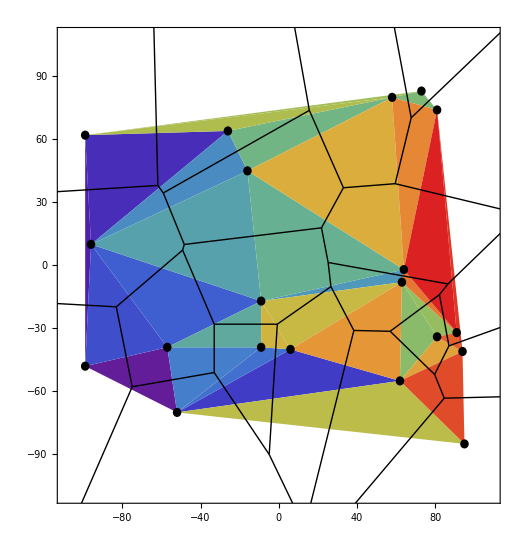

Dr. Jim Arlow

© 2019, 2020, Clear View Training Limited
www.clearviewtraining.com

THIS BOOK CONTAINS SOFTWARE. THIS SOFTWARE IS PROVIDED BY THE COPYRIGHT HOLDERS AND CONTRIBUTORS “AS IS” AND ANY EXPRESS OR IMPLIED WARRANTIES, INCLUDING, BUT NOT LIMITED TO, THE IMPLIED WARRANTIES OF MERCHANTABILITY AND FITNESS FOR A PARTICULAR PURPOSE ARE DISCLAIMED. IN NO EVENT SHALL THE COPYRIGHT HOLDER OR CONTRIBUTORS BE LIABLE FOR ANY DIRECT, INDIRECT, INCIDENTAL, SPECIAL, EXEMPLARY, OR CONSEQUENTIAL DAMAGES (INCLUDING, BUT NOT LIMITED TO, PROCUREMENT OF SUBSTITUTE GOODS OR SERVICES; LOSS OF USE, DATA, OR PROFITS; OR BUSINESS INTERRUPTION) HOWEVER CAUSED AND ON ANY THEORY OF LIABILITY, WHETHER IN CONTRACT, STRICT LIABILITY, OR TORT (INCLUDING NEGLIGENCE OR OTHERWISE) ARISING IN ANY WAY OUT OF THE USE OF THIS SOFTWARE, EVEN IF ADVISED OF THE POSSIBILITY OF SUCH DAMAGE.
THIS BOOK CONTAINS LIVE CODE. BE SAFE AND EXAMINE ALL CODE BEFORE EXECUTING IT. ONLY USE COPIES OF THIS BOOK OBTAINED LEGITIMATELY FROM WWW.CLEARVIEWTRAINING.COM OR THE WOLFRAM NOTEBOOK ARCHIVE.

## Table of contents

Table of contents

Introduction

About this edition

Our approach to computational geometry

Audience

About the code

This book and the Wolfram Language

Conventions

Using the online documentation

Getting started - clearing the namespace

Essential utility functions

Chapter 1:  Points and lines

Points

Query functions for points

Point list indexes and vertexes

Random point sets

Extreme points of a point set

Lines and line segments

Approximating lines and rays

Summary

Chapter 2: Polygonal chains

Polygonal chains in 2D

Simple polygonal chains

Monotone polygonal chains

Summary

Chapter 3: Triangles, and the relationship of points to lines

Defining a triangle

Representing polygons in the Wolfram Language

Triangles

Signed area of a triangle

2D triangle area by determinants

Triangles and the relationships of points to lines

Collinearity and general position

Between

Testing the point/line relationship functions

Relationship between a list of points and a line

Points on the same side of a line

Summary

Chapter 4: Triangle geometry

The centroid, medians and circumcircle of a triangle

The internal angles of a triangle

Triangulating a triangle on an internal point

Random triangles

Summary

Chapter 5: Polygons

Polygon vertex navigation

Polygon edges

Regular polygons

Regular polygons with integer vertexes

Regular star polygons

Monotone mountain polygons

Area of a polygon

Convex polygon area by triangulation

General polygon areas

Number of triangulations of a convex polygon

Summary

Chapter 6: Random polygons

Random polygons

Random simple star shaped polygons

The randomStarShapedPoly[...] function

Summary

Chapter 7: Intersections

Testing for polygon convexity

Point inside convex polygon

Intersection of line segments with line segments and polygons

Proper intersection of line segments

Improper intersection of line segments

Intersection of line segments

Polygon intersection with line segments

Polygon self-intersection

Demonstration of line segment intersection types

Summary

Chapter 8: Polygon extreme points, tangents, monotonicity and splitting

Polygon extreme points

Monotone polygons

Tangent to a convex polygon from a point

Splitting a convex polygon into polygonal chains

Summary

Chapter 9: Convex hulls

Incremental convex hull algorithm

Graham scan convex hull algorithm

Comparison of incremental and Graham scan convex hull functions

Summary

Chapter 10: General polygon triangulation

Polygon diagonals

Finding polygon diagonals

Polygon triangulation by ear tip removal

Plotting triangulations

Summary

Chapter 11: Point set triangulation and the dual graph

Incremental point set triangulation algorithm

Simple incremental point set triangulation with convex hull

Finding the triangles for an edge in a triangulation

The dual graph of a triangulation

Analysing a triangulation using graph theory

Visibility graph of a polygon

Summary

Chapter 12: Delaunay triangulation

Assessing triangulations

The angle vector of a triangulation

The Delaunay triangulation

Flipping diagonals

Converting a triangulation to a Delaunay triangulation

Delaunay triangulation example

Delaunay triangulations and terrain

Summary

Chapter 13: Voronoi diagrams

A Voronoi diagram algorithm

Summary

Chapter 14: Summary

Resources

Bibliography

## Introduction

This book is an introduction to some of the fundamental algorithms of computational geometry. The emphasis in this book is on three things:

Explanation

Implementation

Demonstration

We explain key concepts in computational geometry, implement them in the Wolfram Language, then provide demonstration programs that illustrate how they work. Our aim is that this book should act as a complement to existing books on computational geometry. This means that we generally don't cover mathematical proofs because these are already covered very satisfactorily elsewhere (see the Bibliography). A key inspiration for this book are the two computational geometry textbooks by Joseph O’Rourke (listed in the bibliography), and we recommend you study these in conjunction with this text.

We hope you find this text valuable and that it helps you in your work, whatever that may be. Visit us at www.cleraviewtraining.com to see the other books we have available.

## About this edition (important - don’t skip!)

This ebook book comes in two physical parts. The first part is a PDF available from Amazon (n.b. if you have Kindle Unlimited, you can get it for free). The PDF is not interactive due to technical limitations of the PDF platform. However, it can be read on any device that supports PDF, and is a very useful reference-only version of the book for those occasions when you don’t have Mathematica or the Wolfram Player available. It makes the book available to a wider audience.

The second part is a free Mathematica Notebook  available from the Wolfram Notebook Archive (search on “Arlow”).  This is more or less identical to the PDF, except that it is fully executable. This Notebook provides functioning, executing code that implements and demonstrates computational geometry algorithms directly. There is nothing better than seeing an algorithm in action, and a good, interactive, demonstration can replace an extraordinary amount of text. Also, whilst a textual (and to a lesser extent, pseudo code) description of an algorithm may be subject to the ambiguity of natural language, live code is the algorithm executing.

In terms of running the Notebook, you will need either Mathematica or the free Wolfram Player. The notebook currently won’t run in the Wolfram Cloud because of some technical limitations on Cloud graphics that we are working with Wolfram Research to resolve. This also means that when you view the Notebook on the Wolfram Archive, you will see only a static image, and it will not execute there. Running the book in Mathematica allows you to play about with the code in any way you want, whereas the free Wolfram Player gives you the full interactive experience, but without the ability to change the code.

If you are reading the book as a static PDF, please note that we have maintained the same layout as the Mathematica Notebook. This means that we have been very generous with space when laying out the pages. In particular, we arrange pages to always try to keep code blocks together, and keep them with their output if possible. This means that there is quite a lot of whitespace on some pages. This is intentional, and as there is no printed version of this text, no trees are harmed by this extravagance.

If you are a Python programmer, you are in luck! You can get a version of this text written entirely in Python using Jupyter Notebooks. The Python version is written in idiomatic Python, so it uses object orientation to advantage to simplify some of the geometric objects and algorithms. If you wish to port the algorithms to another object oriented language such as Java, then the Python version of the text will be the one you want. Note that we do our best to keep the content of the Python and Mathematica versions in synchronisation, but because they are developed separately, there may be some  small differences.

## Our approach to computational geometry

Computational geometry is most commonly approached from a problem based perspective, where geometric problems are presented and  algorithms are developed to solve them. This is a very appropriate strategy and we list several excellent texts in the bibliography that already do this very well.

Because these resources exist, it has allowed us to take a different approach, which complements them. We have structured the text according to taxonomic principles: we examine the key geometrical objects that one is concerned with in computational geometry, and then we look at the key algorithms that apply to them. This has the advantage that the objects and algorithms become organized in a way that is easy to reference, understand and learn. It also fits nicely with developing a codebase because the simplest objects occur first, and the more complex objects build on them. Using this approach, we can build up quite an extensive code base in a systematic way as we go along.

Every taxonomy requires a clearly stated organizational principle or principles. The taxonomic principle we use is that of constraints. For example, a line segment would be considered to be a more constrained type of line because it has two end points, whereas a line is infinite and has no end points. As you will see, this simple principle allows us to group geometric objects in a very meaningful way.

## Audience

The book is (obviously) for anyone interested in computational geometry. Probably the primary audiences for this book are undergraduates or post-graduates doing a course that involves computational geometry in some form. Given that the field of computational geometry covers such a wide area (graphics, robotics, geographical information systems, etc.) this is potentially quite a broad range of readers.

We also expect that this book can be very useful to lecturers in computational geometry as a source of demonstrations for their students. We naturally hope that in return, they might recommend this book as a course book, or at least attribute the demonstrations to this text.

Apart from educational uses, the book provides a very useful catalog of key computational geometry algorithm implementations for programmers. Because the algorithms are expressed in a concise, functional, style, they are easy to understand and port to other languages, especially functional ones.

Although this book is not designed as a tutorial on the Wolfram Language, we feel that when combined with the excellent on-line Wolfram Language documentation and tutorials, it could be used as such by the experienced programmer.

## About the code

There are three distinct types of code in this text:

Code which supports the text - this is code that creates a diagram or illustrates a feature of the Wolfram Language. It is not part of a computational geometry algorithm.

Code that implements a computational geometry algorithm - this code is developed in a logical way and is embedded in a narrative description of the algorithm and its implementation details. This is a Literate Programming approach that lends itself very well to an interactive text such as this.

Interactive demonstrations - this code provides graphical demonstrations of the algorithms. The aim is to demonstrate what an algorithm does or how an algorithm works in an interactive, visual way that is easy to understand. By playing with these demonstrations directly you will gain a better understanding of the algorithms.

We have found that it is not necessary to distinguish these three types of code typographically - as you read the book, you will find that it is always completely clear from the context what kind of code you are looking at.

## This book and the Wolfram Language

If you are reading this book, you may already have some familiarity with the Wolfram Language. If you are new to the language, then you are in for a mind-expanding treat!

The first edition of this book was written in 2014, and would not have been possible without the Wolfram Language and the Computational Document Format (CDF). CDF was a format for executable documents that comprise text, graphics and executable code that has (sadly) now been deprecated. To develop an interactive book such as this in Java, C, Python etc. would have involved creating a publishing platform for executable books similar to CDF and would have been prohibitively difficult, time consuming and expensive at that point in time.

In 2020, the world has moved on quite a lot, and other languages have begun to catch up with the Wolfram Language - at least in some areas! In particular, there is an excellent facility for Python called Jupyter Notebooks, that provides an executable document platform, similar in some respects to CDF, that is more than adequate for a book such as this, and as we mentioned earlier, this has allowed us to rewrite this book entirely in Python. The book is called “Interactive Computational Geometry in Python”, and you can find it at www.clearviewtraining.com. (Note: If you want to know how to write a whole book in Jupyter, take a look at our SlideShare presentation.)

Getting back to the Wolfram Language, it is a very high-level symbolic language that allows the same focus on algorithmic structure as pseudo code, and yet is as executable as C. In the past, it has been primarily known as the language of Mathematica, but it actually goes much further than this, and Mathematica is really only one particular use case for this uniquely powerful and elegant language. For example, the Wolfram Language has also made possible innovations such as Wolfram Alpha and Siri. In fact, it is such a powerful language that our use of it here is trivial.

The very high-level of the Wolfram Language, drastically reduces the amount of boilerplate code and allows you to focus on what the algorithm actually needs to do, whilst leaving how it actually does it to the implementation details of the language. As such, we can have the best of both worlds - the readability of pseudo code and the executability of C, Java, Python, etc. Python is also a very powerful and flexible language, and if you compare the code in this book with the Python code in Interactive Computational Geometry in Python, you will see that we have achieved a similar effect, but by using the object-oriented features of Python to build a high level language in which to express the algorithms.

The Wolfram language is a multi-paradigm language. This means that you can program it in procedural, object-oriented (with some difficulty), functional, rules-based and other programming styles. We believe that the most natural style for the majority of computational geometry algorithms is functional, and this is hardly surprising because so much of mathematics is about functions. The functional style we have adopted here is clean, easy to read, very concise and very expressive. We hope you agree with us after working through this text! Although the functional programming style allows us to express most algorithms very simply, sometimes other paradigms, such as procedural, are clearer or more appropriate, and the language allows us to mix and match to best advantage.

What do we mean when we say that the Wolfram Language is a “symbolic” language? This means that we are not restricted to working only with entities such as ints, floats, structs, objects, etc. - we can work with pure symbols that have no assigned value or meaning. For example we can add three  emoji symbols together and get a sensible answer:

```mathematica
☺ +☺ +☹
```

2 ☺+☹

We take advantage of symbol processing at several points in the text where we let the Wolfram Language perform algebraic manipulations for us.

Another powerful feature of the language is advanced pattern matching. We use this facility to identify geometric objects and apply a kind of “type safety” to our functions by specifying patterns that the function parameters have to match. You will see plenty of examples of this shortly.

## Conventions

We have very few conventions in this book:

Mathematica Notebooks have different types of cell. All code will be inside a code cell, and these cells are executable. For example:

```mathematica
1 + 2
```

3

New function and variable names introduced in this text will be in lowerCamelCase and look like this:

```mathematica
someNewFunctionInTheGlobalNamespace[] := "Hello World"
```

```mathematica
someNewFunctionInTheGlobalNamespace[]
```

Hello World

Wolfram Language built-in function and variable names are in UpperCamelCase (e.g. TrueQ below). Functions that return a Boolean value (True or False) are post fixed by Q (this is a standard naming convention in Lisp-like languages) e.g.

```mathematica
isTrueExampleQ[x_] := TrueQ[x]
```

```mathematica
isTrueExampleQ[True]
```

True

```mathematica
isTrueExampleQ[False]
```

False

Equations are in this font: y = x^2

Definitions may be indented to indicate taxonomic relationships and look like this:

Line: a straight one-dimensional figure having no thickness and extending infinitely in both directions.

Ray: a straight one-dimensional figure having no thickness, beginning at a point and extending infinitely in one direction.

Indexes vs. points - most functions return lists of points, but some return lists of indexes into a pre-existing list of points. The name of any function that returns indexes will be post fixed by Index.

## Using the online documentation

The Wolfram Language comes with extensive online documentation in the Wolfram Language & System Documentation Center. When you see a built-in function, and you don’t know what it does, you can look it up online. Remember that all function names that begin with a capital letter are built-in Wolfram Language functions, and you can find complete descriptions of these Wolfram Language & System Documentation Center. You might want to check it out now, before you get into the book.

## Getting started - clearing the namespace

The first thing we have to do is to set up the Wolfram Language to execute the examples in the rest of this text. When we define a symbol in the global namespace of the Wolfram Language, that symbol is there for the whole session. This can lead to unexpected results, so it is a good idea to begin with a call to ClearAll[...] in order to purge the namespace of unwanted values:

```mathematica
ClearAll["Global`*"]
```

## Essential utility functions

We are going to be making heavy use of graphics, so it makes sense to define some useful graphics functions up front. These functions must be used within the Wolfram Language Graphics[...] function as we will see shortly. Just take these functions as read for now - they operate on data structures that we have yet to define, and you will soon see examples of them in action. So if you don’t understand these functions now, don’t worry, just proceed with the rest of the text and come back to them later.

### Calculate an offset from a point for a label:

```mathematica
offsetLabel[ {x_, y_}, offset_] := {x,y}  + {
If[ Sign[ x ]== 0, 1, Sign[ x ]],
If[ Sign[ y ]== 0, 1, Sign[ y] ]
} * offset
```

### Label polygon vertexes v1, v2, ... vn:

```mathematica
polyVertexLabels[poly_List, offset_List:{0.4,0.4}] := MapIndexed[ Text[Style[Row[{"v",#2[[1]]}], 14], offsetLabel[#1, offset ]] &,poly ]
```

### Label points arbitrarily (defaults to 3 vertexes, a, b, c):

```mathematica
pointLabels[points_List, labels_List:{"a", "b", "c" }, offset_List:{0.4,0.4}] := 
MapIndexed[ Text[Style[labels[[ #2[[1]] ]], 14], offsetLabel[#1, offset ]] &,points ]
```

### Label points with their coordinates:

```mathematica
pointCoordLabels[poly_List, offset_List:{0.4,0.4}] := MapIndexed[ Text[Style[#1, 14], offsetLabel[#1, offset ]] &,poly ]
```

### Standard graphical style:

Throughout this text, we will be making a lot of plots. We will generally do so on a 10x10 grid, because that is just about the size right for the interactive demonstrations. Here is a standardPlotStyle defined as a List of key → value pairs that gives us a consistent look and feel for the plots:

```mathematica
standardPlotStyle := {AspectRatio -> 1, Axes -> True, Frame-> True, AxesOrigin -> {0,0}, GridLines->{Range[-6,6], Range[-6,6]}, PlotRange->{{-6,6},{-6,6}}}
```

### Printing out examples:

This utility function takes a Wolfram Language expression, and returns a List where the first element is the unevaluated expression (in Wolfram Language terminology, the form of the expression), and the second element is the result of evaluating the expression. This is useful for constructing tables of examples that show a particular form and then the result of evaluating it.

```mathematica
formValue[exp_] := {HoldForm[exp], exp}
formValue[comment_, exp_] := {comment, HoldForm[exp], exp}
SetAttributes[formValue, {HoldAll, Listable}]
```

In the Wolfram Language, functions can have attributes that specify their properties. In this case, we give the formValue[...] function the attribute HoldAll, which means that it does not immediately evaluate its arguments, and Listable, which means that the function will be automatically applied to each element when given a List of arguments. In that case it will return a List of results.

We will almost always use formValue[...] to create a table of results, so here is a convenience function to encapsulate that:

```mathematica
gridFormValue[exp_] := Grid[formValue[exp], Frame->All, Alignment->Left]
SetAttributes[gridFormValue, {HoldAll}]
```

For example:

```mathematica
gridFormValue[{1+1 + 2,2+2 +3, 3+3 + 4, \[MathematicaIcon] + \[MathematicaIcon]+ 🐺}]
```

1+1+2 | 4
2+2+3 | 7
3+3+4 | 10
\[MathematicaIcon]+\[MathematicaIcon]+🐺 | 2 \[MathematicaIcon]+🐺

## Chapter 1: Points and lines

Let’s start with some definitions:

Euclidean plane: a flat two dimensional surface.

Point: a location.

General position for points: a set of points is said to be in general position if no three points are collinear.

The Euclidean plane is our work surface on which we will construct our geometry. This is 2 dimensional, so henceforth, when we refer to “point” we will mean “2D point”. We will be mostly working in two dimensions.

General position for points is quite an important concept, because, as we will see shortly, computational geometry algorithms that involve sorting points often fail if the points are not in general position. We will indicate these as we encounter them. It is worth noting that there are other, more constrained, definitions for general position than the one given above. For example, some algorithms only work if no two points have the same x or y. We will indicate any such additional constraints as they arise.

## Points

We will represent a point as a List of two terms that will usually be Integers. Why Integers? Not for speed reasons (floating point is faster than integer arithmetic in the Wolfram Language) but because Integers allow exact placement of points in our interactive demonstrations that makes it easy to investigate special cases.

Wolfram Language Lists are ordered and indexed and behave much like arrays in other languages. For a point, the first number in the List is the x coordinate, the second number the y coordinate and for a 3D point, the third number is the z coordinate.  List indexes start at 1, unlike C and Java whose array indexes start at 0.

Let’s define three constants, x=1, y=2 and z=3. There is a standard way to define constants in the Wolfram Language:

```mathematica
Unprotect[x]; x = 1; Protect[x];
Unprotect[y]; y = 2; Protect[y];
Unprotect[z]; z = 3; Protect[z];
```

These are now constants defined in the global namespace, so if we try to change x, y or z we will get an error. Note that the initial Unprotect is important, because without it, you can get errors if the definition cell should ever be reevaluated.

If we define a point p, as a List, we can access its x and y coordinates as shown below. Note that the Wolfram Language uses double square brackets [[...]] to access List elements:

```mathematica
With[{ p = {5,9} },
Print[ "x = ", p[[x]], ", y = ", p[[y]]];
]
```

x = 5, y = 9

We have defined our test point as a local variable inside a With block. This is to ensure that common names, such as p, do not go into the global namespace. It’s worth pointing out that you have to be very careful about managing the global namespace in Wolfram Language programs. If you don’t you can get all kinds of odd results when things don’t have the value you think they should have. When developing code, its a good idea to clear the global namespace every now and again using ClearAll["Global`*"].

## Query functions for points

It is very useful to have query functions that can test if an expression is a point or not. The way to do this in the Wolfram Language is to match the candidate expression against an appropriate pattern. The pattern _?NumberQ matches anything (_) that is (?) a number (NumberQ). The idiom, ?fn, invokes the built-in function PatternTest on the single argument function fn, which in this case is the function NumberQ. Here are the patterns for 2D and 3D points:

```mathematica
pointPattern = {_?NumberQ,_?NumberQ};

point3DPattern = {_?NumberQ,_?NumberQ, _?NumberQ};
```

Here are the query functions:

```mathematica
pointQ[ pt_ ] := MatchQ[ pt, pointPattern ]

point3DQ[ pt_ ] := MatchQ[ pt, point3DPattern ]
```

Here is a simple test program:

```mathematica
gridFormValue[{
pointQ[ {1,2} ], 
pointQ[ {1.1,2.6} ], 
pointQ[ {{1},{2}} ], 
 pointQ[ {1,2, 3} ], 
point3DQ[ {1,2, 3}]
}]
```

pointQ[{1,2}] | True
pointQ[{1.1,2.6}] | True
pointQ[{{1},{2}}] | False
pointQ[{1,2,3}] | False
point3DQ[{1,2,3}] | True

This pair of functions tests for Lists of 1 or more ( .. ) 2D and 3D points:

```mathematica
pointListQ[ lpt_ ] := MatchQ[ lpt, {pointPattern..}]

pointList3DQ[ lpt_ ] := MatchQ[ lpt, {point3DPattern..}]
```

Here is a test program for these functions:

```mathematica
gridFormValue[{
pointListQ[ {} ],
pointListQ[ {1,2} ],
pointListQ[ {{1,2}} ],
pointListQ[ {{1,2}, {3,4}} ],
pointListQ[ {{1},{2}} ],
pointList3DQ[ {{1,2, 3}} ],
pointList3DQ[ {{1,2, 3}} ]
}]
```

pointListQ[{}] | False
pointListQ[{1,2}] | False
pointListQ[{{1,2}}] | True
pointListQ[{{1,2},{3,4}}] | True
pointListQ[{{1},{2}}] | False
pointList3DQ[{{1,2,3}}] | True
pointList3DQ[{{1,2,3}}] | True

## Point list indexes and vertexes

The indexes of any List, l  are always given by the expression Range[ Length[ l ] ]. Here is a convenience function for this:

```mathematica
indexes[ l_List ] := Range[ Length[l] ]
```

This will always return a List of Integers. We can test for this as follows:

```mathematica
indexListQ[ il_ ] := MatchQ[ il, {_?IntegerQ...}]
```

Here is another convenience function that takes a List of points, a List of indexes and returns a corresponding a List of points corresponding to the List of indexes:

```mathematica
vertexes[ poly_?pointListQ, indexes_?indexListQ ] := poly[[ indexes ]]
```

For example:

```mathematica
indexes[{{1,1}, {2,2}, {3,3}}]
```

{1,2,3}

```mathematica
vertexes[{{1,1}, {2,2}, {3,3}}, {1, 3}]
```

{{1,1},{3,3}}

```mathematica
vertexes[{{1,1}, {2,2}, {3,3}}, {1, 1}]
```

{{1,1},{1,1}}

## Random point sets

It is often useful to be able to generate random geometric figures in order to test our algorithms. Here is a function that generates a random set of unique points with integer coordinates in the (default) range -5 to 5:

```mathematica
randomPointSet[ n_Integer, range_:Range[-5,5] ] :=RandomSample[Permutations[range, {2}], n]
```

Permutations is a built-in function that returns the permutations of a List of things. Here, we have asked for all permutations of the numbers {-5, -4... 4, 5} of length 2. We then use RandomSample to give us a random selection of n of those points. A key feature of RandomSample is that it never samples a List element more than once, so the n points are guaranteed to be unique. For example:

```mathematica
randomPointSet[10]
```

{{0,-1},{3,1},{-4,1},{-2,-1},{4,3},{5,-4},{1,4},{4,2},{-4,-5},{-1,0}}

## Extreme points of a point set

Here is a definition of an extreme point of a point set:

Extreme point: an extreme point of a point set is a point that is the furthest along a given direction.

A very useful function for working with point sets is one that finds the extreme points in the X and Y directions. On the X axis, these are the rightmost and leftmost points, and on the Y axis, the topmost and bottommost points. The extreme points are often unique, but not always. Any one of them can overlap with another one e.g. a point which is rightmost AND bottommost. There must be at least two unique extreme points (in which case the other points are positioned between them) and, obviously, there can be no more than 4. So the following equality holds:

2 ≤ number of unique extreme points ≤ 4

When there are two (or more) candidate points for a given extreme (for example two or more points with the same extreme Y coordinate), this simple algorithm just gives you the last one it finds:

```mathematica
extremePointsXY[ pts_?pointListQ ] := Block[{rightmost, leftmost, topmost, bottommost, i},
rightmost = leftmost = topmost = bottommost = pts[[1]];
For[ i = 1, i ≤ Length[pts],i++,
If [ pts[[i,x]] > rightmost[[x]], rightmost = pts[[i]] ];
If [ pts[[i,y]] > topmost[[y]], topmost = pts[[i]] ];
If [ pts[[i,x]] < leftmost[[x]], leftmost = pts[[i]] ];
If [ pts[[i,y]] < bottommost[[y]], bottommost = pts[[i]] ];
];
{rightmost, topmost, leftmost, bottommost}
]
```

Here is a test program:

```mathematica
Manipulate[ 
Module[{exPts },
exPts = extremePointsXY[ pts ];
Graphics[{
Text["rightmost",exPts[[1]] + {1.1,0} ],
Text["topmost",exPts[[2]] + {0,0.6} ],
Red,Circle[#, 0.3] &/@ exPts[[1;;2]],

Text["leftmost",exPts[[3]] + {-1,0} ],
Text["bottommost",exPts[[4]] + {0,-0.6} ],
Blue,Circle[#, 0.3] &/@ exPts[[3;;4]]
},standardPlotStyle ]
],
{{ pts,randomPointSet[ 10, Range[-4, 4] ] },{-5, -5}, {5,5}, 1, Locator}]
```

-Graphics-

Note: These extreme points must lie on the convex hull of the point set. We will look at the topic of convex hulls in Chapter 7, but for now, just imagine the convex hull as an elastic band that stretches around all the points. We will see that these extreme points can provide a useful starting position for an algorithm to calculate the convex hull.

The above program, although trivial, illustrates several important (and unique) features of the Wolfram Language that we shall be using throughout the rest of the text:

Manipulate - lets you create dynamic user interfaces that have automatically generated controls (Buttons, Sliders, Locators, etc.) with very little code (see the on-line Documentation Center for lots more information).

Graphics - provides a graphics context on which to draw using functions such as Text[...].

Locator - a control that you can drag about with the mouse - we will use these a lot.

## Lines and line segments

There are quite a few definitions related to lines (we have indented the definitions to indicate taxonomic relationships):

Line: a straight one-dimensional figure having no thickness and extending infinitely in both directions.

Ray: a straight one-dimensional figure having no thickness, beginning at a point and extending infinitely in one direction.

Line segment: A closed interval corresponding to a finite portion of an infinite line.

(Euclidean) Plane: A flat, two dimensional surface.

Half plane: a planar region consisting of all points on one side of an infinite straight line, and no points on the other side.

Closed half plane: a  half plane that includes the points on the line.

Open half plane: a half plane that does not include the points on the line.

General position for lines: a set of lines is said to be in general position if no three lines are concurrent (intersect at the same point).

We will represent a line segment in the Wolfram Language as a List of two points. For most computational geometry algorithms, we require line segments to be directed. In other words it is generally significant whether we traverse the line segment a b from a to b or from b to a. We will see examples of this shortly when we look at triangle areas.

We can define an example global line segment as follows:

```mathematica
seg1 = {{-2,3}, {2,1}}
```

{{-2,3},{2,1}}

We can write functions to test for line segments in the same way as we tested for points:

```mathematica
lineSegmentQ[ l_ ] := MatchQ[l, {pointPattern, pointPattern} ]

lineSegment3DQ[ l_ ] := MatchQ[l, {{point3DPattern, point3DPattern}} ]
```

Here are some example tests:

```mathematica
gridFormValue[{
lineSegmentQ[ seg1 ], 
lineSegmentQ[ {{-2, 2, 1}, {2, 4, 5} } ], 
lineSegmentQ[ {{-2}, {2} } ], 
 lineSegmentQ[ {{-2,3}, {2,1}, {4,5} } ]
}]
```

lineSegmentQ[seg1] | True
lineSegmentQ[{{-2,2,1},{2,4,5}}] | False
lineSegmentQ[{{-2},{2}}] | False
lineSegmentQ[{{-2,3},{2,1},{4,5}}] | False

The program lineExample is a utility program that plots a list of points and allows you to manipulate them:

```mathematica
lineExample[ lineSegment_?pointListQ ] := Manipulate[
Graphics[{
Red,Arrow[ ls ],
Black, polyVertexLabels[ls]
},
standardPlotStyle],
{{ls, lineSegment},{-5, -5}, {5,5}, 1, Locator}, 
FrameLabel -> "Directed line segment(s)"]
```

Let’s try out lineExample on our global line segment, seg1:

```mathematica
lineExample[ seg1 ]
```

-Graphics-

The Wolfram Language has excellent graphical support for lines, rays, line segments, planes and half planes. In the example below the point labelled half plane direction indicates which side of the line p_1 p_2 is the half plane.:

```mathematica
Manipulate[
Graphics[{
If[ type == "line",{Blue,InfiniteLine[{pt1, pt2}]}],
If[ type == "ray",{Blue,HalfLine[{pt1, pt2}]}],
If[ type == "line segment",{Blue,Line[{pt1, pt2}]}],
If[ type == "half plane",{LightBlue,HalfPlane[{pt1, pt2},pt3 - pt1]}],
Black, pointLabels[{pt1, pt2, pt3}, {"pt1", "pt2", "half plane direction"}, {0.5, 0.5}]
},
standardPlotStyle
],
{type, {"line", "ray", "line segment","half plane"}},
{{pt1, {0,1}},{-5, -5}, {5,5}, 1, Locator}, 
{{pt2, {3,1}},{-5, -5}, {5,5}, 1, Locator},
{{pt3, {4,2}},{-5, -5}, {5,5}, 1, Locator}]
```

-Graphics-

Planes are also supported but only in 3D:

```mathematica
Graphics3D[{
InfinitePlane[{{1,0,0},{1,1,1},{0,0,1}}],
Red,Arrow[Tube[{{0,0,0},{1,0,0}}]],
Green,Arrow[Tube[{{0,0,0},{1,1,1}}]],
Blue,Arrow[Tube[{{0,0,0},{0,0,1}}]]
}]
```

-Graphics-

In the above examples, we used Wolfram Language built-in functions Line[...], InfiniteLine[...], HalfLine[...] etc. These functions return Regions that can be displayed using Graphics and used in calculations. In fact, the native representation of geometric objects in the Wolfram Language is as Regions, and if you look in the documentation under “Geometric Computation”, you will find a whole host of built-in Regions, such as Polygons, Lines, ParametricRegion etc. etc. There are also many functions to create and manipulate Regions. We only use Regions occasionally in this text because we are concerned with describing geometric objects and algorithms from the bottom up. However, just to give you some idea of the power of Regions in the Wolfram Language, the demo below creates a Region that is the union of a Ball and a Cube. See how easily we can create complex Regions and apply Boolean operators to them:

```mathematica
Region[RegionUnion[{Ball[{0,0,0}, 1], Cube[{0.5,0.5,0.5},1.5]}]]
```

-Graphics-

## Approximating lines and rays

Although the Wolfram Language has good built-in support for infinite lines and rays, most other languages do not, so in this section, we will see how we can approximate them.

As we have already mentioned, lines and rays have infinite extent. Because our canvas is finite, we can never draw them, we can only draw finite line segments. However, we can approximate a ray by extending a line segment so that one end is well outside the drawing area. Similarly, we can approximate a line by ensuring that both ends are well outside the drawing area.

Using Wolfram Language array notation for points, line segment s comprising points p_1 and p_2 may be extended by distance d from both ends as follows:

s_extended = (d {p_1- p_2, p_2 -p_1})/(|{p_1- p_2}|) + {p_1, p_2}

Here is a function that can extend a line segment from either end or both ends. We extend from one end to simulate a ray, and from both ends for a line.

```mathematica
extendLine[pt1_?pointQ,pt2_?pointQ,d_?NumberQ, mode_Integer:0, inclusive_:False] := Block[{ x = {pt1, pt2}, beginning, end},
If[ pt1 == pt2, Return[{pt1, pt2}]];
{beginning, end} = {pt1, pt2}+ {pt1 - pt2,pt2-pt1}d/Norm[pt1-pt2];
Which[
mode == 0, {beginning, end},
(mode >0) && !inclusive, {pt2,end},
(mode <0) && !inclusive, {pt1,beginning},
(mode >0) && inclusive , {pt1,end},
(mode <0) && inclusive, {pt2,beginning}
]
]

(* Convenience function to accept a List of points rather than two individual points *)
extendLine[{pt1_?pointQ,pt2_?pointQ},d_?NumberQ, mode_Integer:0, inclusive_:False] := extendLine[pt1,pt2,d, mode, inclusive]
```

Here is a demo program to show you how the function works. Notice that d is the length to extend the line, mode determines which end of the line to extend (or both) and inclusive determines whether to return just the extension or the complete extended line.

```mathematica
Manipulate[
Graphics[{
{Blue,Dashed,Line[{pt1, pt2}]},
Red, Line[extendLine[pt1, pt2, distance,mode, inclusive ]],
Black, pointLabels[{pt1, pt2}, {"pt1", "pt2"}, {0.7, 0.7}]
},standardPlotStyle],
{{inclusive, False, "inclusive"}, {True, False}},
{{mode, 0, "mode"}, {0, -1, 1}},
{{distance,0, "distance"}, -10,10,1},
{{pt1, {0,1}},{-5, -5}, {5,5}, 1, Locator}, 
{{pt2, {3,1}},{-5, -5}, {5,5}, 1, Locator}
]
```

-Graphics-

## Summary

In this chapter we have put in place the basic concepts, functions and software tools to allow us to explore computational geometry through simple interactive programs. We will build on this base in subsequent chapters, constructing algorithms, more complex functions and interactive demonstrations.

## Chapter 2: Polygonal chains

In this chapter we will explore two dimensional polygonal chains, which are ordered lists of points. Virtually all of the work we do in subsequent chapters will involve polygonal chains in one form or another.

## Polygonal chains in 2D

Here are the definitions we will be working with:

Vertex: the point where two or more lines, line segments or rays meet.

Polygonal chain: a curve specified by a sequence of points called its vertexes, so that the curve consists of the line segments connecting consecutive vertexes. In computer graphics, this is commonly known as a polyline.

Open polygonal chain: a polygonal chain whose last vertex is not connected to its first vertex.

Closed polygonal chain: a polygonal chain whose last vertex is connected by a line segment to its first vertex. Alternatively, a polygonal chain whose last and first vertexes are identical.

Edge: a line segment joining two vertexes.

A polygonal chain C has vertexes v_1,v_2, ... v_n,  where n ⩾ 3. We represent it in the Wolfram Language as a List of three or more points. For example, in two dimensions:

```mathematica
pchain1 = {{-2,3},{2,1}, {3,-1}, {2,-4}, {-1,-1}}

lineExample[pchain1]
```

{{-2,3},{2,1},{3,-1},{2,-4},{-1,-1}}

-Graphics-

As usual, it is convenient to be able to test for 2D polygonal chains using the Wolfram Language pattern matching facility:

```mathematica
polygonalChainQ[ pc_] := MatchQ[ pc,{pointPattern, pointPattern, pointPattern..}]
```

Here are some examples of polygonalChainQ[ ...] in action. It only returns True for a List of 3 or more points:

```mathematica
Grid[{
formValue["A point", polygonalChainQ[{1,1}]],
formValue["A List containing 1 point", polygonalChainQ[{{1,1}}]],
formValue["A List containing 2 points", polygonalChainQ[{{1,1}, {2,2}}] ],
formValue["A List containing 3 or more points - a polygonal chain", polygonalChainQ[{{1,1}, {2,2}, {3,3}}] ]
}, Frame->All, Alignment->Left]
```

A point | polygonalChainQ[{1,1}] | False
A List containing 1 point | polygonalChainQ[{{1,1}}] | False
A List containing 2 points | polygonalChainQ[{{1,1},{2,2}}] | False
A List containing 3 or more points - a polygonal chain | polygonalChainQ[{{1,1},{2,2},{3,3}}] | True

For an open polygonal chain with vertexes v_1, v_2, ... v_n, the edges e_1,e_2 ... e_n are the line segments v_1v_2, v_2v_3, ... v_(n-1)v_n . If the chain is closed, it has the extra line segment  v_nv_1. We can obtain the edge indexes for an open polygonal chain using the Partition function. This function takes sub lists of a List with an offset. It’s easier to understand how this works if you consider the following symbolic example:

```mathematica
Partition[{Subscript[v, 1],Subscript[v, 2], Subscript[v, 3], Subscript[v, 4], Subscript[v, 5]}, 2, 1]
```

{{v_1,v_2},{v_2,v_3},{v_3,v_4},{v_4,v_5}}

So Partition takes from the List (first argument) pairs of elements (second argument) with an offset (third argument) of 1. Using this, we can calculate the polygonal chain edge vertexes and edge indexes as simple partitions of the chain:

```mathematica
pchainEdges[ pchain_?pointListQ] := Partition[pchain, 2, 1]

pchainEdgeIndexes[ pchainLength_Integer ]:= Partition[Range[pchainLength], 2, 1]

pchainEdgeIndexes[ pchain_?pointListQ ]:= Partition[indexes[pchain], 2, 1]
```

Here are some examples. We defined the global variable pchain1 earlier:

```mathematica
gridFormValue[{
pchain1,
pchainEdgeIndexes[ Length[ pchain1]],
pchainEdgeIndexes[  pchain1 ],
pchainEdges[ pchain1 ]
}]
```

pchain1 | {{-2,3},{2,1},{3,-1},{2,-4},{-1,-1}}
pchainEdgeIndexes[Length[pchain1]] | {{1,2},{2,3},{3,4},{4,5}}
pchainEdgeIndexes[pchain1] | {{1,2},{2,3},{3,4},{4,5}}
pchainEdges[pchain1] | {{{-2,3},{2,1}},{{2,1},{3,-1}},{{3,-1},{2,-4}},{{2,-4},{-1,-1}}}

## Simple polygonal chains

Simple polygonal chains do not self-intersect except at the intersection of consecutive edges. There are open and closed simple polygonal chains. Here are some definitions:

Simple open polygonal chain: only consecutive edges (e_i and e_(i+1)) intersect and only at their shared endpoint. In other words the intersection (∩) of edges e_i and e_(i+1) is the vertex v_(i+1). We can write this as follows:

e_i ∩ e_(i+1) = v_(i+1)for i = 1..n

Simple closed polygonal chain: we have an extra condition that the last vertex is joined to the first vertex:

e_i ∩ e_(i+1) = v_(i+1) and  e_n ∩ e_1 = v_1 for i = 1..n

We will consider algorithms for finding intersections later.

## Monotone polygonal chains

Here is a definition:

Monotone polygonal chain: a polygonal chain is monotone with respect to a straight line L if every line perpendicular to L intersects the polygonal chain at most once.

The program below shows some examples of monotone and non-monotone polygonal chains:

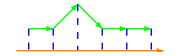
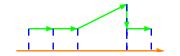
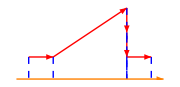
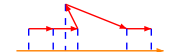
case | is monotone | plot
case 1 | True | -Graphics-
case 2 | True | -Graphics-
case 3 | False | -Graphics-
case 4 | False | -Graphics-

```mathematica
line1 = {{-0.5,0.1}, {5.5,0.1}};
pc1 = {{0,1}, {1,1}, {2,2}, {3,1}, {4,1}, {5,1}};
pc2 = {{0,1}, {1,1}, {2,1}, {4,2}, {4,1}, {5,1}};
pc3 = {{0,1}, {1,1}, {4,3}, {4,2}, {4,1}, {5,1}};
pc4 = {{0,1}, {1,1}, {2,1}, {1.5,2}, {4,1}, {5,1}};

plotPc[ pc_, col_] :=Graphics[{
col,Arrow/@ pchainEdges[pc],
{Blue,Dashed, Line[{#, {#[[x]],0.1}}] &/@ pc},
Orange,Arrow[line1]
}, ImageSize-> Small]

Grid[{
{"case", "is monotone", "plot"},
{"case 1","True",plotPc[pc1, Green]},
{"case 2","True", plotPc[pc2, Green]},
{"case 3","False",plotPc[pc3, Red]},
{"case 4","False",plotPc[pc4, Red]}}, Frame -> All]
```

In the table above, case 1 is obviously monotone - each perpendicular projection from a vertex to L is further along the line than the previous one, and so there can only ever be one intersection. Case 2 is more interesting. We have two vertexes collinear with their perpendicular projection onto the line. This is still considered to be monotone because the perpendicular only intersects a single edge of the chain. However case 3 is no longer monotone, because the perpendicular now intersects two edges. Case 4 is clearly non-monotone because there are an infinite number of possible double intersections over the range of the backtrack.

We can develop an algorithm to test for monotonicity by noticing two things:

In the simplest case, for a chain to be monotone, the projection of vertexes onto the line increases or decreases from one vertex to the next according to the relative directions of the line and the chain.

A chain is still monotone when the projections of two of the vertexes are equal.

We can detect the monotone cases 1 and 2 by considering triples of points, a,b and c and applying the following rules:

Rule 1: straightforward ascending and descending

Case 1 ascending: (a < b < c)

Case 1 descending: (a > b > c)

Rule 2: two equal projections

Case 2 ascending: (a = b < c) || (a < b = c)

Case 2 descending: (a = b > c) || (a > b = c)

In order to implement these rules, we need to be able to project the chain vertexes on to the line. From linear algebra, A_B is the scalar projection of vector A⃗ onto vector B⃗ and is given by:

A_B = A⃗ · B̂ = A⃗· (B⃗)/OverVector[|B|] = (x_A x_B+y_A y_B)/(√(x_B^2+y_B^2))

where B̂ is the unit vector along the direction of B⃗, and |B⃗| is the magnitude of B⃗.

The Cartesian coordinates of the projection on B⃗ can be obtained from:

x = A_B cos θ_B = (x_A x_B+y_A y_B)/(√(x_B^2+y_B^2)) y_B/(√(x_B^2+y_B^2)) =  (x_B(x_A x_B+y_A y_B))/(x_B^2+y_B^2)

y = A_B sin θ_B = (y_B(x_A x_B+y_A y_B))/(x_B^2+y_B^2)

where θ_B is the polar angle of B⃗ (the angle between the X axis and B⃗). These coordinates are very useful, because they allow us to plot the perpendicular projection lines from the chain vertexes to the line. Here is a function to calculate them:

```mathematica
projectPoint[ {ax_?NumberQ,ay_?NumberQ}, {bx_?NumberQ,by_?NumberQ} ] := { bx, by} * (ax bx + ay  by)/(bx^2 + by^2)
```

Note that there is also built-in Wolfram Language function, ProjectPoint[u, v] that projects vector u onto vector v, and we could have used that if we weren’t concerned with understanding how projection works. The arguments to our projectPoint[...]  function bear close examination. We are using the patterns {ax_?NumberQ,ay_?NumberQ} and {bx_?NumberQ,by_?NumberQ} to destructure the points passed in to the function. So, if we pass in a point {1, 2} as the first parameter, ax gets the value 1 and ay gets the value 2. This makes the x and y coordinates readily available in the function body, and we don’t need to use List indexes such as p[[x]] etc. to extract them. Argument destructuring is a very common use of patterns in Wolfram Language programming, and when used with care, it can make the code much clearer.

A very useful variant of this function is one that projects the point onto a line segment l = p_1 p_2 rather than a vector. By carefully specifying the patterns of the arguments, we can ensure that this variant is only called when the first argument is a point and the second argument is a line segment. We can then call the vector version of projectPoint with the vector (p_2 - p_1), and the point (a - p_1).  Finally, we need to add p_1 back to the result of this function call to move the projected point back to the right place.

```mathematica
projectPoint[ a_?pointQ, {p1_?pointQ, p2_?pointQ}] :=projectPoint[ a - p1, p2 - p1 ] + p1
```

Here is a simple test program. For convenience, vectors A⃗ and B⃗ are defined by a point and the origin. Note that if the vector B⃗ is zero, we get an error condition because there is nothing for A⃗ to project on to:

```mathematica
testProjection[]:=Manipulate[
Module[{proj},
proj=projectPoint[vecA,vecB];
Graphics[{
Blue,Arrow[{{0,0},vecB}],
Green,Arrow[{{0,0},vecA}],
Red,Arrow[{{0,0},proj}],
Dashed,Black,Line[{vecA,proj}],
Black,pointLabels[{vecA,vecB,proj},{"A","TraditionalForm`","A_B"}]
},standardPlotStyle
]
],
{{vecA,{1,4}},{-5,-5},{5,5},1,Locator},{{vecB,{-4,4}},{-5,-5},{5,5},1,Locator},FrameLabel->"Projection"
]

testProjection[]
```

-Graphics-

For purposes of testing for monotonicity, we’re not really concerned with the absolute distances of each vertex projection along the line, and neither do we need their Cartesian coordinates. All we require are the relative distances of the vertex projections so that we can compare them. We can therefore simplify the calculation by noting that the distance we need, A_B is proportional to the dot product of the two vectors. This gives us a relative measure of the distances of the vertexes projected onto the vector B⃗:

(A⃗)_B ∝ A⃗·B⃗

We can now write a very simple function to get the (relative) projections of each vertex in a polygonal chain onto an arbitrary line:

```mathematica
dotProductsWrtLine[pchain_?pointListQ, {l1_?pointQ, l2_?pointQ}] := Dot[#, l2 -l1] &/@ pchain
```

Now that we have the distances we need, we just apply our rules to successive triples of projections to create a function that tests for monotonicity:

```mathematica
monotoneQ[pchain_?pointListQ,line_?lineSegmentQ] := And @@ (
(
   ( #[[1]] <#[[2]] < #[[3]]) ||
( #[[1]] == #[[2]] < #[[3]] ) || 
( #[[1]] < #[[2]] == #[[3]] ) ||
( #[[1]] > #[[2]] > #[[3]] ) ||
( #[[1]] == #[[2]] > #[[3]] ) || 
( #[[1]] > #[[2]] == #[[3]] )
) &/@ Partition[dotProductsWrtLine[ pchain, line], 3, 1])
```

The above function is pretty straightforward - you should read it “inside out” starting with the function dotProductsWrtLine[...] as follows:

Calculates the dot products of the points in the polygonal chain, pchain, with respect to the line, line, using the function dotProductsWrtLine[...].

Partitions the dot products into successive triplets.

Applies the 6 tests to each triplet and ORs the results together.

ANDs the truth values for each triplet to get a single truth value for the whole chain.

Let’s apply this function to our cases from earlier:

```mathematica
Grid[{
{"case", "monotoneQ", "plot"},
{"case 1",monotoneQ[pc1, line1],plotPc[pc1, Green]},
{"case 2",monotoneQ[pc2, line1], plotPc[pc2, Green]},
{"case 3",monotoneQ[pc3, line1],plotPc[pc3, Red]},
{"case 4",monotoneQ[pc4, line1],plotPc[pc4, Red]}}, Frame -> All]
```

case | monotoneQ | plot
case 1 | True | -Graphics-
case 2 | True | -Graphics-
case 3 | False | -Graphics-
case 4 | False | -Graphics-

We get the expected results. Here is an interactive example. You can move the points in the polygonal chain and reference line around. If the chain is monotonic with respect to the line, it will be coloured green. If not, it will be red:

```mathematica
monotonicExample[ ] := 
Manipulate[
Module[{pchain},
pchain = {p1, p2, p3, p4, p5, p6, p7};
Graphics[
{
Blue, Arrow[{l1, l2}],
If[monotoneQ[pchain, {l1, l2}], Green,Red],Arrow[ pchain ],
Dashed, Black, Line[{#, projectPoint[#, {l1,l2}]}] &/@ pchain,
polyVertexLabels[pchain], pointLabels[{l1, l2},{"l1", "l2"}]
},standardPlotStyle
]
], 
{{l1,{-4,0}},{-5, -5}, {5,5}, 1, Locator},
{{l2,{4,0}},{-5, -5}, {5,5}, 1, Locator},
{{p1, {-3,2}},{-5, -5}, {5,5}, 1, Locator}, 
{{p2, {-2,2}},{-5, -5}, {5,5}, 1, Locator}, 
{{p3, {-1,2}},{-5, -5}, {5,5}, 1, Locator}, 
{{p4, {0,2}},{-5, -5}, {5,5}, 1, Locator}, 
{{p5, {1,2}},{-5, -5}, {5,5}, 1, Locator}, 
{{p6, {2,2}},{-5, -5}, {5,5}, 1, Locator},
{{p7, {3,2}},{-5, -5}, {5,5}, 1, Locator},
FrameLabel -> "Monotonic/Non-monotonic polygonal chains"
]

monotonicExample[ ]
```

-Graphics-

## Summary

In this chapter we have begun to look at more complex geometric objects, the polygonal chains. Polygonal chains are an ordered collection of points connected by edges. They may be open or closed. If closed, they are polygons. We will see how open and closed polygonal chains form the basis for other algorithms involving polygons in subsequent chapters.

## Chapter 3: Triangles, and the relationship of points to lines

In this chapter, we will start to work with triangles, and see how they are an essential tool in computational geometry.

## Defining a triangle

Triangles are three sided, simple, convex polygons. I think we all know what three sided means, but the other terms require some definitions:

Polygon: the region of a plane bounded by a  closed curve. A polygon is a closed planar polygonal chain.

Simple polygon: the region of a plane bounded by a simple (non self-intersecting closed curve).

Convex polygon: a simple polygon whose interior is a convex set. A convex polygon is monotone with respect to any straight line.

Triangle: a three-sided simple, convex polygon.

Monotone polygon: a polygon is monotone with respect to a straight line L if every line perpendicular to L intersects the polygon at most twice.

Convex set: a  set of points, p_1 ... p_n such that all line segments, p_i p_j where  i ≤ n, j ≤ n  and  i ≠ j  lie within the set.

A triangle is just the simplest possible polygon. Let’s consider the properties of polygons in a bit more depth:

A polygon has n consecutive vertexes v_1... v_n. The edges of the polygon e_1 ... e_n are the line segments v_1 v_2, v_2 v_3, ... v_n v_1

The edges are connected end to end (a curve). In other words, the intersection of e_i and e_(i+1) is the vertex v_(i+1)  
 e_i ∩ e_(i+1) = v_(i+1)  for i = 1...n - 1

The last vertex of the last edge is connected back to the first vertex of the first edge (a closed curve).  e_n ∩ e_1 = v_1. An alternate definition (that we don’t use in this text) is that the first and last vertexes are identical.

If non-consecutive edges do not intersect, then it is a simple closed curve and therefore a simple polygon:  e_i ∩ e_j = 0 for j ≠ i + 1

A convex polygon has an interior that is a convex set as defined above. In other words for a convex polygon, every line segment between two vertexes must be inside the polygon. For this to be the case, every internal angle must be ≤ 180 degrees. We won’t provide a proof of this, but it means that convex polygons are always simple. If a polygon is not convex, then it is concave. Concave polygons are not necessarily simple.

A triangle is a polygon with three sides. It is simple and convex, because intersections and concavities are impossible when there are only three sides.

## Representing polygons in the Wolfram Language

We will represent a polygon as a List of points v_1... v_n. This is a closed polygonal chain where there are edges between all consecutive vertexes, v_i v_(i+1), and also between v_n and v_1. Here are some examples of convex and concave polygons:

```mathematica
convexHexagon ={{4,0}, {2,4}, {-2,4}, {-4,0}, {-2,-4}, {2,-4}}; 

concaveHexagon ={{4,0}, {2,4}, {-2,4}, {0,0}, {-2,-4}, {2,-4}}; 

square = {{-2,-2}, {-2,2}, {2,2}, {2, -2}};
```

Here is a simple polygon plotting function:

```mathematica
plotPoly[poly_?pointListQ, color_: Yellow] := Graphics[{
EdgeForm[{Thin, color}],
color,Polygon[poly],
Black, polyVertexLabels[ poly]
}]
```

This is what the three polygons defined above actually look like:

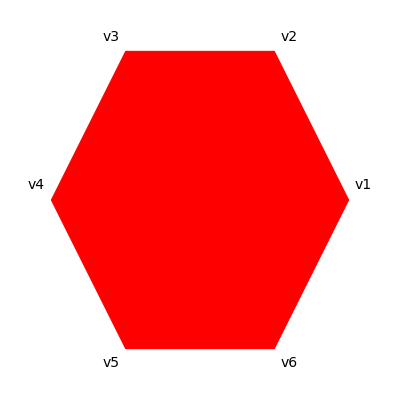
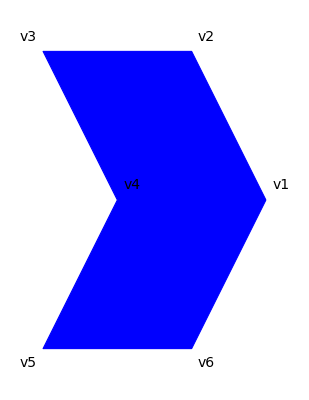
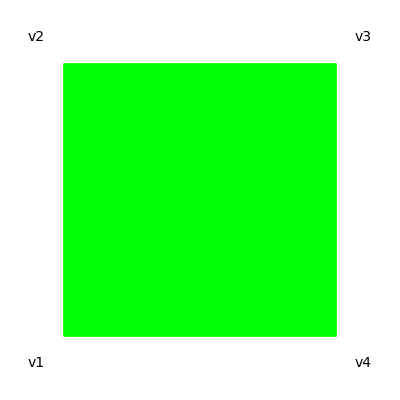
convexHexagon | concaveHexagon | square
-Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{
{"convexHexagon","concaveHexagon", "square"},
{plotPoly[convexHexagon, Red], 
plotPoly[concaveHexagon, Blue], 
plotPoly[square, Green]}
},Frame->All]
```

We will adopt a very important convention with regard to how we list polygon vertices:

Convention: Polygon vertexes are always listed in an anti-clockwise order.

In other words, if you  step from one vertex to the next, the interior of the polygon is always on your left hand side. This anti-clockwise convention is very important, as we will see shortly when we come to calculate polygon areas. This convention is the basis of most computational geometry algorithms.

Now that we know how to represent polygons we can begin to investigate their properties. We will start with the simplest polygon - the triangle.

## Triangles

We have already defined a triangle above:

Triangle: a three-sided simple, convex polygon.

In the Wolfram Language we will represent a triangle as a List of three points. For example:

```mathematica
t1 = {{0,0}, {4,0}, {0,4}}
```

{{0,0},{4,0},{0,4}}

Here is a test function to detect triangles:

```mathematica
trianglePattern :={ _?pointQ, _?pointQ, _?pointQ }

triangleQ[ t_ ] := MatchQ[ t, trianglePattern ]
```

Here is a graphics function, triangleGraphic to provide the Graphics commands to draw a triangle:

```mathematica
triangleGraphic[ {a_,b_,c_}, labels_List:{"a", "b", "c" }, offset_List:{0.4,0.4}] := {
Red,Arrow[{a, b}],
Blue,Arrow[{b, c}],
Green,Arrow[{c, a}],
Black, pointLabels[{a,b,c}, labels, offset]
}
```

As usual, we need to pass this function to a Graphics function in order to execute the commands and draw a triangle:

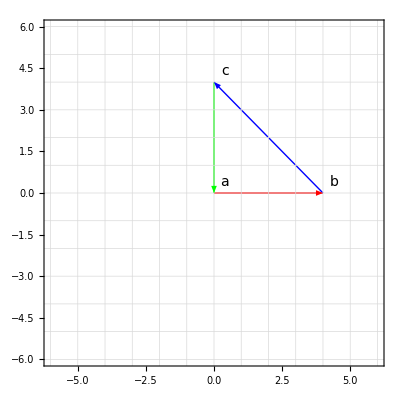

```mathematica
Graphics[triangleGraphic[t1], standardPlotStyle]
```

It is also useful to define Lists of triangles:

```mathematica
triangleListQ[ triangleList_ ] := MatchQ[ triangleList, {trianglePattern..}]
```

For example:

```mathematica
triangleQ[t1]
```

True

```mathematica
triangleListQ[{t1, t1, t1}]
```

True

## Signed area of a triangle

A key function in Computational Geometry is a function that gives the signed area of a 2D triangle that is positive if the vertexes are given in an anti-clockwise order, and negative if they are given in a clockwise order.

Because this function is so important, we will spend some time developing it. We will start in 3D, because that is the basis of the 2D function, and then define a flexible and efficient 2D function.

In 3D space, area of triangle T_(3D) with vertexes a, b, c and edge vectors v⃗ = b - a and w⃗ = c - a  (see diagram above) is given by:

A(T_(3D)) = 1/2| v⃗ × w⃗ |

We can easily translate this into a function as follows:

```mathematica
triangleArea[ a_?point3DQ,b_?point3DQ,c_?point3DQ] :=0.5Norm[ (b - a) × (c - a) ]
```

So the area of a triangle in 3D space is half the Norm of the cross product of the two edge vectors. The Norm of a vector is defined as the square root of the sum of the squares of its x, y and z values as follows:

Norm[{x, y, z}] = √(Abs[x]^2+Abs[y]^2+Abs[z]^2)

Taking the positive root, we get an area that is always positive. That's not really what we want, but we can easily modify the formula to give a signed triangle area for 2D triangles. Firstly, we set the z coordinates for the points in our 3D triangle to zero to put the triangle in the XY plane. Next, we need expressions for the x, y and z coordinates of the cross product v⃗ × w⃗ . The Wolfram Language is a symbolic language, so we will let it calculate these for us. We have put the code in a Block so we can use local variables rather than pollute the global namespace:

```mathematica
Block[{a,b,c,v,w,ax,bx,cx,ay,by,cy},
(* Set up the points for our triangle in the XY plane *)
a = {ax, ay, 0};
b = {bx, by, 0};
c = {cx, cy, 0};
(* Calculate the edge vectors v and w *)
v = b - a;
w = c - a;
(* Print out the cross product *)
Print[ "v x w = ", v × w ];
(* Print out the norm of the cross product *)
Print[ "Norm[v × w] = ", Norm[v × w] ];
]
```

v x w = {0,0,-ay bx+ax by+ay cx-by cx-ax cy+bx cy}

Norm[v × w] = Abs[-ay bx+ax by+ay cx-by cx-ax cy+bx cy]

The cross product of two vectors is a vector perpendicular to both of them. In this case the edge vectors are in the XY plane, therefore any vector perpendicular to both of these must have x = y = 0, and you can see this clearly in the calculation above. Applying the formula for Norm to this vector gives us a result that is just the absolute value of its z coordinate because x and y are zero. Therefore, if we want a signed value, we just take the signed value of the z coordinate and ignore the Abs. This allows us to calculate the signed area for a 2D triangle as follows:

A(T_(2D)) = 1/2(-a_y b_x+a_x b_y+a_y c_x-b_y c_x-a_x c_y+b_x c_y)

We can write the following function to calculate the signed area of a 2D triangle. Notice how we have used argument destructuring to get direct access to the x and y coordinates of the three points:

```mathematica
triangleArea[ {ax_?NumberQ, ay_?NumberQ}, {bx_?NumberQ, by_?NumberQ}, {cx_?NumberQ, cy_?NumberQ} ] := 0.5(-ay  bx+ax  by+ay  cx-by  cx-ax  cy+bx  cy)

triangleArea[ {a_?pointQ, b_?pointQ, c_?pointQ} ] := triangleArea[a,b,c]
```

This function performs well because we use the expansion for the Z component of v × w rather than have the Wolfram Language do the calculation every time.

Here is an interactive test program that demonstrates the triangleArea[...] function:

```mathematica
testTriangleArea[] := Manipulate[
Module[{at},
Graphics[
{at = triangleArea[ t ];
Which[ 
at >0, l="a,b,c anti-clockwise, area = ", 
at<0, l = "a,b,c clockwise, area = ", 
at == 0, l = "Collinear, area = "
];
triangleGraphic[ t ],
Text[Style[Row[{l ,at}] , Blue, 14], {0,5.5}]
},standardPlotStyle
]
], 
{{t, {{-2,3}, {-2,-1}, {2,-1}}},{-5, -5}, {5,5}, 1, Locator}, 
FrameLabel -> "Test function triangleArea"
]

testTriangleArea[]
```

-Graphics-

## 2D triangle area by determinants

Another way to express the A(T_(2D)) is as half the determinant of a matrix comprising x, y and z coordinates where the z coordinates are set to 1:

A(T_(2D))=1/2 Abs[(a_x | a_y | 1
b_x | b_y | 1
c_x | c_y | 1)]

We can easily demonstrate that this is the case if, once again we get the Wolfram Language to do a bit of symbolic work for us:

```mathematica
Block[{ax, ay, bx, by, cx, cy},
Det[{
{ax, ay, 1},
{bx, by, 1},
{cx, cy, 1}
} ]/2 ]
```

1/2 (-ay bx+ax by+ay cx-by cx-ax cy+bx cy)

This is the same result we achieved above from cross products. We can express the determinant form very directly in the Wolfram Language, and you often find this implementation in use, even though, as we will see, it is not the fastest:

```mathematica
triangleArea2DDeterminant[{ax_, ay_}, {bx_, by_}, {cx_, cy_}] := 
Det[{
{ax, ay, 1},
{bx, by, 1},
{cx, cy, 1}
} ]/2
```

In fact, as is shown below, this function is about 4 times slower than the triangleArea[...] function where the cross product is already expanded:

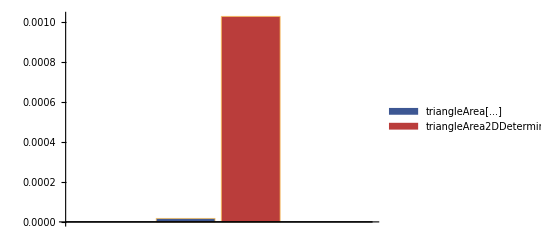

```mathematica
BarChart[{
AbsoluteTiming[triangleArea[ {0,0}, {1,0}, {1,1} ]] // First,
AbsoluteTiming[triangleArea2DDeterminant[ {0,0}, {1,0}, {1,1} ]] // First
},ChartLegends->{"triangleArea[...]","triangleArea2DDeterminant[...]"},
ChartStyle->"DarkRainbow"
]
```

Interestingly, in Mathematica 12, our slowest function, triangleArea2DDeterminant[...] is still about three times faster than using native facilities and applying the Wolfram Language Area[...] function to a Triangle Region. It’s also worth pointing out that the Area[...] function does not return a signed triangle area, so it is pretty useless for computational geometry algorithms.

Now that we have function triangleArea[...] to determine the signed area of a triangle, we can use this function to develop the next most fundamental algorithms of computational geometry - those that determine the relationships of points to lines.

## Triangles and the relationships of points to lines

If we consider a triangle as comprising a directed line segment a b and a point c, then the signed triangle area tells us about the relationship between point c and the line L defined by a b:

If the area of the triangle a b c is > 0, then point c is to the left of line L (as you travel from a to b). Otherwise it is to the right.

If the area of the triangle a b c is ≥ 0 then point c is to the left of the line L or collinear with it.

If the area of the triangle a b c is 0 then point c is collinear with the line L.

You can verify these rules for yourself by playing about with the signed triangle area demonstration program above.

We can now define the following functions:

```mathematica
leftQ[ a_?pointQ, b_?pointQ, c_?pointQ ] := triangleArea[a, b, c] >0

collinearQ[ a_?pointQ, b_?pointQ, c_?pointQ ] := triangleArea[a, b, c] ==0

leftOnQ[a_?pointQ, b_?pointQ, c_?pointQ ] := triangleArea[a, b, c] >=0
```

For completeness, we can also define rightQ and rightOnQ (we won’t need to use them):

```mathematica
rightQ[ a_?pointQ, b_?pointQ, c_?pointQ ] := !leftOnQ[ a,b,c]

rightOnQ[ a_?pointQ, b_?pointQ, c_?pointQ ] := !leftQ[a,b,c]
```

There are a couple of very important points to note about these functions:

You should clearly distinguish between the line L defined by the line segment a b and the line segment a b itself. Remember that lines have infinite length, so point c does not need to be between a and b for these functions to return True - they work over the infinite length of the line.

It is very important to keep in mind what “left” actually means in this context: if you are traveling along the line from a to b, then “left” means on your left hand side.

## Collinearity and general position

Given the collinearQ[...] function, we can now write a simple test for general position for a point set. We simply take all subsets of the point set that have cardinality 3, and if none of these is collinear, then the point set is in general position:

```mathematica
generalPositionQ[ pts_?pointListQ ] := Select[ Subsets[ pts, {3}],collinearQ[#[[1]], #[[2]], #[[3]]]&, 1 ] == {}
```

We can use this test to write a simple function to generate a random point set in general position:

```mathematica
randomPointSetGP[ n_Integer, range_:Range[-5,5]] := Module[{pts },
pts = randomPointSet[ n , range];
While[ 
!generalPositionQ[ pts ],
pts =  randomPointSet[ n , range];
];
pts
]
```

We’ll use this function quite a lot later.

## Between

Another very important relationship we need to test for is “between” - is point c is between points a and b? By “between”, we mean that c is somewhere on the line segment a b. This breaks down into two considerations: firstly, for c to be between a and b it is necessary (but not sufficient) that it is collinear with a and b. Secondly, it must not be off either end of a b. We can break this second constraint down by x and y coordinates as follows: c_x must be between a_x and b_x AND c_y must be between a_y and b_y:

(a_x ≤ c_x ≤b_x OR b_x ≤c_x ≤a_x) AND (a_y ≤ c_y ≤b_y OR b_y ≤c_y ≤a_y)

We can write a helper function, betweenOnAxisQ[...], to deal with this constraint. This function takes either the X or Y coordinates of a, b, and c as arguments.

```mathematica
betweenOnAxisQ[axy_, bxy_, cxy_]:= (axy ≤ cxy ≤ bxy) || (axy≥ cxy ≥ bxy)
```

It is then easy to write the function betweenQ[...] that returns True if c is between a and b:

```mathematica
betweenQ[ a_?pointQ, b_?pointQ, c_?pointQ ] := Which[
(* If a,b,c are not collinear, then c can't be between a and b *)
!collinearQ[ a,b,c], False,
(* If ax ≠ bx, check the betweenness of c on X *)
a[[x]]!= b[[x]], betweenOnAxisQ[a[[x]], b[[x]], c[[x]]],
(* If ax = bx, check the betweenness of c on Y *)
a[[x]] == b[[x]], betweenOnAxisQ[ a[[y]], b[[y]], c[[y]]]]
```

## Testing the point/line relationship functions

Here is a test program for the functions that work with a single point c:

```mathematica
testPointRelationships[] := Manipulate[
Graphics[
{Blue, Arrow[ {a, b}],
If[leftQ[a,b,c], Green, Red],Text[Style["leftQ",14], c - {0,0.5}],
If[rightQ[a,b,c], Green, Red],Text[Style["rightQ",14], c - {0,1}],
If[leftOnQ[a,b,c], Green, Red],Text[Style["leftOnQ",14], c - {0,1.5}],
If[rightOnQ[a,b,c], Green, Red],Text[Style["rightOnQ",14], c - {0,2}],
If[collinearQ[a,b,c], Green, Red],Text[Style["collinearQ",14], c + {0,.5}],
If[betweenQ[a,b,c], Green, Red],Text[Style["betweenQ",14], c + {0,1}],
Black, Text[Style["c",16], c + {0.5,0}],
pointLabels[{a,b}, {"a", "b"}]
},
standardPlotStyle
],
{{a, {-4,-4}},{-5,-5}, {5,5}, 1, Locator}, 
{{b,{4,4}}, {-5,-5}, {5,5}, 1, Locator}, 
{{c, {2,-2}}, {-5,-5}, {5,5}, 1, Locator}, 
"betweenQ: True if c is on the line a b",
"collinearQ: True if c collinear with the line a b",
"leftQ: True when c is on your left hand side when traversing the line a b" ,
"leftOnQ: True when c is on your left hand side when traversing the line a b OR collinear with a b" ,
FrameLabel ->"Test functions betweenQ, collinearQ, leftQ and leftOnQ"
]

testPointRelationships[]
```

-Graphics-

## Relationship between a list of points and a line

We can create versions of these functions that instead of taking a single point c, take a List of points, l. These functions return True if the condition holds for all of the points. We do this by mapping the existing functions over the collection of points, and ANDing the results together:

```mathematica
leftQ[ a_?pointQ, b_?pointQ, l_?pointListQ ]:= And @@ (leftQ[ a, b, #]&/@l)

leftOnQ[ a_?pointQ, b_?pointQ, l_?pointListQ ]:= And @@ (leftOnQ[ a, b, #]&/@l)

rightQ[ a_?pointQ, b_?pointQ, l_?pointListQ ]:= And @@ (rightQ[ a, b, #]&/@l)

rightOnQ[ a_?pointQ, b_?pointQ, l_?pointListQ ]:= And @@ (rightOnQ[ a, b, #]&/@l)

betweenQ[ a_?pointQ, b_?pointQ, l_?pointListQ ]:= And @@ (betweenQ[ a, b, #]&/@l)
```

Here is a demo program that tests the these functions:

```mathematica
testListRelationships[] := Manipulate[
Module[{poly},
poly = {c1, c2, c3, c4};
Graphics[
{Blue, Arrow[ {a, b}],
If[betweenQ[a,b,poly], Green, Red],Text[Style["betweenQ",14], {0,4.5}],
If[leftQ[a,b,poly], Green, Red],Text[Style["leftQ",14], {-1,5.5}],
If[leftOnQ[a,b,poly], Green, Red],Text[Style["leftOnQ",14], {1,5.5}],
If[rightQ[a,b,poly], Green, Red], Text[Style["rightQ",14], {-1,5}],
If[rightOnQ[a,b,poly], Green, Red],Text[Style["rightOnQ",14], {1,5}],
Line[poly],
Black,pointLabels[{a,b}, {"a", "b"}]
},standardPlotStyle
]
],
{{a, {-4,-4}},{-5,-5}, {5,5}, 1, Locator}, 
{{b,{4,4}}, {-5,-5}, {5,5}, 1, Locator}, 
{{c1, {2,-2}}, {-5,-5}, {5,5}, 1, Locator}, 
{{c2, {2,-1}}, {-5,-5}, {5,5}, 1, Locator}, 
{{c3, {2,-0}}, {-5,-5}, {5,5}, 1, Locator}, 
{{c4, {2,1}}, {-5,-5}, {5,5}, 1, Locator}, 
"leftQ: True when the chain is on your left hand side when traversing the line a b" ,
"leftOnQ: True when the chain is on your left hand side when traversing the line a b OR collinear with a b" ,
"rightQ: True when the chain is on your right hand side when traversing the line a b" ,
"rightOnQ: True when the chain is on your right hand side when traversing the line a b OR collinear with a b" ,
"betweenQ: True when the all the chain vertexes are somewhere on the line segment a b" ,
FrameLabel ->"Test List functions leftQ, leftOnQ, rightQ and rightOnQ"
]

testListRelationships[]
```

-Graphics-

## Points on the same side of a line

Sometimes all we need to know is whether a set of points all lie in the same open half plane (points on the line not included) or closed half plane (points on the line included) defined by a line segment l_1 l_2. We can write the following functions to test for this:

```mathematica
sameSideQ[ l1_?pointQ, l2_?pointQ, points_?pointListQ ] := leftQ[l1, l2, points] || rightQ[l1, l2, points]

sameSideOnQ[ l1_?pointQ, l2_?pointQ, points_?pointListQ ] := leftOnQ[l1, l2, points] || rightOnQ[l1, l2, points]
```

Here is a test program. The line is green when the selected sameSideQ[...] or sameSideOnQ[...] function returns True, otherwise it is red. Note the difference between sameSideQ[...] and sameSideOnQ[...]:

```mathematica
sameSideTest[] := Manipulate[
Module[{points},
points = {p1, p2, p3, p4, p5};
Graphics[{
If[test[l1, l2, points], Green, Red],
Arrow[ {l1, l2} ]
},standardPlotStyle
]
], 
{test, {sameSideQ, sameSideOnQ}},
{{l1,{-4,0}},{-5, -5}, {5,5}, 1, Locator},
{{l2,{4,0}},{-5, -5}, {5,5}, 1, Locator},
{{p1, {-3,2}},{-5, -5}, {5,5}, 1, Locator}, 
{{p2, {-2,2}},{-5, -5}, {5,5}, 1, Locator}, 
{{p3, {-1,2}},{-5, -5}, {5,5}, 1, Locator}, 
{{p4, {0,2}},{-5, -5}, {5,5}, 1, Locator}, 
{{p5, {1,2}},{-5, -5}, {5,5}, 1, Locator}, 
FrameLabel -> "Test function sameSideQ and sameSideOnQ"
]

sameSideTest[]
```

-Graphics-

## Summary

Triangles are the key to computational geometry. They allow us to discover relationships between points and lines by forming them into triangles and considering the signed triangle areas. These relationships are the building blocks for the more complex algorithms we will introduce in subsequent chapters. Always remember that for our algorithms to work, we need to adhere to our convention that polygon vertexes always go in an anticlockwise order.

## Chapter 4: Triangle geometry

In this chapter, we will take a more detailed look at the geometry of triangles, consider how to triangulate a triangle on an internal point and create random triangles. These are all things we will find useful in the more complex algorithms we present later.

## The centroid, medians and circumcircle of a triangle

We will continue this chapter by considering some of the properties of triangles. Here are some definitions:

Median of a triangle: a line joining a vertex to the midpoint of the opposite side, where the midpoint of a side is the mean of its two vertexes.

Centroid (or geometric center) of a triangle:

Its center of gravity. If you were to cut the triangle out of a material of uniform thickness and density, you could balance it on its centroid.

The intersection of its three medians.

The mean of the coordinates of its three vertexes.

Circumcircle of a triangle: the circle that goes through all three triangle vertexes.

Here is a fast algorithm from [ORourke2] to calculate the center and radius of the circumcircle of a triangle:

```mathematica
circumcircle[ {v1_, v2_, v3_} ] :=Block[{a,b,c,d,e,f,g, maxX, minX,maxY, minY, dX, dY, center},
{a,b} = v2 - v1;
{c,d} = v3 - v1;
e = a (v1+ v2)[[x]] + b (v1+ v2)[[y]];
f = c (v1+ v3)[[x]] + d (v1 + v3)[[y]];
g = 2 ( a (v3-v2)[[y]] - b (v3 - v2)[[x]]);     
If [ g ==0,
(* The points are collinear - just find extremes and midpoint *)
minX = Min[ v1[[x]], v2[[x]], v3[[x]] ];
maxX = Max[ v1[[x]], v2[[x]], v3[[x]] ];
minY = Min[ v1[[y]], v2[[y]], v3[[y]] ];
maxY = Max[ v1[[y]], v2[[y]], v3[[y]] ];
dX = (maxX- minX)/2;
dY = (maxY- minY)/2;
center = Mean[{{minX, minY},{maxX, maxY}}],
(* The points are not collinear *)
center = {d e - b f ,a f - c e }/g;
{dX, dY} = center - v1;
];
{center, Sqrt[dX^2 + dY^2]}
]
```

Here is a function to test if a point is strictly inside (i.e. not on the perimeter) of the circumcircle [WikiBooks1]:

```mathematica
inCircumcircleQ[ {a_, b_, c_}, d_?pointQ ] := Det[{
{a[[x]], a[[y]], a[[x]]^2 + a[[y]]^2, 1},
{b[[x]], b[[y]], b[[x]]^2 + b[[y]]^2, 1},
{c[[x]], c[[y]], c[[x]]^2 + c[[y]]^2, 1},
{d[[x]], d[[y]], d[[x]]^2 + d[[y]]^2, 1}
}] > 0
```

Here is a demo program to illustrate these functions:

```mathematica
testTriangleCentroidCircumcircleAndMedian[] := Manipulate[
Module[{t, cir},
t = {a,b,c};
cir = circumcircle[t];
Graphics[
{
(* Sides *)
triangleGraphic[ t, {"a", "b", "c"}, {0.4, 0.4} ],
(* Medians *)
Black, Line[{t[[1]], Mean[{t[[2]],t[[3]]}]}], 
Black, Line[{t[[2]], Mean[{t[[1]],t[[3]]}]}],
Black, Line[{t[[3]], Mean[{t[[2]],t[[1]]}]}],
(* Centroid *)
Purple,Circle[Mean[t], 0.2],
Disk[ cir[[1]], 0.1],
(* Circumcircle *)
Circle[cir[[1]], cir[[2]]],
(* Point in circumcircle *)
If [ inCircumcircleQ[ t, pt],Green,Red],
Disk[ pt,0.4]
},standardPlotStyle
]
], 
{{a, {-2,3}},{-5, -5}, {5,5}, 1, Locator}, 
{{b, {-2,-1}},{-5, -5}, {5,5}, 1, Locator},
{{c, {2,-1}},{-5, -5}, {5,5}, 1, Locator},
{{pt, {4,4}},{-5, -5}, {5,5},1, Locator},
FrameLabel -> "Medians and centroid"
]

testTriangleCentroidCircumcircleAndMedian[]
```

-Graphics-

## The internal angles of a triangle

It is often useful to be able to calculate the internal angles of a triangle from its coordinates. We will see later that we can use these angles to calculate an angle vector that allows us to compare different triangulations.

Finding the internal angles reduces to a problem of finding the angle between two vectors. We can do this using the dot product. The dot product of two vectors A⃗  and B⃗ is:

A⃗ ·B⃗ = |A⃗ | |B⃗| cos θ

where θ is the angle between the vectors.

Rearranging, θ is given by:

θ = cos^-1 ((A⃗ · B⃗)/(|A⃗||B⃗|))

The function is trivial, and the Wolfram language already has the built-in function VectorAngle to calculate it, so we won’t bother to implement it here.

We can now write a function to calculate the internal angles of a triangle:

```mathematica
internalAngles[ {a_,b_,c_}?triangleQ ] := 
{
VectorAngle[b - a,c  - a],
VectorAngle[a - b, c - b], 
VectorAngle[a - c, b - c]
}
```

Here is a demo program:

```mathematica
testInternalAngles[] := Manipulate[
Module[{t, angles},
t = {a,b,c};
angles = internalAngles[t];
Graphics[
{
(* Sides *)
triangleGraphic[ t, 
{Row[{"∠a = ", N[angles[[1]]/Degree],"°"}], 
Row[{"∠b = ", N[angles[[2]]/Degree],"°"}],
Row[{"∠c = ", N[angles[[3]]/Degree],"°"}]
}
, {0.4, 0.4} ]
},standardPlotStyle
]
], 
{{a, {-2,3}},{-5, -5}, {5,5}, Locator}, 
{{b, {-2,-1}},{-5, -5}, {5,5},Locator},
{{c, {2,-1}},{-5, -5}, {5,5}, Locator},
FrameLabel -> "Internal angles"
]

testInternalAngles[]
```

-Graphics-

## Triangulating a triangle on an internal point

If there is a point o strictly inside triangle a b c (i.e. not on an edge or vertex), we can use that point to split the triangle into three smaller triangles, a b o, b c o and c a o simply by joining the point to each vertex. As it turns out, this can be a very useful thing to do. We will see an example later when we use this function to help triangulate a point set.

If point o is strictly internal to triangle a b c, we can calculate the three new triangles as follows:

```mathematica
triangulateOnPoint[ {a_,b_,c_}, o_]:={{a,b,o}, {b,c,o}, {c,a,o}}
```

This function doesn’t check to see if o really is internal to the triangle so beware - garbage in, garbage out! Here is a test program:

```mathematica
testTriangulateOnPoint[ ] := Manipulate[
Module[{trs, tr },
tr  = {a,b,c};
trs = triangulateOnPoint[tr, pt];
Graphics[{
Black,If[ triangle, 
Arrow[{{tr[[1]], tr[[2]]},{tr[[2]], tr[[3]]},{tr[[3]], tr[[1]]}}]],
pointLabels[Join[tr, {pt}], {"a", "b", "c", "o"}, {0.3, 0.3}],

Red,If [ abo,{Arrow[pchainEdges[trs[[1]]]], Opacity[ 0.1],Polygon[trs[[1]]]} ],
Blue,If [ bco,{Arrow[pchainEdges[trs[[2]]]], Opacity[ 0.1],Polygon[trs[[2]]]} ],
Green,If [ cao,{Arrow[pchainEdges[trs[[3]]]], Opacity[ 0.1],Polygon[trs[[3]]]} ]
}, standardPlotStyle
]
],
{{a, {-2,3}},{-5, -5}, {5,5},1, Locator}, 
{{b, {-2,-1}},{-5, -5}, {5,5},1, Locator}, 
{{c, {2,-1}},{-5, -5}, {5,5},1, Locator}, 
{{pt, {0,0}},{-5, -5}, {5,5},1, Locator}, 
{{triangle, True, "triangle"}, {True, False}},
{{abo, False, "abo"}, {True, False}},
{{bco, False, "bco"}, {True, False}},
{{cao, False, "cao"}, {True, False}}
]

testTriangulateOnPoint[]
```

-Graphics-

## Random triangles

In order to help construct examples, we find it useful to have a function that generates random triangles. For convenience, we will generally work on a 10x10 grid, and use triangles that have integers for their vertexes.

At first, it seems as though we could just select any three unique points from our 10x10 grid, and that would give us a random triangle:

```mathematica
RandomSample[Permutations[Range[-5,5], {2}], 3]
```

{{-4,3},{1,-5},{-4,-1}}

However, there is a problem with this algorithm - because the three vertexes are selected randomly, there is a chance that they might be collinear. In which case, we don’t get a random triangle, we get a random straight line! A simple algorithm for a randomTriangle function is:

Generate a random triangle with three unique points

If it has a non-zero area, return the triangle else try again

Here is an implementation:

```mathematica
randomTriangle[] := Module[{t = RandomSample[Permutations[Range[-5,5], {2}], 3]}, 
While[
collinearQ[ t[[1]], t[[2]], t[[3]] ], t = RandomSample[Permutations[Range[-5,5], {2}], 3]
];
t]
```

Here is a simple demo program. Each time you run the program, you should get a new random triangle:

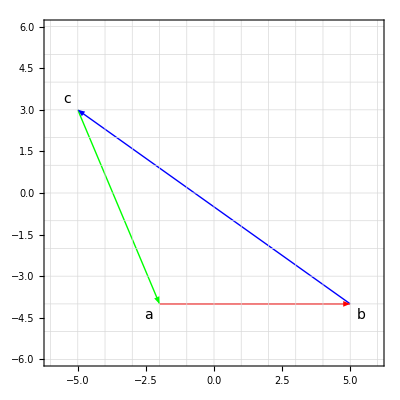

```mathematica
Graphics[ triangleGraphic[ randomTriangle[] ],standardPlotStyle ]
```

## Summary

In this chapter we considered some other properties of the triangle: the centroid, medians, circumcenter, circumcircle and internal angles. We also saw how to triangulate a triangle on an internal point, which will be very useful later! Finally, we saw how to create random triangles.

## Chapter 5: Polygons

It’s easy to work with triangles because they only have three vertexes. More generally, a polygon has >3 vertexes and we will need a way to access and traverse them. Furthermore, because a polygon is a closed curve, we will generally need to use a cyclic ordering of vertexes.

## Polygon vertex navigation

For a polygon with vertexes v_1, v_2, ... v_n, the edges are:

v_1 v_2, v_2 v_3, ... v_(n-1)v_n, v_n v_1

You can see how the edge vertexes cycle from v_n back to v_1.

In [ORourke1] the author defines a polygon as a circular linked list. This means that when you step along the list from the beginning to the end, you don’t stop at the end - you cycle back to the beginning. This is a very natural and convenient representation of a polygon in languages such as C and Java. As we have already said, in the Wolfram Language (and other Lisp-like languages) the List is the natural representation for any collection of items, including a polygon. It is easy to make polygon navigation functions that make our List based representation behave in the same way as a circular linked list. All we have to do is to ensure that the number we use to index into the List behaves in a cyclic fashion. If Wolfram Language arrays were zero based, we could just take Mod[n, numVertexes]. However, because they are 1 based, we have to take this into account as follows:

```mathematica
polyIndex[numVertexes_Integer, i_Integer] :=Mod[i - 1,numVertexes] + 1
```

When we use index values that are out of range, applying polyIndex keeps them cycling between 1 and n. The top row is the index, and the bottom row is the corresponding vertex:

```mathematica
Grid[ {Range[-10,10],polyIndex[ 5, #] &/@ Range[-10,10]}, Frame -> All]
```

-10 | -9 | -8 | -7 | -6 | -5 | -4 | -3 | -2 | -1 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
5 | 1 | 2 | 3 | 4 | 5 | 1 | 2 | 3 | 4 | 5 | 1 | 2 | 3 | 4 | 5 | 1 | 2 | 3 | 4 | 5

Based on polyIndex[...] we can write two navigation functions,  polyPrevIndex[...] and polyNextIndex[...]. These allow us, given an index i, to navigate to the previous (i -1) and next (i + 1) indexes respectively, always cycling when the index gets out of range (i > n):

```mathematica
polyPrevIndex[ numVertexes_Integer, i_Integer] := polyIndex[numVertexes, i-1]

polyNextIndex[ numVertexes_Integer, i_Integer] := polyIndex[numVertexes, i+1]
```

The actual vertexes are obtained by using the indexes on the polygon List:

```mathematica
polyVertex[poly_?pointListQ, i_Integer] := poly[[  polyIndex[Length[poly], i] ]]

polyPrevVertex[poly_?pointListQ, i_Integer] := poly[[  polyPrevIndex[Length[poly], i] ]]

polyNextVertex[poly_?pointListQ, i_Integer] := poly[[  polyNextIndex[Length[poly], i] ]]
```

Here is a simple test program for the polygon navigation functions:

```mathematica
testPolygonNavigation[poly_List] :=DynamicModule[ {currentIndex = 1, len = Length[poly]},
Manipulate[
Graphics[ 
{
Green, Polygon[poly],
Black, polyVertexLabels[poly],
Red, Circle[ poly[[currentIndex]], 0.5]
},
standardPlotStyle,
FrameLabel -> "Functions polyPrev and polyNext"
],
Button["Next", currentIndex =polyNextIndex[len, currentIndex] ],
Button["Previous", currentIndex =polyPrevIndex[len, currentIndex] ]
]
]

testPolygonNavigation[concaveHexagon]
```

-Graphics-

Another useful function is one that returns a set of three polygon vertex indexes i_(j-1), i_j, i_(j+1). In other words, the previous index, the index itself and the next index:

```mathematica
polyTake3Index[ numVertexes_Integer, i_Integer ] := {polyPrevIndex[numVertexes, i], 
polyIndex[numVertexes,i], polyNextIndex[numVertexes,i]}
```

This function gives us a set of three consecutive polygon vertexes:

```mathematica
polyTake3[ poly_?pointListQ, i_Integer ] := vertexes[ poly,polyTake3Index[Length[poly],i]]
```

We can test these functions with this program:

```mathematica
testPolyTake3FromHexagons[ poly_?pointListQ ] := 
Manipulate[ Graphics[
{Opacity[0.5],
Red, If [v1, Polygon[polyTake3[ poly, 1]] ],
Blue, If[v2, Polygon[polyTake3[ poly, 2]] ],
Green, If[v3,Polygon[polyTake3[ poly, 3]] ],
Yellow, If[v4,Polygon[polyTake3[ poly, 4]] ],
Cyan, If[v5,Polygon[polyTake3[ poly, 5]] ],
Purple, If[v6, Polygon[polyTake3[ poly, 6]]],
Black,polyVertexLabels[poly]
}, ImageSize ->Small],
{{v1, True, "v1"}, {True, False}},
{{v2, False, "v2"}, {True, False}},
{{v3, True, "v3"}, {True, False}},
{{v4, False, "v4"}, {True, False}},
{{v5, False, "v5"}, {True, False}},
{{v6, False, "v6"}, {True, False}},
ControlPlacement -> Left
]

Grid[{
{"convexHexagon", "concaveHexagon"},
{testPolyTake3FromHexagons[convexHexagon],testPolyTake3FromHexagons[concaveHexagon]}
}, Frame->All]
```

-Graphics-

The next navigation function gives a range of consecutive polygon indexes. For example, the index range from 4 to 2 for a six sided polygon is {4, 5, 6, 1, 2} if we walk around the polygon by increasing the index. However, we may also decrement the index to go around the polygon the other way. In that case the decremented range is {4, 3, 2}. This is a form of modular, or clock arithmetic where the numbers wrap around after a certain value called the modulus that in this case the number of polygon vertexes. You can see modular arithmetic very clearly on any 24 hour clock - there are 24 vertexes, and if, for example, we start at vertex 23  (11 pm) and add 2 hours, we get back to vertex 1 (1 am). Similarly, we can subtract 2 hours from 1am (vertex 1), and we get to 11 pm (vertex 23). The only complication in this analogy, is that the “vertexes” on a 24 hour clock face are numbered clockwise, whereas we have adopted the standard convention that polygon vertexes are numbered anti-clockwise. Of course, this is just a presentation matter that makes no difference to the actual calculation.

We can write two new range functions that implement ranges in modular arithmetic. Both functions calculate an inclusive consecutive range of integers between from and to where the numbers wrap around at the integer modulus. The first function returns a range where the numbers are increasing and the second a range where the numbers are decreasing.

```mathematica
(* Returns an inclusive increasing range between from and to that wraps at modulus *)
modRangeUp[modulus_Integer, from_Integer, to_Integer] :=Which[
from == to, {},
to > from, Range[from, to],
to < from, Join[Range[from, modulus], Range[1, to]]
]

(* Returns an inclusive decreasing range between from and to that wraps at modulus *)
modRangeDown[modulus_Integer, from_Integer, to_Integer] :=Which[
from == to, {},
to > from, Join[Range[from, 1, -1],Range[modulus, to, -1]],
to < from, Range[from, to, -1]
]
```

Here is a test function for our modular arithmetic range functions:

```mathematica
testModRange[] := 
 Manipulate[
Module[{rangeUp, rangeDown},
rangeUp :=modRangeUp[modulus, from, to];
rangeDown :=modRangeDown[modulus, from, to];
Graphics[
Text[
Style[ Grid[{
{"Modulus ", modulus," range up",rangeUp},
{"Modulus ", modulus," range down",rangeDown}
}],FontSize->Medium]
]
]
], 
{{modulus,5}, {1,2,3,4,5,6,7,8,9,10}, SetterBar},
{{from,1}, Range[1, modulus], SetterBar},
{{to,1}, Range[1, modulus], SetterBar},
FrameLabel -> "Test functions modRangeUp and modRangeDown"
]

testModRange[]
```

-Graphics-

We can package up this pair of functions into a utility function called polyIndexRange[...] that returns a range of polygon vertex indexes, either increasing (dir = True) or decreasing (dir = False):

```mathematica
polyIndexRange[ length_Integer, from_Integer, to_Integer, dir_:True] := If[ dir,
modRangeUp[length, from, to],
modRangeDown[length, from, to]
]
```

And to get the vertexes:

```mathematica
polyVertexRange[ poly_?pointListQ, from_Integer, to_Integer , dir_:True] :=  vertexes[ poly, polyIndexRange[ Length[poly], from, to, dir] ]
```

Here is an interactive test program:

```mathematica
testPolyIndexRange[poly_?pointListQ] :=DynamicModule[ {len = Length[poly], inc, dec, from, to},
Manipulate[
Graphics[ 
{
LightBlue, Polygon[poly],
Blue, polyVertexLabels[poly],
If[ up, 
{Green, Arrow[ polyVertexRange[poly, from, to] ], 
Text[Style[polyIndexRange[len,from, to ], 14], {0,5.5}]}
],
If[ down, 
{Red, Arrow[ polyVertexRange[poly, from, to, False] ],
Text[Style[polyIndexRange[len,from, to, False ], 14], {0,5}]}
],
Blue, Circle[ poly[[from]], 0.5 ], Text[Style["from", 14], poly[[from]]],
Blue, Circle[ poly[[to]], 0.5 ],Text[Style["to",14], poly[[to]]]
},
standardPlotStyle,
FrameLabel -> "Function polyIndexRange"
],
{{up, True}, {True, False}},
{{down,True}, {True, False}},
{{from, 1,"from"}, 1, len,1, SetterBar},
{{to, 3, "to"}, 1, len, 1,  SetterBar}
]
]

testPolyIndexRange[concaveHexagon]
```

-Graphics-

## Polygon edges

We can write a function to return all of the polygon edges v_1 v_2, v_2 v_3, ... v_(n-1)v_n, v_n v_1 using the Partition function, just like we already did for polygonal chains. However, we need to remember that as a polygon is a closed polygonal chain, we need to append the first vertex to the end of the List of polygon vertexes so that the chain joins up:

```mathematica
polyEdges[ poly_?pointListQ ] := Partition[Join[ poly, {poly[[1]]} ], 2, 1]
```

For example:

```mathematica
polyEdges[concaveHexagon]
```

{{{4,0},{2,4}},{{2,4},{-2,4}},{{-2,4},{0,0}},{{0,0},{-2,-4}},{{-2,-4},{2,-4}},{{2,-4},{4,0}}}

We can do the same for the indexes:

```mathematica
polyEdgeIndexes[ polyLength_Integer ] := Partition[Join[ Range[polyLength], {1}], 2, 1]
```

Here is a program that finds the edges of a polygon and draws each edge as a red arrow:

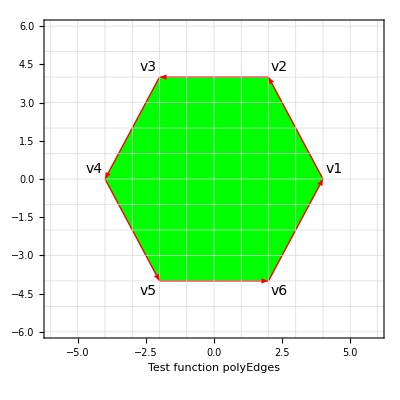

```mathematica
plotPolyEdges[ poly_?pointListQ ] := Graphics[ 
{
Green, Polygon[poly],
Red, Arrow[ polyEdges[poly] ],
Black, polyVertexLabels[poly]
},
standardPlotStyle,
FrameLabel -> "Test function polyEdges"
]

plotPolyEdges[ convexHexagon ]
```

## Regular polygons

Here is a definition:

Regular polygon: a polygon that has all angles the same (equiangular) and has all sides the same length (equilateral).

Regular polygons are perhaps more a topic for geometry than computational geometry, but we include them here, partly for completeness of our polygon taxonomy, and partly because we will shortly need to distinguish between star polygons (formed from regular polygons) and simple star shaped polygons. Here is a list of the names of the first 18 regular polygons from number of sides and vertexes n = 3...20. We have padded the List so that the List index corresponds to the number of sides of the polygon:

```mathematica
regularPolygons :={"", "", "trigon","tetragon","pentagon","hexagon","heptagon","octagon","enneagon","decagon","hendecagon","dodecagon","tridecagon","tetradecagon","pendedecagon","hexdecagon","heptdecagon","octdecagon","enneadecagon","icosagon"}
```

For a regular polygon P with n vertices, the angle θ_i between the X axis and vertex v_i (i ≤ n) is:

θ_i = (2ℼ i)/n

If the circumradius of the polygon is r, then the Cartesian coordinates of vertex v_i are:

v_i_x = r  cos θ_i

v_i_y = r  sin θ_i

Given this information, we can implement a function to generate a regular polygon with n sides and radius r as follows:

```mathematica
regularPoly[ n_Integer, r_Integer:1] := N[{ r Cos[# 2Pi/n], r Sin[# 2 Pi/n] }] &/@ Range[n]
```

Here is a short program to plot them:

```mathematica
(* Plot regular polygon by number of sides *)
drawRegularPoly[numSides_Integer, showLabel_:True] := {
Blue,
If[showLabel,
{
Style[Text[Row[{regularPolygons[[numSides ]], ", sides = " ,numSides  }]], 12],
Opacity[0.1],Polygon[ regularPoly[numSides] ] 
}
]}

(* Plot regular polygon by name *)
drawRegularPoly[name_String, showLabel_:True] := drawRegularPoly[First[FirstPosition[regularPolygons, name]], showLabel]
```

Here is a demonstration program:

```mathematica
TabView[{
"Number of sides"->Manipulate[
Graphics[
drawRegularPoly[n], 
ImageSize -> Small
],
{{n, 7,"number of sides, n"}, 3, 20, 1, SetterBar}
],
"Name"->Manipulate[
Graphics[
drawRegularPoly[name], 
ImageSize -> Small
], 
{{name, "trigon"}, regularPolygons[[3;;]]}
]
}]
```

-Graphics-

## Regular polygons with integer vertexes

As we stated earlier, we will mostly be using examples in which the points have Integer coordinates so that everything functions smoothly. But this means that we will generally not be able to use regular polygons, because the only regular polygon that can have integer coordinates for its vertexes is the square. This is quite an interesting observation, and there is a proof offered in [Klobučar1], but it is quite complex, and beyond the scope of this book. However, we can offer a much simpler informal proof using coordinate geometry:

We first observe that by suitable choice of coordinates any polygon may be drawn so that the edge, v_1v_2, is horizontal such that v_1={-1,0} and v_2={0,0}. The length of the edge is exactly 1 and we are considering regular polygons, so all other edges are also 1 by definition.

By coordinate geometry, the next vertex in the regular polygon is v_3={v_2.x + 1 cos θ,v_2.y+ 1 sin θ } = {cos θ,sin θ} where θ is the angle between the X axis and edge v_2v_3 going anticlockwise.

The only way to get one integer from another by addition is to add 0 or another integer. Therefore vertex v_3only has integer x when  cos θ∈ {0,1} and only has integer y when sin θ∈ {0,1}

When  cos θ=1, sin θ = 0,  θ=0 and the vertex v_3 = {2,0} this means that  v_1, v_2 and  v_3 are collinear, which is not allowed. When  cos θ=0, sin θ = 1,  θ=90° and the vertex v_3 = {1,1} so the regular polygon is a square. No other regular polygon satisfies the criterion of θ=90° therefore the square is the only regular polygon that can have integer coordinates.

The fact that the only regular polygon that can have integer coordinates is the square is a simple corollary of the fact that cos θ and sin θ are only integers for θ=90° or θ=0°. Here is a simple demonstration that illustrates this:

```mathematica
integerCoords[] := Manipulate[ 
Module[{v1, v2, v3},
v1 = {-1,0};
v2 = {0,0};
v3 = {Cos[theta], Sin[theta]};
Graphics[ 
{
Red,Arrow[{v1, v2}],
Blue,Arrow[{v2, v3}],
pointCoordLabels[{v3}]
},
AspectRatio->1,Axes->True,Frame->True,AxesOrigin->{0,0},
GridLines->{{-2,-1,0,1,2},{-2,-1,0,1,2}},
PlotRange->{{-2,2},{-2,2}},
FrameLabel -> "Integer coordinates"
]
],
{{theta, Pi/2}, 0, Pi}
]

integerCoords[]
```

-Graphics-

The example above illustrates quite nicely why we have chosen an Integer grid for our demonstrations: If you set theta to π  using the slider, v3 should have the value {-1, 0}, but instead it only approximates this because of rounding errors. These errors make any demonstrations that rely on the comparison of points problematic.

## Regular star polygons

Here is a definition:

Regular star polygon: a self-intersecting, equilateral equiangular polygon, created by connecting one vertex of a simple, regular polygon to another, non-adjacent vertex and continuing the process until the original vertex is reached again [Coxeter1].

For a regular polygon with n vertexes, a star polygon may be constructed by repeatedly joining vertex v_i to v_(i+m) until vertex v_(i+m) = v_i, where 2 < m  < n/2 and i  = 1... n.

It is useful to have a function to calculate the maximum value of m for any n. This must be an integer less than n/2, so if n is even, we need to subtract 1:

```mathematica
mMax[ n_Integer ] :=If[ EvenQ[n], Floor[(n-1)/2], Floor[n/2] ]
```

We can calculate the star polygon indexes and vertexes as follows:

```mathematica
starPolyIndexes[ n_Integer, m_Integer] :={polyIndex[n, #],polyIndex[n, # + m]} &/@ Range[n ]

starPoly[ poly_?pointListQ, m_Integer] := {poly[[#[[1]]]], poly[[#[[2]]]]} &/@ starPolyIndexes[Length[poly], m]
```

This program plots the regular star polygons:

```mathematica
drawStarPoly[ n_Integer, m_Integer, arrow_ ] := {
If[ arrow, Arrow, Line][starPoly[regularPoly[n], m]]
}

Manipulate[
If [skip > mMax[sides], skip = mMax[sides] ];
Graphics[{
drawRegularPoly[sides],
drawStarPoly[sides, skip, arrow]
}],
{{arrow, False, "arrow"}, {True, False}},
{{sides,12,"sides"}, 3, 20, 1},
{{skip, 5, "skip"}, 1, mMax[sides], 1}
]
```

-Graphics-

## Monotone mountain polygons

We considered monotonicity for polygonal chains earlier. We can apply the same idea to simple polygons:

Monotone mountain polygon: a simple polygon that can be split into two polygonal chains, one of which (the base) is an edge, and the other of which is monotone with respect to the base.

If polygon P has a base edge v_i v_j where j = i + 1, then it is monotone if the polygonal chain that comprises everything but the base, {v ∈ P} \ { v_i v_j}, is monotonic with respect to v_i v_j.

In terms of an algorithm to test for a monotone mountain polygon:

Remove the base vertexes from the polygon

See if the remaining polygonal chain is monotone with respect to the base

Check that the remaining polygonal chain doesn’t intersect with the base (i.e. that the original polygon is simple)

Here is a suitable implementation. Note that in order to check for non-intersection with the base, all we need to do is check that all points in the chain are in the same half plane of the base edge, i.e. they are all to the left or all to the right of it.

```mathematica
monotoneMountainQ[ poly_?pointListQ , baseEdge_Integer ] := Module[ {len,baseIndexes,baseVertexes,  pchain, pbody},
len = Length[poly];
(* the vertexes of edge ei are vi and vi+1 *)
baseIndexes ={polyIndex[len, baseEdge], polyNextIndex[len, baseEdge]};
baseVertexes =vertexes[poly, baseIndexes];
(* get the polygonal chain from one base vertex to the other *)
pchain = polyVertexRange[ poly, baseIndexes[[2]], baseIndexes[[1]]];
(* clip off the base vertexes *)
pbody = Rest[Most[pchain]];
monotoneQ[pchain, baseVertexes] && (leftQ[baseVertexes[[1]], baseVertexes[[2]],pbody] || rightQ[baseVertexes[[1]], baseVertexes[[2]],pbody])
]
```

Here is a demo program. To make a monotone mountain polygon, select a base (e.g. v1v2), stretch it out a bit, and then make sure all the other points are positioned between the two base vertexes and are on the same side of the base. The polygon will turn green when it is monotone. You can see why these are called monotone mountain polygons - they actually look a bit like mountains:

```mathematica
testMonotoneMountainQ[] := Manipulate[
Module[ 
{len, baseIndexes,baseVertexes,  pchain, isMonotonic},
len = Length[poly];
baseIndexes = {edge, polyNextIndex[len,edge]};
baseVertexes = vertexes[ poly,baseIndexes ];
pchain =polyVertexRange[ poly, baseIndexes[[2]], baseIndexes[[1]]];
isMonotonic = monotoneMountainQ[poly, edge];

Graphics[ 
{
If[ projections,{Dashed, Line[{#, projectPoint[#, baseVertexes]}] &/@ pchain}],
If[ chain,{Blue,Arrow[pchainEdges[pchain]]}],
If[ base,{Red,Arrow[baseVertexes]}],
Black, polyVertexLabels[poly, {0.3,0.3}],
If[isMonotonic, Green, Red],
Text[Style[Row[{"monotone mountain =",isMonotonic}], 14], {0, 5.5}],
Opacity[0.2],Polygon[poly]
},
standardPlotStyle]
],

{{chain,True, "chain"}, {True, False}},
{{base, True, "base"}, {True, False}},
{{projections, True, "projections"}, {True, False}},
{{edge, 1, "edge"}, 1,8, 1},
{{poly, {{5,-1}, {-2,4}, {-3,2}, {-3,-1}, {-1,-4}, {1,-4}, {3,-3}, {4,-2}}},{-5, -5}, {5,5}, Locator}, 
FrameLabel -> "Test function monotoneMountainQ"
]

testMonotoneMountainQ[]
```

-Graphics-

## Area of a polygon

There are several ways to calculate the area of a polygon. All polygons can be triangulated - that is, divided up into non-overlapping triangles. Given that we know how to calculate the area of a triangle, this us gives a simple algorithm to calculate the area of a polygon:

Triangulate the polygon

Sum the areas of the triangles

However, this approach is only useful for the special case of convex polygons because the triangulation is very simple and very fast, as we will see in the next section. Triangulation is much more difficult and computationally expensive for non-convex polygons, so this simple algorithm isn’t really a sensible way of calculating their areas. We will consider a more general algorithm for polygon areas that avoids triangulation once we have looked at the special case.

## Convex polygon area by triangulation

Convex polygons can be triangulated by taking any vertex, and forming triangles with other vertexes. If convex polygon P has n sides and vertexes v_1, v_2, ... v_n, then it will triangulate into n-2 triangles  as follows:

(v_1, v_2, v_3), (v_1, v_3, v_4), ...(v_1, v_(n-1), v_n)

This is a very important process known as polygon triangulation. We will have much more to say about this in later chapters. Here is a simple definition:

Polygon triangulation: the decomposition of a simple polygon into a set of triangles.

There are many ways to triangulate a convex polygon, so we would like to introduce the following term:

Polygon vertex triangulation: the decomposition of a simple polygon into a set of triangles by connecting  a given vertex to all of the others that are not already connected by an edge.

For a polygon to have a fan triangulation, it must have at least one vertex that has line of sight of all the others. Line of sight means that the sight line must not cross a polygon edge. Every vertex of a convex polygon has line of sight of all the others.

We can express fan triangulation of a convex polygon very directly in the Wolfram Language as follows:

```mathematica
fanTriangulatePolyIndexes[ polyLength_Integer, start_Integer:1 ]  :={polyIndex[polyLength,start], polyIndex[polyLength,# - 1], polyIndex[polyLength,#]} & /@ Range[2 + start,polyLength -1+ start]

fanTriangulatePoly[ poly_?pointListQ, start_Integer: 1 ] := vertexes[poly,#] &/@ fanTriangulatePolyIndexes[ Length[poly], start ]
```

Before we test these functions, we will need a utility function to draw a List of coloured polygons:

```mathematica
drawColouredPolys[polys_List, colours_:"Rainbow"] := MapIndexed[{ColorData[colours][#2[[1]]/Length[polys]],Polygon[#1]}&,polys]
```

Here is a program that does a fan triangulation on a convex polygon and plots out the result. You can select the vertex.

```mathematica
plotConvexPolyFanTriangulation[poly_List] := Manipulate[
Graphics[{
drawColouredPolys[ fanTriangulatePoly[ poly , startVertex] ],
polyVertexLabels[ poly ]
}, ImageSize->Small],
{{startVertex, 1,"start vertex"}, 1, Length[poly], 1, SetterBar}
]
```

Here is an example fan triangulation of a convex hexagon:

```mathematica
plotConvexPolyFanTriangulation[ convexHexagon ]
```

-Graphics-

You can see that this fan triangulation algorithm just draws diagonals from one vertex to all of the others. Although this function is designed to primarily work with convex polygons (hence its name), it will also work with any concave polygon that has a vertex that has line of sight of all the others. In the example below, the function works for our concaveHexagon when it is applied to vertexes v_1, v_2, v_4 or v_6. It fails when applied to vertexes v_3 and v_5:

```mathematica
plotConvexPolyFanTriangulation[ concaveHexagon ]
```

-Graphics-

We can easily calculate the index pairs of the diagonals of any convex polygon  knowing only the number of vertexes and the start vertex as follows:

```mathematica
convexPolyDiagonalIndexes[ polyLength_Integer , start_Integer: 1] := {polyIndex[polyLength,start], polyIndex[polyLength,#]} & /@ Range[2 + start,polyLength-2 + start]
```

For example:

```mathematica
gridFormValue[{
convexPolyDiagonalIndexes[6, 1],
convexPolyDiagonalIndexes[6, 2]
}]
```

convexPolyDiagonalIndexes[6,1] | {{1,3},{1,4},{1,5}}
convexPolyDiagonalIndexes[6,2] | {{2,4},{2,5},{2,6}}

By definition the polygon diagonals are strictly inside the polygon i.e. they can’t run along an edge or cross an edge.

The diagonals themselves are given by:

```mathematica
convexPolyDiagonals[ poly_?pointListQ, start_Integer: 1 ] :=
{poly[[  #[[1]] ]], poly[[ #[[2]] ]]}&/@ convexPolyDiagonalIndexes[ Length[poly], start]
```

Here is a demo program:

```mathematica
testConvexPolyDiagonals[ poly_?pointListQ ] := Manipulate[
Graphics[ 
{
{Opacity[ 0.5],Yellow, Polygon[poly]},
Red, Arrow[ polyEdges[poly] ],
Blue, Arrow[ convexPolyDiagonals[poly, startVertex] ],
Black,polyVertexLabels[poly]
},
standardPlotStyle
],
{{startVertex, 1, "start vertex"}, 1, 6, 1, SetterBar},
FrameLabel -> "Test function convexPolyDiagonals"
]

testConvexPolyDiagonals[ convexHexagon ]
```

-Graphics-

We can use the triangles in a triangulation to calculate the area of a convex polygon as follows:

A(P_convex) = A(v_1, v_2, v_3) + A(v_1, v_3, v_4) + ... A(v_1, v_(n-1), v_n)

Which translates more or less directly into the Wolfram Language as:

```mathematica
convexPolyArea[ poly_?pointListQ ] := Total[ triangleArea /@ fanTriangulatePoly[poly] ]
```

For example:

```mathematica
convexPolyArea[ convexHexagon ]
```

48.

If you like, you can check this result by counting the squares in the yellow hexagon above.

## General polygon areas

Whilst triangulation is simple and efficient for convex polygons, we will see in Chapter 8 that it is much more difficult, and computationally expensive, for non-convex polygons. This means we need a more general algorithm for polygon areas that is not based on triangulation. If polygon P has vertexes v_1, v_2, ... v_n it has an area given by the formula below (see [ORourke1] for a proof of this):

A(P) = (1/2∑)_(i=1)^(n-1)(x_i y_(i+1) - y_i x_(i+1))

According to the convention we adopted earlier, if we take vertexes clockwise, the area is positive, if we take them anticlockwise, the area is negative.  We can implement this equation very directly using our polygon navigation functions:

```mathematica
polyArea[poly_?pointListQ ] :=Block[{ len = Length[poly]},
Sum[poly[[i,x]] poly[[polyNextIndex[len,i],y]] - poly[[i,y]]poly[[polyNextIndex[len,i],x]], 
{i, 1, Length[poly]}]/2]
```

Below is a demo function. You can see that when the arrows go anti-clockwise the area is positive, and when they go clockwise, it is negative. Note that this function only works for simple (non self-intersecting) polygons! It doesn’t check for this, so garbage in, garbage out.:

```mathematica
testPolyArea[] := Manipulate[
Graphics[{
If[polyArea[pts] <= 0,Red, Green],
Arrow[ polyEdges[pts]], 
Text[Style[Row[{"Area = ", ToString[N[polyArea[pts]]]}], 18], {0,5}],
Black,polyVertexLabels[pts]
},
standardPlotStyle
], 
{{pts, {{4,4},{-4,4},{-4,-4} ,{4, -4}}},{-5,-5}, {5,5}, 1, Locator}, 
FrameLabel -> "Test function polyArea"
]

testPolyArea[]
```

-Graphics-

## Number of triangulations of a convex polygon

We saw above how we could triangulate a convex polygon by taking each vertex in turn to get the set of fan triangulations. However, there are many more possible triangulations than this. In fact, for a convex polygon with m vertexes, the total number of triangulations is given by the n = (m - 2) Catalan Number:

C_n = 1/(n+1)(2n
n)

where (i
j) is the binomial coefficient. This is known as i choose  j  because there are (i
j) ways to choose a subset of  j elements, from a set of  i elements when the order of the elements is not important. We can calculate the total number of triangulations for a convex polygon as follows:

```mathematica
totalNumberOfConvexPolygonTriangulations[numVertexes_Integer] := CatalanNumber[numVertexes - 2]
```

For example, we know that there are 6 fan triangulations for a convex hexagon, but the total number of triangulations is significantly greater:

```mathematica
totalNumberOfConvexPolygonTriangulations[Length[convexHexagon]]
```

14

As expected, the number of possible triangulations goes up very rapidly with the number of vertexes:

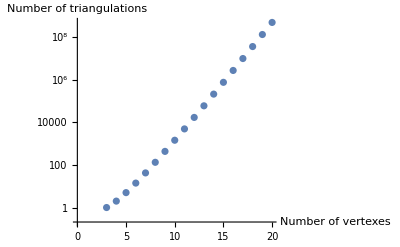

```mathematica
ListLogPlot[{#, totalNumberOfConvexPolygonTriangulations[#]}&/@Range[3,20], AxesLabel->{ "Number of vertexes", "Number of triangulations"}]
```

## Summary

In this Chapter, we took a fairly detailed look at polygons. We saw how their natural representation in the Wolfram Language is a simple List, and how that could be made to behave as a circular List by using modulo arithmetic.  We took a look at regular polygons, regular star polygons and monotone mountain polygons. Finally, we considered how to use a simple fan triangulation to calculate the area of a regular polygon, and a more complex triangulation to get the area of any simple polygon.

## Chapter 6: Random polygons

In this chapter we will develop functions to allow us to create random polygons. Such functions are interesting in their own right, but they also provide us with a useful source of random polygons that we can use to test our algorithms and in our demonstrations.

## Random polygons

In order to make the examples more interesting, we like to have functions to generate random sets of things. To create a simple function to generate random polygons, we can generalize our existing randomTriangle[...] function. There is still a collinearity problem, but now it is between triples of consecutive polygon vertexes. For a polygon P with n vertexes we have to check that all triples of consecutive vertexes v_(i-1), v_i, v_(i+1) (where 1 < i < n) are not collinear. Here are a couple of examples of invalid polygons so you can see what we mean:

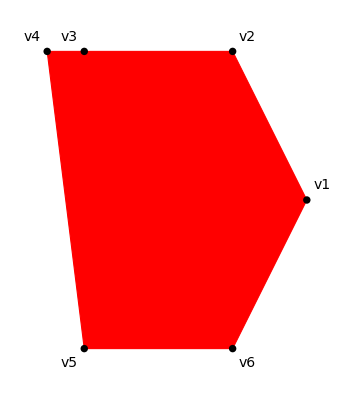
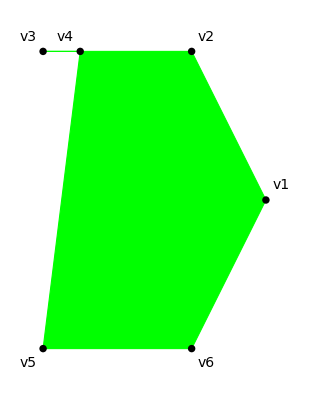
invalidPoly1 | invalidPoly2
-Graphics- | -Graphics-

```mathematica
invalidPoly1 ={{4,0}, {2,4}, {-2,4}, {-3, 4}, {-2,-4}, {2,-4}};
invalidPoly2 ={{4,0}, {2,4}, {-2,4}, {-1, 4}, {-2,-4}, {2,-4}};

Grid[{
{"invalidPoly1","invalidPoly2"},
{
Show[plotPoly[invalidPoly1, Red], Graphics[Disk[#, 0.1] &/@ invalidPoly1]], Show[plotPoly[invalidPoly2, Green], Graphics[Disk[#, 0.1] &/@ invalidPoly2]]
}
},Frame->All]
```

In both invalidPoly1 and invalidPoly2 vertexes v_2, v_3, v_4 are collinear, but in different ways. However, in both cases, note that the area of the triangle formed by v_2, v_3, v_4 is zero. We can therefore fix this in the same way we fixed the randomTriangle function: recurse the function until all triangles made up of three consecutive polygon vertexes have non-zero area. The function validPolyQ[...] returns True if all of such triangles have non-zero area:

```mathematica
validPolyQ[poly_] :=
And @@ (triangleArea[polyTake3[poly, #]] != 0 &/@ indexes[poly])
```

Here is a simple test program:

```mathematica
gridFormValue[{
validPolyQ[ square],
validPolyQ[ convexHexagon],
validPolyQ[ concaveHexagon],
validPolyQ[ invalidPoly1],
validPolyQ[ invalidPoly2]
}]
```

validPolyQ[square] | True
validPolyQ[convexHexagon] | True
validPolyQ[concaveHexagon] | True
validPolyQ[invalidPoly1] | False
validPolyQ[invalidPoly2] | False

We can use this to write randomPoly[...]:

```mathematica
randomPoly[n_, range_:Range[-5,5]] := Module[ {poly = RandomSample[Permutations[range, {2}], n]}, If[validPolyQ[poly],poly,randomPoly[n]]]
```

Let’s try it out:

```mathematica
testRandomPoly[] := Manipulate[
Module[{poly},
poly = randomPoly[n];
Graphics[ 
{
Yellow, Polygon[poly],
Red, Arrow[ polyEdges[ poly ] ],
Black,
polyVertexLabels[poly, {0.3,0.3}]
},
standardPlotStyle]
],
{{n, 3, "n"}, 3,8, 1},
FrameLabel -> "Functions randomPoly, polyEdges"
]

testRandomPoly[]
```

-Graphics-

You can see that the polygons are valid (no three collinear points), but that they are not necessarily simple. In fact, there are usually some intersecting edges. We will look at generating random simple polygons next.

## Random simple star shaped polygons

Our randomPoly[...] function does not constrain the polygon to be simple - it often generates non-simple polygons that have intersecting edges. A function to generate random simple polygons must ensure that there are no intersecting edges - a simple polygonization of the set of points. A random simple polygon that visits each of a set of points is an example of a spanning cycle, Hamiltonian polygon and planar traveling salesman tour.

Here is a straightforward algorithm for generating random simple polygons:

Generate a random polygon P (that may or may not have intersecting edges) with vertexes v_1 to v_n

Choose an origin point, p_origin, somewhere inside the polygon

Sort the polygon vertexes  anti-clockwise around p_origin

If there are any triples of collinear consecutive points go to the beginning else return the random simple star shaped polygon

Because each vertex in the sorted list is further anticlockwise than the previous one relative to p_origin, there can be no intersecting edges. However, this simple algorithm can’t generate all possible random polygons - because it is based on sorting the vertexes relative to a point, it can only generate star shaped polygons.

Star shaped polygon: a polygon P for which there exists a point o such that for each vertex v of P, the line segment ov lies within P.

The whole boundary of a star shaped polygon P is visible from o and the set of points from which all of the boundary is visible is called the kernel of P.

Note: It is essential to distinguish clearly between the star polygons that we discussed above and star shaped polygons that we discuss here! The two terms have very different meanings.

A key step in the algorithm is choosing an origin. Let’s consider that in more detail.

### Choose an origin point, p_origin, somewhere inside the polygon

Choice of origin warrants a certain amount of discussion. An obvious choice for the origin is to simply take the mean of the polygon vertexes, and this works very well.  The only disadvantage of using the mean is that even if all the vertexes are expressed in integers, their mean is very likely to generate a point which is a pair of floating point numbers.

There is an alternative origin that is very widely used: the rightmost lowest vertex of the polygon. Rightmost lowest means:

If there is only one rightmost vertex, then this is by default the rightmost lowest.

If there are two or more rightmost vertexes, then the lowest one of these is the rightmost lowest .

Provided all the polygon vertex points are given in integers, using the rightmost lowest vertex as the origin will preserve the use of integer arithmetic.

With modern languages and microprocessors there is nowadays little reason to prefer integer arithmetic to floating point. In some cases integer arithmetic might be slightly faster, but this is by no means always the case! For example, in the Wolfram Language, floating point arithmetic can be up to 100 times faster than integer arithmetic. This is because the Wolfram Language will always try to give exact answers (e.g.√3) rather than approximate answers (e.g. 1.73205), and it has to use relatively slow, symbolic manipulations to do so. Another example where floating point arithmetic will be faster is if your target platform can utilize a graphics card for processing coordinates. The moral here is to understand the characteristics of your target platform rather than just assume integers are always faster.

We can find the rightmost lowest point  using the following algorithm

Find the lowest y coordinate

Select all vertexes that have this value for y

Sort these vertexes by decreasing x

Return the first element of the sorted set

This translates directly into the Wolfram Language:

```mathematica
(* Find the rightmost lowest index *)
rightmostLowestIndex[ poly_?pointListQ ] := Module[{rightmostX, rightmostIndexes, indexes = indexes[poly]},
(* Find the x coordinate that is rightmost *)
rightmostX = First[ Sort[ poly, #1[[x]] > #2[[x]]&] ][[x]];
(* Select all of the indexes that have the rightmost x coordinate *)
rightmostIndexes = Select[indexes,poly[[#,x]] ==rightmostX &];
(* Sort by y to find the lowest vertex that has rightmost x *)
First[Sort[ rightmostIndexes, poly[[#1,y]] < poly[[#2,y]] &]] 
]

(* Find the rightmost lowest vertex *)
rightmostLowestVertex[ poly_?pointListQ ] := poly[[ rightmostLowestIndex[ poly ] ]]
```

The program below illustrates both possible origins - the mean and the rightmost lowest. The blue disk is the mean, and the red circle is the rightmost lowest vertex:

```mathematica
testOrigins[] :=Manipulate[
Graphics[
{
Green, Arrow/@ polyEdges[poly],
Blue, Disk[Mean[poly], 0.1],
Red, Circle[rightmostLowestVertex[poly], 0.5]
},
standardPlotStyle], 
{{poly, {{-2,3}, {-2,-1}, {2,-1},{-4,3}, {-2,-2}, {3,-1} }},{-5, -5}, {5,5}, 1, Locator}, 
FrameLabel -> Style["Test origins", 14]
]

testOrigins[]
```

-Graphics-

### Sort the polygon vertexes anti-clockwise around p_origin (using trig functions - slow)

Given p_origin, an obvious (but slow) way to sort points anti-clockwise is to sort the vertexes by the polar angles of the vectors (v_i - p_origin). The Wolfram Language provides built-in coordinate conversion functions, so for a point:

```mathematica
polarAngle[ pt_?pointQ ] :=CoordinateTransform[ "Cartesian" -> "Polar",pt][[2]]

polarRadius[ pt_?pointQ ] :=CoordinateTransform[ "Cartesian" -> "Polar",pt][[1]]
```

Now we can write sortByThetaTrig (using the mean of the polygon as p_origin):

```mathematica
sortByThetaTrig[ poly_?pointListQ ] := Module[{origin = Mean[poly]},
Sort[ poly,polarAngle[ #1 - origin] < polarAngle[ #2 - origin]&]]
```

We will see in the next section that the trig function is by far the most computationally expensive part of the calculation.

### Sort the polygon vertexes anti-clockwise around p_origin (not using trig functions - fast)

It is possible to dispense with the computationally expensive trig functions if we realize that we are not concerned with the actual value of the theta angle, only whether one vertex is further clockwise than another. The algorithm below from [ORourke1] first deals with some obvious cases, and then uses the property that if vector p_i has a smaller polar angle than vector p_j the cross product of the two vectors is > 0.

```mathematica
cross2D[ p1_?pointQ,p2_?pointQ ] := p1[[x]]*p2[[y]]-p1[[y]]*p2[[x]]

polarLessThan[ origin_?pointQ,v1_?pointQ, v2_?pointQ ]:=Module[{p1 = v1 - origin, p2 = v2 - origin},
Which[
(* angle of p1 is 0,thus p2 > p1*)
(p1[[y]] == 0) && (p1[[x]] > 0), True,
(* angle of p2 is 0,thus p1 > p2 *)
(p2[[y]] == 0) && (p2[[x]] > 0), False,
(* p1 is between 0 and 180, p2 between 180 and 360 *)
(p1[[y]] > 0) && (p2[[y]] < 0), True,
(* p1 is between 180 and 360, p2 between 0 and 180 *)
(p1[[y]] < 0) && (p2[[y]] > 0), False,
(* True if p1 is clockwise from p2 *)
cross2D[p1, p2] > 0, True
]
]
```

Here are two sorting functions. The first sorts about the mean and the second about the rightmost lowest vertex:

```mathematica
sortByTheta[ poly_?pointListQ ] := Module[{origin = Mean[poly]},
Sort[ poly,!polarLessThan[origin, #2, #1]&]
]

sortByThetaRL[ poly_?pointListQ ] := Module[{originIndex = rightmostLowestIndex[poly],
origin,
sortablePoly
},
origin = poly[[rightmostLowestIndex[poly]]];
(* We musn't include the origin point in the sort *)
sortablePoly = Delete[poly, originIndex];
(* Sort done! Put the origin back *)
Join[ {origin},Sort[ sortablePoly,!polarLessThan[origin, #2, #1]&]]
]
```

As you can see from the program below, both of these sorting functions are much faster than sortByThetaTrig[...]. So much so, that we have had to use a log plot.

```mathematica
Manipulate[
Module[ {p},
p = Table[ randomPoly[i],{i, 3,numberOfSides} ];
plotType[{
If[ sbt,First[ AbsoluteTiming[ sortByTheta[ # ] ] ]  &/@ p],
If[ sbtrl,First[ AbsoluteTiming[ sortByThetaRL[ # ] ] ] &/@ p],
If[ sbtt,First[ AbsoluteTiming[ sortByThetaTrig[ # ] ] ] &/@ p] 
}, Joined -> True, PlotLegends -> {"sortByTheta", "sortByThetaRL", "sortByThetaTrig" }, 
AxesLabel->{"number of points", "Log seconds"},
PlotMarkers -> Automatic, PlotRangeClipping -> False
]
],
{{plotType, ListLogPlot, "plot type"}, {ListPlot, ListLogPlot}},
{{sbt, True, "sortByTheta"}, {True, False}},
{{sbtrl, True, "sortByThetaRL"}, {True, False}},
{{sbtt, True, "sortByThetaTrig"}, {True, False}},
{{numberOfSides, 5, "radom polygon max number of sides"}, 5,15, 1, SetterBar}, 
ContinuousAction->False
 ]
```

-Graphics-

We can compare the polygons produced by sortByTheta[...] and sortByThetaRL[...] in the program below. You can see that both sorting approaches remove intersecting edges, but, because the two functions sort around different origins, they often generate different star shaped polygons. The origin for sortByTheta[...] is the mean of the polygon vertexes, and this tends to give a very neatly ordered polygon because the vertexes tend to be distributed quite evenly around it. The origin for sortByThetaRL[...], is the rightmost lowest polygon vertex. Because the vertexes will be to the left of it, this tends to give polygons that have more and larger concavities. If you show the unsorted polygon, you can play around with the points to create simple polygons that are not star shaped polygons. These are inaccessible by our simple algorithm.

```mathematica
testSortByTheta[] := Manipulate[
Graphics[
{
If[unsorted, {Opacity[0.1], Polygon[p]}],
If[validPolyQ[p],Green,Red], Arrow/@ polyEdges[sortType[p]],
Blue, Disk[Mean[p], 0.1],
Purple, Circle[rightmostLowestVertex[p], 0.5],
Black, polyVertexLabels[p, {0.3,0.3}]
},
standardPlotStyle
], 
Style["Green if validPolyQ == True", Green, 12],
Style["Red if validPolyQ == False", Red, 12],
{{p, {{-2,3},{-2,-1},{2,-1},{-4,3},{-2,-5}, {5,-1}  }},{-5, -5}, {5,5}, 1, Locator}, 
{{unsorted, False, "show unsorted poly"}, {True, False}},
{{sortType,sortByTheta, "sort type"}, {sortByTheta, sortByThetaRL }},
FrameLabel -> Style["Test function sortByTheta", 14]
]

testSortByTheta[]
```

-Graphics-

From now on, we will use sortByTheta[...] because most of the time, it gives the most pleasing result.

## The randomStarShapedPoly[...] function

Now that we have the tools we need, this function is very simple:

```mathematica
randomSimpleStarShapedPoly[ n_Integer, range_:Range[-5,5] ] := Module[ {
poly = RandomSample[Permutations[range, {2}], n],
sortedPoly }, 
sortedPoly = sortByTheta[poly];
(* check for collinear vertex triples *)
If[validPolyQ[sortedPoly],sortedPoly,randomSimpleStarShapedPoly[n]]
]
```

Here is a demo program that provides a good test bed for our randomPoly[...], randomSimpleStarShapedPoly[...] and polyEdges[...] functions:

```mathematica
testRandomPoly[] := Manipulate[
Module[{p},
p =If[ simple, randomSimpleStarShapedPoly[numberOfVertexes],randomPoly[numberOfVertexes]];
Graphics[ 
{
Yellow, Polygon[p],
Red, Arrow/@polyEdges[p],
Blue, 
polyVertexLabels[p],
Disk[Mean[p], 0.1]
},
standardPlotStyle]
],
{{numberOfVertexes, 5, "number of vertexes"}, 3,30, 1},
{{simple, False, "simple"}, {True, False}},
FrameLabel -> "Functions randomPoly, randomSimpleStarShapedPoly and polyEdges"
]

testRandomPoly[]
```

-Graphics-

## Summary

This chapter was all about creating polygons for use in our algorithms and demonstrations. First of all, we presented a very simple algorithm for creating random polygons in general position. As a variant on the random polygon, we also provided an algorithm to make simple star shaped polygons and to convert any point list into a simple star shaped polygon by sorting the points anticlockwise relative either to the mean or the rightmost lowest point.

## Chapter 7: Intersections

Up to now, we have been able to work without considering the intersections of the various geometrical objects in any great detail. In this chapter we consider how line segments intersect with line segments, how lines intersect with lines and how polygons intersect with line segments and themselves. Note that these intersection functions will only work with convex polygons, so we will begin by considering polygon convexity.

## Testing for polygon convexity

As we walk around the perimeter of a convex polygon, at each vertex we must either always turn in the same direction (always clockwise or always anticlockwise) or go straight. If we ever turn in a different direction, then we have a concavity. Given this, the function to determine polygon convexity is very simple:

```mathematica
convexPolyQ[ poly_?pointListQ ] := SameQ @@ (leftOnQ @@ polyTake3[ poly, #] &/@ indexes[poly] + 2)
```

This function works independently of which way we take the polygon vertexes - anticlockwise (standard) or clockwise (non-standard). For example:

```mathematica
gridFormValue[{
convexPolyQ[convexHexagon],
convexPolyQ[ Reverse[convexHexagon] ],
convexPolyQ[ concaveHexagon ],
convexPolyQ[ Reverse[concaveHexagon] ]
}]
```

convexPolyQ[convexHexagon] | True
convexPolyQ[Reverse[convexHexagon]] | True
convexPolyQ[concaveHexagon] | False
convexPolyQ[Reverse[concaveHexagon]] | False

## Point inside convex polygon

This is possibly the simplest relationship - whether a point is inside a convex polygon or not. However, there are actually two cases depending on how we treat polygon edges. Here are a couple of definitions:

Point strictly inside convex polygon: the point is inside the polygon but not on its boundary. In this case leftQ is True for the point and every polygon edge.

Point inside convex polygon: the point is inside the polygon or on its boundary. In this case leftOnQ  is True for the point and every polygon edge.

The functions themselves are pretty trivial:

```mathematica
insideConvexQ[ p_?pointListQ, pt_?pointQ ] := And @@ (Flatten[leftQ[#[[1]], #[[2]], pt] &/@ polyEdges[p]])

insideOnConvexQ[ p_?pointListQ, pt_?pointQ ] := And @@ (Flatten[leftOnQ[#[[1]], #[[2]], pt] &/@ polyEdges[p]])
```

We have used “inside” and “insideOn” rather than “strictly” in the function names, because “inside” and “insideOn” are more explicit, and fit better with our existing terminology.

The inverse of insideConvexQ[...] is outsideConvexQ[...]. Note that there can be no outsideOnConvexQ[...] function because any points on the polygon boundary are, by definition, part of the polygon:

```mathematica
outsideConvexQ[ p_?pointListQ, pt_?pointQ ] := !insideOnConvexQ[p, pt]
```

Here is a demo function. As usual, Green indicates that a condition is true, and Red indicates that it is false:

```mathematica
testPointInConvexPolygonFunctions[] := Manipulate[
Module[ {poly},
Graphics[ {
Blue,Arrow/@ polyEdges[poly = {v1,v2,v3,v4,v5,v6}],
If[insideConvexQ[poly,a], Green, Red],Text[Style["insideConvexQ",14], a - {0,0.5}],
If[insideOnConvexQ[poly,a], Green, Red],Text[Style["insideOnConvexQ",14], a - {0,1}],
If[outsideConvexQ[poly,a], Green, Red],Text[Style["outsideConvexQ",14], a - {0,1.5}],

Black,
Text[ "leftQ applied to poly edges = " <>ToString[leftQ[#[[1]], #[[2]], a] &/@ polyEdges[poly]], {0,-5}],

Text[ "leftOnQ applied to poly edges = " <>ToString[leftOnQ[#[[1]], #[[2]], a] &/@ polyEdges[poly]], {0,-5.5}],

Black, polyVertexLabels[poly, {0.3,0.3}],
Black,pointLabels[{a}, {"a"}],
If[ convexPolyQ[ poly ],Blue, Red],Opacity[0.1],Polygon[poly]
},
standardPlotStyle]
],
{{a,{4,4}},{-5, -5}, {5,5}, 1, Locator}, 

{{v1, {3,1}},{-5, -5}, {5,5}, 1, Locator}, 
{{v2, {1,4}},{-5,-5}, {5,5}, 1, Locator}, 
{{v3, {-4,3}},{-5,-5}, {5,5}, 1, Locator}, 
{{v4, {-3,-2}},{-5, -5}, {5,5}, 1, Locator}, 
{{v5, {0,-4}},{-5,-5}, {5,5}, 1, Locator}, 
{{v6, {4,-3}},{-5,-5}, {5,5}, 1, Locator},
"insideConvexQ and insideOnConvexQ only work for convex polygons!",
FrameLabel -> "Test function convexPolyQ, insideConvexQ and insideOnConvexQ"
]

testPointInConvexPolygonFunctions[]
```

-Graphics-

## Intersection of line segments with line segments and polygons

A key set of basic algorithms in computational geometry are those concerning the intersection of lines. There are several types of intersection we will consider:

Proper intersection of line segments

Improper intersection of line segments

Intersection of line segments (which is a combination of 1 and 2)

Polygon intersection with line segments

Polygon self- intersection

We will develop algorithms for all of these over the next few sections. As we will be doing a lot of work with these different intersection functions, here is a generalized test/demo program that takes an intersection function as an argument:

```mathematica
testIntersectionFunction[ fnQ_, description_: "" ] := Manipulate[Module[{ret},
(* Call the intersection function *)
ret = fnQ[a,b,c,d];
Graphics[{
Blue, Arrow[ {a, b}], 
Black, Arrow[ {c, d}], 
If[ret, Green, Red],
Text[Style[ToString[fnQ]<>"[a,b,c,d] = "<>ToString[ret], 16], {0,5}],
Black,pointLabels[{a,b,c,d}, {"a", "b", "c", "d" }]
},
standardPlotStyle
]], 
{{a,{4,4}},{-5, -5}, {5,5}, 1, Locator}, 
{{b,{-4,-4}},{-5,-5}, {5,5}, 1, Locator},
{{c,{-4,4}},{-5,-5}, {5,5}, 1, Locator},
{{d,{4,-4}},{-5,-5}, {5,5}, 1, Locator},
description, 
FrameLabel -> Row[{"Test function " , fnQ}]
]
```

## Proper intersection of line segments

Here is a definition:

Proper intersection: the line segment a b splits the line segment c d and the line segment c d splits the line segment a b. No three points are collinear (i.e. the lines must cross).

Given the relationship functions from earlier, we can write a function to test for proper intersection of a b and c d:

```mathematica
properIntersectQ[ a_, b_, c_, d_] := If[ collinearQ[a,b,c] ||collinearQ[a,b,d] ||collinearQ[c,d,a] || collinearQ[c,d,b], 
False, 
Xor[ leftQ[a,b,c], leftQ[a,b,d]] && Xor[leftQ[c,d,a], leftQ[c,d,b]]
]
```

This function is very straightforward: having checked that no three points are collinear, we just have to check that c or d is to the left of a b and a or b is the the left of c d. Here is a test program:

```mathematica
properIntersectQTest = testIntersectionFunction[ properIntersectQ, "No 3 points are collinear AND a b splits c d AND c d splits a b"]
```

-Graphics-

## Improper intersection of line segments

This is a more constrained form of intersection, because we require the end point of one of the line segments to be somewhere on the other one:

Improper intersection: when the endpoint of one line segment lies anywhere on the other line segment.

We have improper intersection of line segments a b and c d when:

c is between a and b OR d is between a and b

a is between c and d OR b is between c and d

Here is the code:

```mathematica
improperIntersectQ[ a_, b_, c_, d_] := 
  betweenQ[a,b,c] ||
betweenQ[a,b,d] ||
betweenQ[c,d,a] ||
betweenQ[c,d,b]
```

And here is a test:

```mathematica
improperIntersectQTest = testIntersectionFunction[ improperIntersectQ, "The end point of one line segment lies anywhere on the other line segment" ]
```

-Graphics-

## Intersection of line segments

This is the least constrained type of intersection because it is just a combination of proper or improper intersection:

Intersection: either a proper or improper intersection.

The code is trivial:

```mathematica
intersectQ[ a_, b_, c_, d_] :=
properIntersectQ[a, b, c, d ] || improperIntersectQ[a,b,c,d]
```

And here is the test program:

```mathematica
intersectQTest =testIntersectionFunction[ intersectQ, "proper or improper intersection" ]
```

-Graphics-

## Polygon intersection with line segments

When working with polygons, we often want to know if a line segment, a b, intersects an edge, v_i v_j of a polygon. The rule is that the line segment can go through the edge (proper intersection) or terminate  on the edge (improper intersection), but must not terminate on a polygon vertex. This requires a new type of intersection function that has the same semantics as intersect, but with the added constraint that no two line segment end points can be coincident:

```mathematica
intersectEdgeQ[v1_, v2_, a_, b_] := (v1 ≠ a ) && (v2 ≠ a) && ( v1 ≠ b) && (v2 ≠ b) && intersectQ[v1, v2, a, b]
```

Here is the test program. You can see that the function works just like intersect, except that line end points are now excluded:

```mathematica
intersectEdgeQTest = testIntersectionFunction[ intersectEdgeQ, "Intersects (proper) a polygon edge, but does not terminate at a vertex." ]
```

-Graphics-

To test if a line segment intersects with a polygon is a simple matter of applying intersectEdgeQ[...] to the line segment and each of the polygon edges:

```mathematica
intersectPolyQ[ poly_, a_, b_] := Apply[Or, intersectEdgeQ[ #[[1]], #[[2]], a, b] &/@ polyEdges[poly]]
```

Here is a test program:

```mathematica
testIntersectPolygonQ[] := Manipulate[
Module[ {poly},
Graphics[ 
{Blue,Arrow/@ polyEdges[poly = {v1,v2,v3,v4,v5,v6}],
If[ intersectPolyQ[poly, a,b], Green, Red],Arrow[{a,b}],
Text[Style[intersectPolyQ[poly, a,b], 16]],
Black, polyVertexLabels[poly, {0.3,0.3}],
Black,pointLabels[{a,b}, {"a", "b"}],
Blue,Opacity[0.2],Polygon[poly]
},
standardPlotStyle]
],
{{a,{4,4}},{-5, -5}, {5,5}, 1, Locator}, 
{{b,{-4,-4}},{-5,-5}, {5,5}, 1, Locator},  
{{v1, {4,1}},{-5, -5}, {5,5}, 1, Locator}, 
{{v2, {1,4}},{-5,-5}, {5,5}, 1, Locator}, 
{{v3, {-4,3}},{-5,-5}, {5,5}, 1, Locator}, 
{{v4, {-3,-2}},{-5, -5}, {5,5}, 1, Locator}, 
{{v5, {0,-4}},{-5,-5}, {5,5}, 1, Locator}, 
{{v6, {4,-3}},{-5,-5}, {5,5}, 1, Locator},
"Line segment intersects a polygon edge, but does not terminate at a vertex.",
FrameLabel -> "Test function intersectPolyQ"
]

intersectPolygonQTest = testIntersectPolygonQ[]
```

-Graphics-

## Polygon self-intersection

Just to finish this section, we can write a convenience function that checks to see if a polygon self-intersects i.e. if a polygon edge intersects the polygon. This function takes a polygon and the index i of vertex, v_i , the edge being v_i v_(i+1)

```mathematica
intersectPolyEdgeQ[ poly_, i_] := intersectPolyQ[ poly, poly[[i]], poly[[polyNextIndex[Length[poly],i]]] ]
```

We can use this to provide a useful (if brute force) test for a simple polygon (no intersecting edges and no duplicate vertexes):

```mathematica
simplePolyQ[ poly_ ]:=(!Or@@(intersectPolyEdgeQ[ poly, #]&/@ indexes[poly])) &&(Length[poly] == Length[Union[poly]])
```

Here is a test program:

```mathematica
Manipulate[
Graphics[{
If[simplePolyQ[poly], Green, Red],
Polygon[poly],
Black,Text[Style[Row[{"simplePolyQ = ",simplePolyQ[poly] }], 14]],
}, standardPlotStyle],
"A simple polygon has no intersecting edges.",
{{poly,5 regularPoly[12]},{-5, -5}, {5,5}, 1, Locator}
]
```

-Graphics-

## Demonstration of line segment intersection types

For your convenience the following program combines the above demo programs to summarize the types of intersection we have considered:

```mathematica
TabView[{
"properIntersectQ" ->properIntersectQTest,
"improperIntersectQ" ->improperIntersectQTest ,
"intersectQ" ->intersectQTest ,
"intersectEdgeQ" ->intersectEdgeQTest,
"intersectPolyQ" ->intersectPolygonQTest
}, LabelStyle -> Small ]
```

-Graphics-

## Summary

Because the intersection algorithms we present here only work with convex polygons, we began the chapter with a consideration of testing for polygon convexity. We then investigated testing if a point is inside a polygon or not. After that investigated the various types of intersections between lines and/or polygons.

## Chapter 8: Polygon extreme points, tangents, monotonicity and splitting

In this chapter we will look at polygon extreme points, polygon monotonicity, tangents to a convex polygon from a point, and how to split a convex polygon across tangent vertexes.

## Polygon extreme points

Here is a definition:

Extreme points of a polygon with respect to a direction vector: The extreme points of a polygon with respect to a particular direction vector d⃗, are those vertexes that when projected onto that direction are the shortest and longest distances along it.

For example, the extreme points of a polygon in the X direction are those vertexes that have minimum and maximum x coordinates. If we take the extreme points in all directions, this set of points is the convex hull of the polygon. We will say more about convex hulls, and give other definitions for them, shortly.

Vectors only have a magnitude and a direction - they have no position in Cartesian space. Because of this, we can place a vector anywhere we like. For a direction vector, one end is generally located at the origin, and the other end specifies the length (magnitude) and direction relative to the origin. We can therefore specify a direction vector using a single point (the origin being assumed). Even though we can specify a vector by a single point if we assume the origin, vectors and points remain two very different things and should not be confused!

If we have two points, a and b, then the projection of the vector a - b onto direction d⃗ tells us which point is further along d⃗.  If we take the dot product,  d⃗·(a-b) and this is greater than 0, then the projection of a onto d⃗ is further along than the projection of b. We say that a is above b relative to d⃗.  Here is a demonstration that allows you to see the projections of a, b and a - b onto  direction d⃗.

```mathematica
Manipulate[Module[{p, pa, pb},
Graphics[{
(* For a change, calculate the projections useing the built-in Projection[...] function *)
p := Projection[a-b, d],
pa := Projection[a, d],
pb := Projection[b, d],

(* Draw the direction d⃗ *)
InfiniteLine[{{0,0}, d}],
Green,
Arrow[{{0,0}, d}],

(* Draw the projections pa and pb *)
Black,Dashed,
Line[{pa,a}],
Line[{pb,b}],

(* Label the points *)
pointLabels[{a,b,a-b, d, p}, {"a", "b", "a - b", "d⃗", "p"}],

(* Draw the projection p and a - b *)
If[Dot[d, a-b] > 0,Red, Blue],
Line[{p, a-b}],
Disk[p, 0.2],
Disk[a-b, 0.2],

(* Print the dot product *)
Text[Style["TraditionalForm`= "+Dot[d, a-b],12], {0,6}]
}, standardPlotStyle]],
"The projections of points a, b and a-b on direction d⃗.",
{{a, {1,1}}, Locator},
{{b, {-4,0}}, Locator},
{{d, {-3,4}}, Locator}
]
```

-Graphics-

Now we can write a comparison function to see which point is further along a direction:

```mathematica
aboveQ[ a_, b_, d_] := If[Dot[d, a-b] > 0, True, False ]
```

We can use this comparison function to sort polygon (or polygonal chain) vertexes with respect to a vector or line. The first version of the function  assumes that v is a vector represented as a single point with the origin assumed as the other point:

```mathematica
sortPolyIndexesWrtVector[ poly_List, v_?pointQ ] := Sort[ 
indexes[poly], 
aboveQ[ poly[[#1]], poly[[#2]], v]& 
]
```

The second version of the function assumes that the vector is represented as a line segment:

```mathematica
sortPolyIndexesWrtLine[ poly_List, l_?lineSegmentQ ] := sortPolyIndexesWrtVector[ poly, l[[2]] - l[[1]] ]
```

Once we have sorted the polygon indexes using their values (the vertexes), then the indexes of the extreme points are just the first and last elements in the sorted List:

```mathematica
extremePolyIndexesWrtVector[ poly_List, v_?pointQ ] := Module[{ps},
ps = sortPolyIndexesWrtVector[poly, v];
{First[ps], Last[ps]}
]

extremePolyVertexesWrtVector[ poly_List, v_?pointQ ] := Module[{indexes},
indexes = extremePolyIndexesWrtVector[ poly, v ];
{ poly[[ indexes[[1]] ]], poly[[ indexes[[2]] ]] }
]
```

Here is the first test program:

```mathematica
plotExtremePolyVertices[ ] := 
Manipulate[
Module[
{extremes, poly, l},
poly = {v1, v2, v3, v4, v5, v6, v7, v8, v9, v10}; 
l = {l1, l2};
(* The absolute position of the Line doesn't matter - it is used as a vector *)
extremes = extremePolyVertexesWrtVector[ poly, l2 - l1];
Graphics[{
{Blue, Opacity[0.1],Polygon[poly ]},
Green,Arrow[{l1, l2}],
Black,pointLabels[{l1, l2}, {"l1", "l2"}],
{Dashed, Blue,Line[{#, projectPoint[ #, l] }]&/@ Complement[poly, extremes]},{Dashed, Red,
Line[{extremes[[2]], projectPoint[extremes[[2]], l]}],
Line[{extremes[[1]], projectPoint[extremes[[1]], l] }]},
Circle[ extremes[[1]], 0.5],
Circle[ extremes[[2]], 0.5],
Black, polyVertexLabels[ poly ]
},
standardPlotStyle]
],
{{l1,{-4,4}},{-5, -5}, {5,5}, 1, Locator},
{{l2,{-4,-4}},{-5, -5}, {5,5}, 1, Locator},
{{v1,{3,2}},{-5,-5},{5,5},1,Locator},
{{v2,{1,3}},{-5,-5},{5,5},1,Locator},
{{v3,{-1,3}},{-5,-5},{5,5},1,Locator},
{{v4,{-3,2}},{-5,-5},{5,5},1,Locator},
{{v5,{-4,0}},{-5,-5},{5,5},1,Locator},
{{v6,{-3,-2}},{-5,-5},{5,5},1,Locator},
{{v7,{-1,-3}},{-5,-5},{5,5},1,Locator},
{{v8,{1,-3}},{-5,-5},{5,5},1,Locator},
{{v9,{3,-2}},{-5,-5},{5,5},1,Locator},
{{v10,{4,0}},{-5,-5},{5,5},1,Locator}
]

plotExtremePolyVertices[ ]
```

-Graphics-

If you play about with the example above, you can see that if, in any direction, there is more than one vertex that is extreme, the algorithm selects one of these depending on the direction of l_1 l_2. It does not necessarily select the extreme vertex closest to the line. This is generally acceptable for most uses of this algorithm. It would be very easy to modify it to return all equal extreme vertexes: starting at the First element of the sorted List, simply return all consecutive elements that are collinear with it. Do the same for the Last element.

If we want to find the extreme points in the direction perpendicular to d⃗, then we just have to use the transformation rules for rotating a point, a b, about the origin by multiples π :

Rotation | Rule
π/2 (90°) | (a, b) → (-b, a)
ℼ (180°) | (a, b) → (-a, -b)
3π/2 (270°) | (a, b) → (b, -a)

This gives us the following useful functions:

```mathematica
rotate90[ pt_?pointQ ] := { -pt[[2]], pt[[1]] }

rotate180[ pt_?pointQ] := { -pt[[1]], -pt[[2]] }

rotate270[ pt_?pointQ] := { pt[[2]], -pt[[1]] }
```

For example:

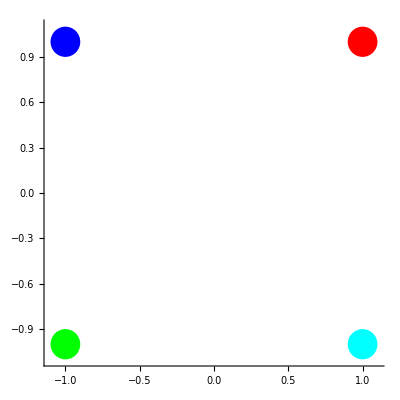

```mathematica
Block[{pt = {1,1}, r=0.1},
Graphics[{
Red,Disk [pt, r],
Blue,Disk[rotate90[pt], r],
Green,Disk[ rotate180[pt], r],
Cyan,Disk[rotate270[pt], r]
}, Axes->True]
]
```

## Monotone polygons

Here is a definition:

Monotone polygon: A polygon P is monotone with respect to the straight line L if every line orthogonal to L intersects P at most twice.

If we divide P into two polygonal chains C_1 and C_2 across its extreme vertexes with respect to L, then the polygon must be monotone with respect to L if both C_1 and C_2 are monotone with respect to L. We can write a function to split a polygon with l vertexes across two vertexes with indexes i1 and i2, into two polygonal chains as follows:

```mathematica
splitPolyIndexes[ l_Integer, i1_Integer, i2_Integer] := {polyIndexRange[ l, i1, i2],
polyIndexRange[ l, i2, i1]}
```

Now we can write monotonePolyQ[...] to test if a polygon is monotonic with respect to a line specified by a line segment:

```mathematica
monotonePolyQ[ poly_List, line_ ?lineSegmentQ] :=Module[{eis, up, down},
(* Find the extreme indexes *)
eis = extremePolyIndexesWrtVector[ poly, line[[2]] - line[[1]]];
(* Split the poly *)
{up, down} = splitPolyIndexes[Length[poly], eis[[1]], eis[[2]] ];
(* Test the chains *)
monotoneQ[vertexes[poly,up], line] && monotoneQ[vertexes[poly,down], line]
]
```

Here is a (rather large) test program. When the polygon is monotone, it is green, otherwise, it is red. The two extreme points are indicated by red dashed lines down to the straight line. Try moving the line end points and the polygon vertexes to get a feel for polygon monotonicity:

```mathematica
testMonotonicPolyQ[ ] := Manipulate[
Module[ {poly, line, evs, eis, up, down},
poly = {v1, v2, v3, v4, v5, v6, v7, v8, v9, v10}; 
line = {l1, l2};
(* The absolute position of the Line doesn't matter - it is used as a vector *)
evs = extremePolyVertexesWrtVector[ poly, l2 - l1];
eis = extremePolyIndexesWrtVector[ poly, l2 - l1];
{up, down} = splitPolyIndexes[Length[poly], eis[[1]], eis[[2]] ];

Graphics[{
(* Test the poly *)
If[monotonePolyQ[poly, line], Green, Red],
Text[ Style[ monotonePolyQ[poly, line], 14] ],

(* Draw the poly *)
{Opacity[0.1],Polygon[poly ]},
Black, polyVertexLabels[ poly ],

(* Draw the two pchains *)
If[monotoneQ[vertexes[poly,up], line], Green, Red], 
If[ chain1,Arrow[vertexes[poly,up]] ], 
If[monotoneQ[vertexes[poly,down], line], Green, Red],
If[ chain2,Arrow[vertexes[poly,down]] ], 

(* Draw the line *)
Blue,Arrow[{l1, l2}],
Black,pointLabels[{l1, l2}, {"l1", "l2"}],

(* Draw the projections of the chains *)
If[ chain1,{Dashed, Blue,Line[{#, projectPoint[ #, line] }]&/@ vertexes[poly,up]}],
If[ chain2,{Dashed, Blue,Line[{#, projectPoint[ #, line] }]&/@ vertexes[poly,down]}],

(* Draw the projections of the extreme vertexes *)
{Dashed, Red,
Line[{evs[[2]], projectPoint[evs[[2]], line]}],
Line[{evs[[1]], projectPoint[evs[[1]], line] }]},

(* Circle the extreme vertexes *)
Circle[ evs[[1]], 0.5],
Circle[ evs[[2]], 0.5]
},
standardPlotStyle]
],
{{chain1, True, "chain 1"}, {True, False}},
{{chain2, True, "chain 2"}, {True, False}},
{{l1,{-4,4}},{-5, -5}, {5,5}, Locator},
{{l2,{-4,-4}},{-5, -5}, {5,5}, Locator},
{{v1,{3,2}},{-5,-5},{5,5},Locator},
{{v2,{1,3}},{-5,-5},{5,5},Locator},
{{v3,{-1,3}},{-5,-5},{5,5},Locator},
{{v4,{-3,2}},{-5,-5},{5,5},Locator},
{{v5,{-4,0}},{-5,-5},{5,5},Locator},
{{v6,{-3,-2}},{-5,-5},{5,5},Locator},
{{v7,{-1,-3}},{-5,-5},{5,5},Locator},
{{v8,{1,-3}},{-5,-5},{5,5},Locator},
{{v9,{3,-2}},{-5,-5},{5,5},Locator},
{{v10,{4,0}},{-5,-5},{5,5},Locator}
]

testMonotonicPolyQ[ ]
```

-Graphics-

## Tangent to a convex polygon from a point

As we will soon see, it can be very useful to take a point outside a convex polygon, and find the tangent from that point to the polygon. Firstly, we need the definition of a tangent to a convex polygon:

Tangent to a convex polygon: a line L is tangential to a convex polygon P if L touches P without crossing its boundary.

In terms of intersections, L is a tangent to P if L is external to P and intersects P at a single vertex or along an edge. From any point p that is outside of the convex polygon P there are two line segments, t_i and t_k that are tangents to P at vertexes v_i, v_k . We refer to these as tangent vertexes from p to P. These tangent vertexes are the extreme points of the polygon relative to the lines of sight from p. This is an important observation! We can test to see if a vertex of P is a tangent vertex relative to p as follows:

```mathematica
polyTangentQ[ poly_, polyIndex_, pt_ ] :=Xor[
leftOnQ[ polyPrevVertex[poly, polyIndex],polyVertex[poly, polyIndex],pt ],
leftOnQ[ polyVertex[poly, polyIndex],polyNextVertex[poly, polyIndex],pt ]
]
```

We can find both tangent vertexes from p to P:

```mathematica
polyTangentIndexes[ poly_, pt_ ] := Select[ indexes[poly], polyTangentQ[ poly, #, pt]&, 2]

polyTangentVertexes[ poly_, pt_ ] := Module[
{indexes = polyTangentIndexes[poly, pt]},
{poly[[ indexes[[1]] ]], poly[[ indexes[[2]] ]]}
]
```

Here is a test program. It uses an idiom we call ptPoly where we define a List of Locators, and then take the first element of the List as a point and the rest of the List as a polygon. This gets around the Wolfram Language limitation that specifies that in Manipulate you can have either a single List of Locators or individual Locators, but not both:

```mathematica
testPolyTangents[] := Manipulate[
Module[ {pt, poly, tv, ti},
(* We use the first element in ptPoly as the point *)
pt = N[First[ptPoly]];
(* We use the rest of the elements as the polygon *)
poly= N[Rest[ptPoly]];
tv = polyTangentVertexes[ poly, pt];
ti = polyTangentIndexes[ poly, pt];
Graphics[ {
(* Draw the poly *)
{Opacity[0.1],If[ convexPolyQ[ poly ],Blue, Red], Polygon[poly]},
Black, polyVertexLabels[poly],

(* Draw the tangent vertexes *)
If[ Length[tv] == 2, 
{Green, Circle[#, 0.5] &/@ tv,
Line[{tv[[1]], pt}],
Line[{tv[[2]], pt}]}
],

(* Draw the tangent indexes*)
Text[Style[Row[{"tangent indexes = ",ti}], 12], {0,5.5}]
},
standardPlotStyle,
FrameLabel -> "Tangents between point and polygon"]
],
{{ptPoly, regularPoly[10,4] },{-5, -5}, {5,5}, 1,Locator}
]

testPolyTangents[]
```

-Graphics-

Of course, you will get an error condition if you put the external point inside the polygon.

## Splitting a convex polygon into polygonal chains

Having found the tangent vertexes  v_i v_k, we can split the convex polygon across these vertexes into two polygonal chains. One of these chains, C_c will be convex with respect to the triangle p v_i v_k and the other C_r will either comprise v_i v_k only, or be concave (reflex) with respect to the triangle. Splitting the convex polygon is a particularly useful thing to do because if we take the convex chain C_c then, {p} ∪ C_c is the convex hull of {p} ∪ P. This suggests a simple way of calculating convex hulls by incrementally adding external points to a starting convex polygon. Also, if we take the reflex chain, C_r and create triangles by adding p to each of its edges, we have triangulated p v_i v_k. This suggests an incremental triangulation algorithm where once again, we add external points to a convex polygon and triangulate.

```mathematica
splitPolyIndexesOnTangents[ poly_, pt_ ] := Module[{ti1, ti2, c1, c2},
{ti1, ti2} = polyTangentIndexes[ poly, pt];
{c1, c2} =splitPolyIndexes[ Length[poly], ti1, ti2 ];
(* Find the reflex chain and put it SECOND in the output List *)
If [ (Complement[c1, {ti1, ti2}] == {}) || sameSideOnQ[poly[[ ti1 ]],poly[[ ti2 ]], {pt,poly[[ c1[[2]] ]] }],
{c2, c1},
{c1, c2}
]
]

splitPolyOnTangents[ poly_, pt_ ] :=Module[ {c1, c2},
{c1, c2} = splitPolyIndexesOnTangents[poly, pt];
{vertexes[ poly, c1], vertexes[poly, c2]}
]
```

We can now write a function that returns the convex hull of the polygon plus the point:

```mathematica
convexHullPolyPoint[ poly_?pointListQ , pt_?pointQ ] :=Module[{c1, c2}, 
{c1, c2} = splitPolyOnTangents[ poly, pt ];
Join[ c1, {pt}]
]
```

Similarly, we can easily create a triangulation of the point plus the reflex chain just by appending the point to the chain edges:

```mathematica
triangulateChain[ pchain_, pt_ ] := Join[{pt}, #]&/@pchainEdges[ pchain ]
```

Here is a test program. You can see that as you drag the point around the area outside the convex polygon, the two chains are always clearly identified. It uses our ptPoly idiom for Locators:

```mathematica
testSplitPolyOnTangents[] :=Manipulate[
Module[{pt, poly, ti, tv, hull, cc, cr, trs},
(* We split the ptPoly List of Locators so that the First is the point 
and the Rest is the poly *)
pt = N[First[ptPoly]];
poly= N[Rest[ptPoly]];

ti = polyTangentIndexes[ poly, pt];
tv = polyTangentVertexes[ poly, pt];

hull = convexHullPolyPoint[poly, pt];

{cc, cr} =splitPolyIndexesOnTangents[ poly, pt];

trs = triangulateChain[vertexes[poly, cr], pt];

Graphics[{

(* Draw the poly *)
{Opacity[0.1],If[ convexPolyQ[ poly ],Blue, Red], Polygon[poly]},
Black, polyVertexLabels[poly],

(* Draw the tangents *)
If[ Length[tv] == 2, 
{Green, Circle[#, 0.5] &/@ tv,
Line[{tv[[1]], pt}],
Line[{tv[[2]], pt}]}
],

(* Draw the tangent indexes*)
Text[Style[Row[{"tangent indexes = ",ti}], 12], {0,5.5}],

(* Draw the chains and the hull *)
If[ convexChain, {Red, Arrow[ vertexes[poly,cc] ]} ],
If[ reflexChain, {Blue, Arrow[ vertexes[poly,cr] ]} ],
If[ convexHull, {Orange,Arrow[polyEdges[hull]], Opacity[0.1],Polygon[ hull ]} ],

(* Draw the two triangulations *)
If[ polyTriangles,drawColouredPolys[ fanTriangulatePoly[poly] ]],
If[ pointTriangles,drawColouredPolys[ trs, "BrightBands"]]

},
standardPlotStyle,
FrameLabel -> "Splitting a convex polygon"]
],
{{pointTriangles, False, "point triangles"}, {True, False}},
{{polyTriangles, False, "poly triangles"}, {True, False}},
{{convexChain, False, "convex chain"}, {True, False}},
{{reflexChain, False, "reflex chain"}, {True, False}},
{{convexHull, False, "convex hull"}, {True, False}},
{{ptPoly, regularPoly[10,4] },{-5, -5}, {5,5}, 1,Locator}
]

testSplitPolyOnTangents[]
```

-Graphics-

## Summary

In this chapter we considered various aspects of polygons, including polygon extreme points, monotone polygons. We also found out how to create tangents to a convex polygon from a point and split the convex polygon about the tangent vertexes into two polygonal chains. We will use these algorithms in the next chapter when we construct convex hulls.

## Chapter 9: Convex hulls

The convex hull is an important concept in computational geometry. Here is a definition:

Convex hull: the convex hull of a set of points S in the Euclidean plane is the smallest convex set that contains S.

Imagine sticking a lot of pins in a board. If you wrap an elastic band around the set of pins, you get the convex hull of the pins. In the last chapter we saw how to generate the convex hull of a convex polygon. In this chapter, we will look at more general algorithms for the convex hull of an arbitrary set of points.

## Incremental convex hull algorithm

A very simple algorithm for calculating a convex hull of n points is to start with a subset of n that forms a convex polygon (we refer to this as the seed), and then keep adding points to the seed in such a way that it stays convex. In fact, we already have a way to add points to a convex polygon in this way - we saw that when we add a point p such that it is a tangent to convex polygon P at vertexes v_i and v_k we can split the polygon along v_i v_k into two polygonal chains, C_c, which is convex relative to triangle p v_i v_k and C_r, which is reflex relative to the triangle. The new convex hull is simply union of p and C_c i.e. p ∪ C_c

The incremental algorithm for finding the convex hull H(S) of a set of points S is:

Choose points from S to form a starting convex polygon P

Discard all points inside the starting polygon: S =S \ P

While there are still points in S

Take point p from S

Find v_i, v_k and hence C_c for P

P = {p} ∪ C_c

S =S \ P

The simplest starting convex polygon is a triangle comprising three points selected from S. However, we can do better than this: if we form the seed polygon from the extreme points of the point set, then it is likely that many of the points will be inside the polygon and can be discarded straight away. This is a good idea, but there is one problem. As we saw earlier extreme points are not always all unique and sometimes there are only two unique points. We therefore need a function that, if there are enough unique extreme points to make a polygon (three or four), returns them, and if there are not enough (only two), pads them with a non-collinear selection from the point set. Finally, we need to ensure that the seed polygon points are ordered counter clockwise:

```mathematica
getSeedPoly[ points_?pointListQ ] := Block[ {extremes, seed},
extremes = Union[extremePointsXY[ points ] ];
If [ Length[ extremes ] ≥ 3, 
seed =extremes,
seed = Join[ extremes, Select[ points, !collinearQ[extremes[[1]], extremes[[2]], #]&, 1]];
];
sortByTheta[seed]
]
```

Next we need a way of discarding all points inside the current hull, leaving us with only the set of points outside the hull. This is trivial:

```mathematica
pointsOutsidePoly[ poly_, points_ ] := Select[points, !insideOnConvexQ[ poly, #]&]
```

Here is a test program. If you drag the points around, you will see the seed polygon and the points inside and outside (circled in red):

```mathematica
Manipulate[
Module[{exPoly, outsideHull},
exPoly =getSeedPoly[p];
outsideHull =pointsOutsidePoly[exPoly, p];
Graphics[{
Blue,Arrow[ polyEdges[exPoly] ],
Red, Circle[#, 0.5] &/@ outsideHull,
Opacity[0.1], 
Blue, Polygon[ exPoly ]
},
standardPlotStyle]
],
"Drag the points around to see the calculated seed polygon",
{{p,randomPointSet[20]},{-5, -5}, {5,5}, 1, Locator}
]
```

-Graphics-

Next, we need a way to add a point that is outside the existing hull to the existing hull to form a new hull. As we have said, we do this by adding the point to the convex chain between the tangent points:

```mathematica
addToHull[ hull_, pt_] := Join[ splitPolyOnTangents[ hull, pt ][[1]], {pt}]
```

And finally, we can put all these bits together into our incremental convex hull algorithm:

```mathematica
convexHullIncremental[ pts_ ] := Block[{hull, points},
(* Seed polygon *)
hull = getSeedPoly[ pts];
(* Get the points outside the seed *)
points = pointsOutsidePoly[ hull,pts];
While[ Length[ points ] > 0,
hull = addToHull[hull, First[points] ];
points = pointsOutsidePoly[ hull,Rest[points] ];
];
hull
]
```

Here is a test program that allows you to add points incrementally to form the hull. The green polygon is the seed polygon, the blue polygon is the current hull and the points circled in red are the points outside the current hull:

```mathematica
testConvexHullIncremental[ nPts_:30]:=
Manipulate[
Module[
{pts, seedPoly, outsideSeedPoly, hull, outsideHull},
pts = Take[p, point];
seedPoly =getSeedPoly[ pts];
outsideSeedPoly =pointsOutsidePoly[seedPoly, pts];
hull= convexHullIncremental[pts];
outsideHull =pointsOutsidePoly[hull, p];
Graphics[{
Green,Arrow[polyEdges[ seedPoly ]],
Blue,Arrow[polyEdges[ hull ]],
Red,Circle[#, 0.4]&/@ outsideHull,
Opacity[0.1], 
Blue, Polygon[ hull ],
Green,Polygon[ seedPoly ]
},
standardPlotStyle]
],
"Green = extreme poly",
"Blue = current hull",
{{point, 2, "Take some points"}, 2,nPts,1, SetterBar},
{{p,randomPointSet[nPts]},{-5, -5}, {5,5}, 1, Locator}
]

testConvexHullIncremental[20]
```

-Graphics-

## Graham scan convex hull algorithm

This is a very fast and efficient convex hull algorithm. Its only real downside, is that it doesn’t extend to convex hulls in three dimensions.

There is a very simple way to think of this algorithm: if we order the set of points by theta, they will form a star shaped polygon.  We can find the convex hull by clipping off “reverse ears”, or “rears” for short. These are also sometimes called “mouths”, for obvious reasons. In the figure below, v_6 v_1 v_2 is an ear, whilst the concavity v_3 v_4 v_5 is a rear. You can see that, in this simple case, if we clip off the single concavity, we are left with a convex hull.

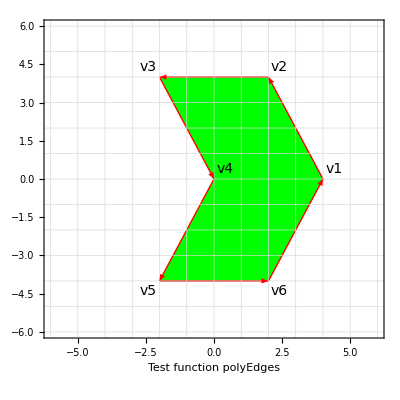

```mathematica
Show[plotPolyEdges[concaveHexagon], ImageSize -> "Medium"]
```

If the points are ordered counter clockwise, the area of the triangle formed by the rear must be negative A(rear) < 0. If the area of the triangle is zero A(rear) = 0, then the points are collinear. We would also like to clip collinear points, so will treat them as a rear, giving  A(rear) ≤ 0. We can write a function to test if a set of three consecutive points is a rear as follows:

```mathematica
rearTestPointsQ[vPrev_, v_, vNext_ ] :=triangleArea[vPrev, v, vNext] ≤ 0
```

We can test a vertex of a polygon as follows:

```mathematica
rearQ[ poly_, index_] := rearTestPointsQ @@ polyTake3[poly, index]
```

To clip off rear (v_(i-1), v_i, v_(i+1)) we just return (v_(i-1), v_(i+1)) discarding v_i.

```mathematica
clipRear[ poly_List ] := poly[[Select[indexes[poly], !rearQ[poly, #]&]]]
```

To find the convex hull, we just keep clipping off rears until there are no rears left. This amounts to repeatedly calling clipRear[...] on the result of clipRear[...], e.g. clipRear[clipRear[clipRear[poly]]], until there is no change from one application of clipRear[...] to the next. The Wolfram Language function FixedPoint[ f, expr] does precisely this - it applies f[...f[f[expr]]...] until there is no change in the result of f.

```mathematica
convexHullGraham[poly_] := FixedPoint[ clipRear, sortByTheta[poly]]
```

The only problem with this elegant solution is that we might need to recurse clipRear[...] so many times that we blow the execution stack. In particular, the Wolfram Language has a default recursion limit of 1024. However, we can set this limit to whatever we like (including infinity) provided we are sure that the computer system we are using has sufficient stack space. See $RecursionLimit in the Documentation Center for more details. Here is a function that plots a hull plus the original poly. Rears are circled in green:

```mathematica
plotHull[ hull_, originalPoly_, polyColour_:Yellow ] := Graphics[ 
{
polyColour, Polygon[originalPoly],
Blue, Circle[Mean[originalPoly], 0.1],
Blue, Arrow/@polyEdges[hull],
Black, polyVertexLabels[hull],
Green,If[ rearQ[hull, #],
Circle[ hull[[#]], 0.5] 
] &/@  indexes[hull]
},
standardPlotStyle
]
```

The test program below allows you to select a number of random points, and then apply a number of iterations of clipRear[...].

```mathematica
Manipulate[
DynamicModule[ {ps},
ps = sortByTheta[randomPointSet[ numberOfPoints ]];
Manipulate[
plotHull[Nest[ clipRear, ps, numberOfIterations], ps],
{{numberOfIterations, 0, "number of iterations"}, 0, 10, 1, SetterBar}, Paneled -> False
]
],
{{numberOfPoints, 3, "number of points"}, 3, 100, 1}
]
```

-Graphics-

The function convexHullGraham applies sufficient iterations of clipRear to determine the convex hull:

```mathematica
Manipulate[
DynamicModule[ {p, ps},
p = randomPointSet[ numberOfPoints ];
ps = sortByTheta[p];
plotHull[convexHullGraham[p], ps ]
],
{{numberOfPoints, 15, "number of points"}, 3, 100, 1}
]
```

-Graphics-

## Comparison of incremental and Graham scan convex hull functions

To compare the time performance of competing computational geometry functions we need the following:

A way of timing how long the function takes to process a given amount of data.

A set of data that we can use to time each algorithm.

A way of comparing the results of the experiment (usually a graph).

For our test data, we will take random point sets with a range of sizes from 4 to 40 members, so we can see how the functions perform as a function of size.

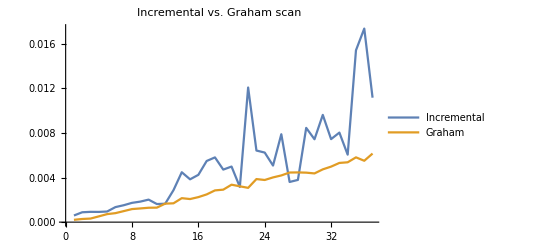

```mathematica
incrementalVsGrahamScanTiming[numberOfPoints_Integer:40] := Module[{testData},
testData := randomPointSet[#]&/@Range[4,numberOfPoints];
(* Plot the results of performing incremental and Graham scan convex hulls *)
ListLinePlot[{Timing[convexHullIncremental[#]][[1]]&/@testData, Timing[convexHullGraham[#]][[1]]&/@testData}, 
PlotLegends->{"Incremental", "Graham"},
PlotLabel->"Incremental vs. Graham scan"]]

incrementalVsGrahamScanTiming[40]
```

From the above:

The plot of each function has a slight upward curve. Each algorithm is based on sorting, and the time complexity is O(n^2) because of this.

Assuming both algorithms have been implemented with comparable efficiency, we see that the Graham scan is about twice as fast as the incremental algorithm at 40 points, but that the difference increases with the number of points. You can see this if you

The incremental algorithm shows much more sensitivity to the actual points in the point set than the Graham scan - you can see this clearly if you run the program several times. Its graph is more spiky and unpredictable.

The steps we have performed above to compare these two functions constitute a general recipe for comparing the time performance of competing computational geometry algorithms.

## Summary

In this chapter we have presented two contrasting algorithms for finding the convex hull of a set of points:

The incremental algorithm starts with a convex polygon and proceeds by adding points from the set whilst maintaining convexity.

The Graham scan, works pretty much in the opposite way. It begins by turning the points into a simple star shaped polygon by sorting them according to their angle relative to a given point. It then creates the convex hull by removing convexity through the mechanism of reverse ear clipping.

We also presented a simple recipe for comparing computational geometry algorithms and used it to compare the two convex hull algorithms.

## Chapter 10: General polygon triangulation

We have already seen how convex polygons can be triangulated simply by connecting vertexes. In this chapter, we will look at a more general algorithm for the triangulation of any polygon. A key part of this algorithm is finding the diagonals of a polygon, so we will consider this first.

## Polygon diagonals

A polygon diagonal is exactly what you might expect it to be:

Polygon diagonal: a line segment between two non-consecutive vertexes, v_i and v_j that is internal to the polygon, i.e. it does not intersect an edge.

This naturally means that v_i and v_j have direct line of sight of each other. The line segment s = v_i v_j is a diagonal of polygon P if:

For all edges, e, of P that are not incident to v_i or v_j, s and e do not intersect: s ∩e =0

s is internal to P between v_i and v_j

We can check that s is internal to P, by checking that s is strictly in the open cone (i.e. not running along an edge), counterclockwise, between vectors v_(i-1), v_i  and v_i, v_(i+1). This function checks to see if the point b is in the open cone of the angle subtended by the three points vPrev, v and vNext:

```mathematica
inConePointsQ[vPrev_, v_, vNext_, b_] := 
If[ leftOnQ[v, vNext, vPrev],
(* b is a convex vertex *) 
leftQ[v, b, vPrev] && leftQ[b, v, vNext], 
(* b is a reflex vertex *)
Not[leftOnQ[v, b, vNext]&& leftOnQ[b, v, vPrev]]  
]
```

Here is a version that operates directly on a polygon. The candidate diagonal is the line segment between vertexes indexI and indexJ:

```mathematica
inConeQ[poly_, indexI_, indexJ_ ] := inConePointsQ[ polyPrevVertex[poly, indexI], polyVertex[poly, indexI], polyNextVertex[poly, indexI], polyVertex[poly, indexJ] ]
```

Note that inConePointsQ only works when polygon vertexes are ordered according to our anti-clockwise standard. Here is a test program for inConePointsQ. To understand precisely what we mean by “strictly in cone”, try moving the point b around so that it is inside the polygon. What happens when it is on the edge of the polygon?

```mathematica
testInConePointsQ[] := Manipulate[ Graphics[{
Blue, Arrow[ {v, vNext}], 
Blue, Arrow[ {vPrev, v}], 
Blue, Arrow[ {vNext, vj}],
Blue, Arrow[ {vj, vPrev}],
If[ inConePointsQ[vPrev,v,vNext, b],Green,Red ], Arrow[ {v, b}], 
Black,pointLabels[ {vPrev, v, vNext, b}, {"vPrev", "v", "vNext", "b"}]
},
standardPlotStyle
], 
{{v,{-1,1}},{-5, -5}, {5,5}, 1, Locator},
{{vNext,{4,-4}},{-5,-5}, {5,5}, 1, Locator}, 
{{vPrev,{4,4}},{-5,-5}, {5,5}, 1, Locator},
{{vj,{5,0}},{-5,-5}, {5,5}, 1, Locator},
{{b,{-2,3}},{-5,-5}, {5,5}, 1, Locator}, 
"Move point b so that it is in the open cone",
"Note: the points must be ordered anti-clockwise for inConePointsQ to work!",
FrameLabel -> "Function inCone"
]

testInConePointsQ[]
```

-Graphics-

We now we have all we need to write a function to test for a polygon diagonal:

```mathematica
diagonalQ[ poly_, v1Index_, v2Index_ ] :=
inConeQ[poly, v1Index, v2Index ]&& 
inConeQ[poly, v2Index, v1Index ]&& Not[intersectPolyQ[ poly, polyVertex[poly, v1Index], polyVertex[poly, v2Index]]]
```

Here is a a test program for diagonalQ:

```mathematica
testDiagonalQ[] := Manipulate[
Module[ {isDiag = False},
isDiag = diagonalQ[poly, a,b];
Graphics[ 
{Blue,Arrow/@ polyEdges[poly],
If[ isDiag, Green, Red],
Text[Style[isDiag,16]],
Arrow[{poly[[a]], poly[[b]]}],
pointLabels[{poly[[a]],poly[[b]]}, {"a", "b"}, {0.7,0.7}],
Black, polyVertexLabels[poly, {0.3,0.3}],
Blue,Opacity[0.2],Polygon[poly]
},
standardPlotStyle]
],
"Select vertexes a and b and see if there is a diagonal between them or not",
{{a,1, "a"},1,6,  1, SetterBar}, 
{{b,3, "b"},1,6,  1, SetterBar}, 
{{poly, {{3,1},{1,4},{-4,3},{-3,-2}, {0,-4}, {4,-3} }},{-5, -5}, {5,5}, 1, Locator}, 
FrameLabel -> "Test function diagonalQ"
]

testDiagonalQ[]
```

-Graphics-

If you play about with the test program you will see that diagonalQ only works correctly when the polygon vertexes are ordered in an anti-clockwise direction. This is because it uses inConeQ that uses leftQ and leftOnQ, which are based on an anti-clockwise ordering.

## Finding polygon diagonals

Now that we can test to see if the line segment v_i v_j  is a polygon diagonal, all we need to do is apply this to pairs of polygon vertexes to find which pairs are diagonals. Consider the hexagon below.

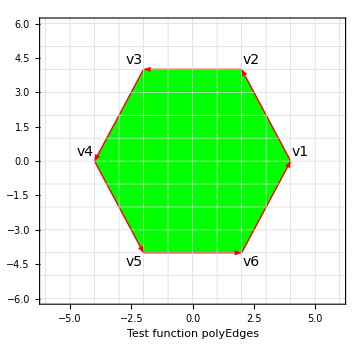

```mathematica
Show[ plotPolyEdges[ convexHexagon ], ImageSize -> Medium ]
```

To identify diagonals for a polygon P with n vertexes v_1... v_n  we need to identify all possible unique line segments between vertexes and check them to see if they are diagonals. We have to remember that we have three rules for candidate diagonals v_i v_j:

The two vertexes must be different, so i ≠ j

Diagonals v_i v_j and v_j v_i are the same line segment.

Line segments adjacent to v_i are polygon edges, so j ≠ i ± 1

We can generate a matrix of all possible combinations of vertex indexes as follows:

```mathematica
Block[{i,j},
Table[{i,j},{i,6},{j,6}]
]
```

{{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6}},{{2,1},{2,2},{2,3},{2,4},{2,5},{2,6}},{{3,1},{3,2},{3,3},{3,4},{3,5},{3,6}},{{4,1},{4,2},{4,3},{4,4},{4,5},{4,6}},{{5,1},{5,2},{5,3},{5,4},{5,5},{5,6}},{{6,1},{6,2},{6,3},{6,4},{6,5},{6,6}}}

Applying rule 1, we can ignore the matrix diagonal {1,1}, {2,2} ... {6,6} because i = j.

Applying rule 2, we must choose either all the numbers above or all those below the matrix diagonal in order to remove duplicates. This is a simple problem in combinatorics and Mathematica has a function that can give us this set of points directly:

```mathematica
Subsets[Range[1,6], {2}]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}}

It’s worth looking at this code in a bit more depth, because Subsets[...] is a very powerful and useful function. When there is no second parameter, Subsets[...] calculates the power set of a set, i.e. the set A of all possible subsets of set B. In set notation this is {A : A ∈ B}.  So, for example, the power set of {1, 2, 3} is {{0}, {1}, {2}, {3}, {1,2}, {1,3}, {2,3}, {1,2,3}}. Notice that this contains the empty set {} and {1, 2, 3} itself because each set always contains at least the empty set and itself.

The second parameter of Subsets specifies a filtering rule - in this case, we take only those subsets that contain exactly two members: {A : A ∈ B  and |A| = 2} which gives us the numbers we need.

Applying rule 3, we must filter out all values where j = i ± 1. This is trivial. Here is the final function:

```mathematica
candidateDiagonalIndexes[ poly_] := Block[{len = Length[poly]}, 
Select[
Subsets[Range[1,len], {2}],
(#[[2]] ≠ polyIndex[len, #[[1]] + 1] ) && (#[[2]] ≠ polyIndex[len, #[[1]] -1 ]) &]
]

candidateDiagonals[ poly_ ] := { poly[[ #[[1]] ]], poly[[ #[[2]] ]] } & /@ candidateDiagonalIndexes[poly]
```

These two functions give us all possible line segments between two vertexes that are not polygon edges. This is the set of candidate diagonals. A subset of these will be interior to the polygon and therefore be actual diagonals.

Here is a general test function for diagonal functions:

```mathematica
testDiagonalFunctions[ p_, diagonalFn_, caption_ ] := Manipulate[
Graphics[ {
Blue,Arrow/@ polyEdges[poly ],
Red, Line/@diagonalFn[poly],
Black, polyVertexLabels[poly, {0.3,0.3}],
Blue,Opacity[0.1],Polygon[poly]
},
standardPlotStyle
],
{{poly, p},{-5, -5}, {5,5}, 1, Locator}, 
caption,
FrameLabel -> Row[{"Test function " , diagonalFn }]
]
```

Let’s see exactly what our candidate diagonals function does:

```mathematica
testDiagonalFunctions[ randomSimpleStarShapedPoly[6],candidateDiagonals, "Candidate diagonals, including exterior diagonals"]
```

-Graphics-

Now it is a simple matter to find the actual diagonals by applying diagonalQ to each of the candidate diagonals:

```mathematica
diagonalIndexes[ poly_] :=Select[ candidateDiagonalIndexes[poly], diagonalQ[poly, #[[1]], #[[2]]] &]

diagonals[ poly_ ] := { poly[[ #[[1]] ]], poly[[ #[[2]] ]] } & /@ diagonalIndexes[poly]
```

Here is a test program. Notice how only true diagonals (i.e. line segments between two vertexes that are not edges and are interior to the polygon) are selected:

```mathematica
testDiagonalFunctions[ randomSimpleStarShapedPoly[6],diagonals, "True (interior) diagonals only"]
```

-Graphics-

## Polygon triangulation by ear tip removal

Any polygon may be triangulated by clipping its ear tips. You can find a proof of this in [ORourke1], but it should be fairly obvious.  Each ear tip is a triangle and if we keep clipping them off, then we must ultimately reduce the polygon to a set of triangles. Vertex v is an ear tip if the line segment v_prev v_next is a diagonal of the polygon. We can therefore detect an ear tip as follows:

```mathematica
earTipIndexQ[ poly_,index_ ] :=Block[{len = Length[poly]},
diagonalQ[ poly,polyPrevIndex[len, index], polyNextIndex[len, index] ]]
```

This next function is an ear tip detector. It returns a list containing a True/False ear tip value for each vertex of a polygon:

```mathematica
earTipBooleans[ poly_ ] := earTipIndexQ[ poly, #] & /@ indexes[poly]
```

The Wolfram Language has a very useful function called Pick that returns all elements of collection A for which the corresponding element in collection B is True. So we can use the earTipBooleans to directly pick out the earTipIndexes and earTipVertexes as follows:

```mathematica
earTipIndexes[ poly_] := Pick[ indexes[poly], earTipBooleans[poly]]

earTipVertexes[ poly_ ] := Pick[ poly, earTipBooleans[ poly ]]
```

Here is a test program that demonstrates ear tip detection. Ear tips are circled in green:

```mathematica
testEarTips[ p_ ] :=Manipulate[
Graphics[{
Blue, Arrow/@ polyEdges[poly],
Red, Line/@diagonals[poly],
Green, Circle[#, 0.5] &/@ earTipVertexes[poly],
Black, polyVertexLabels[poly, {0.3,0.3}],
Blue,Opacity[0.1],Polygon[poly]
},
standardPlotStyle
],
"Ear tips have a green circle around them. Diagonals are red lines.",
{{poly, p},{-5, -5}, {5,5}, 1, Locator},
FrameLabel -> "Test function earTipVertexes"
]

testEarTips[ randomSimpleStarShapedPoly[7] ]
```

-Graphics-

### Strategy for implementing the triangulation algorithm

Our triangulation algorithm involves clipping vertexes from the polygon and this means we need to keep track of three things:

The polygon vertexes (obviously!).

The original index of each vertex in the original polygon prior to any removals.

The ear status of each vertex. This can change as vertexes are removed.

The reason for point 2) is that the original index is our unique identifier for each vertex. As such it must be preserved as we clip vertexes and the indexing changes.

We can keep track of all this most easily by creating an enriched polygon data structure that contains this information. The easiest way to do this is to create a List comprising Lists of the vertex data, the ear tip Boolean values and the original indexes of each vertex. In order to ensure we keep everything in the right place in the new List we will create it using the following function:

```mathematica
addEarTipData[ poly_ ] := {poly, earTipBooleans[ poly ],indexes[poly]}
```

Next, we need to define some constants so that we can access the parts of the enriched polygon data structure:

```mathematica
ePoly = 1;
eEarTips = 2; 
eOriginalIndexes = 3;
```

When we delete a polygon vertex with index i, we also have to delete the corresponding ith elements from the ear tip Boolean and original index Lists. To prevent possible errors, we need a function to handle this in one go:

```mathematica
epDelete[ ep_, i_ ] := Block[{ len = Length[ ep[[ePoly]] ], index},
index = polyIndex[len, i];
{ 
Delete[ep[[ePoly]], index ],
Delete[ep[[eEarTips]], index ],
Delete[ep[[eOriginalIndexes]], index ]
}
]
```

Now we can write a clipping function that operates on this data structure. The function clipEarVertex removes vertex v_i. In the new, clipped polygon, the coordinates of the two vertexes that were adjacent to it are v_(i-1) and v_i and these now have their ear status updated. Always check that the vertex is an ear before calling this function - the function itself doesn’t check this!

```mathematica
clipEarVertex[ ep_ , i_]:= Block[
{ clipped , iBefore = 1,iAfter = 1 , len = Length[ ep[[ePoly]] ] },
clipped = epDelete[ep, i];
(* Calculate the indexes of the points before and after the clipped point in the new clipped polygon with length len - 1 *)
iBefore = polyIndex[ len - 1, i - 1];
iAfter = polyIndex[ len - 1, i];
(* Update the ear tip status of these two points *)
clipped[[eEarTips, iBefore ]] = earTipIndexQ[clipped[[ePoly]], iBefore];
clipped[[eEarTips, iAfter ]] = earTipIndexQ[clipped[[ePoly]], iAfter];
(* Return the clipped polygon *)
clipped
]
```

As we said earlier, in order to triangulate a polygon, we clip off triangular ears until we are left with a single triangle. Each ear is one of the triangles in the triangulation, as is the final triangle. So we now need a function to find ears. This function takes a polygon and returns the index of the first clipable vertex:

```mathematica
findEarTipIndex[poly_List] := First[ Select[ indexes[poly], earTipIndexQ[poly, #]&, 1] ]
```

### Implementing a polygon triangulation function

We now have all the tools we need to write a polygon triangulation function. Our function will work according to the following algorithm adapted from [ORourke1]:

Enrich the polygon data with vertex ear tip status and original index data (function addEarTipData).

While the polygon length is >= 3 (i.e. stop when we have reduced the polygon to a triangle)

Find an ear tip vertex  v_i

Clip the ear tip

Output  triangle comprising the original indexes of v_(i-1), v_i and v_(i+1)

Delete v_i

Update the ear tip status of v_(i-1) and v_(i+1) (where i-1 and i+1 are the original indexes prior to deleting v_i)

When it comes to implementing this algorithm, there are certain things that we have to take into account. One unavoidable subtlety is that when vertex v_i is removed from the polygon, the List indexes of all vertexes v_(j > i) decrease by 1. This is why it is important to store the original vertex List indexes in the polygon data structure. This issue could be removed by using a circular linked list (rather than a List) as in [ORourke1], but this not the natural representation for a polygon in the Wolfram Language, and it would make the rest of the code more complex and less efficient.

Another implementation issue arises in the While loop, where we need to output the vertexes of the found triangles. An obvious way to do this would be to use the function AppendTo[...] to append them to a List that we then return at the end of the function. However, appending to a List is quite computationally expensive in the Wolfram Language, because the language optimized to manipulate complete Lists, not to construct them on the fly. There is a much more efficient way to achieve the same result using the functions Sow and Reap. These functions appear to be unique to the Wolfram Language and are very convenient. Their operation is simple - the function Sow appends a result to a temporary queue that can be obtained by calling Reap. The mechanism is designed to be maximally efficient, and it is always the preferred way to return intermediate values in a calculation in the Wolfram Language. Finally, we must remember that after the while loop, the polygon P has been reduced to a single triangle, and we need to Sow its coordinates to complete the triangulation. Taking these considerations into account, the implementation of the triangulation algorithm is actually pretty simple:

```mathematica
triangulatePolyIndexes[ poly_ ] := Reap[
Module[{ earTipPoly,len, e, ePrev, eNext},
earTipPoly = addEarTipData[poly];
len = Length[poly];
e = ePrev = eNext = 1;
While[ len > 3,
e =findEarTipIndex[ earTipPoly[[ePoly]] ];
ePrev = polyPrevIndex[ len, e ];
eNext = polyNextIndex[ len, e ];
(* Sow the ear triangle *)
Sow[{ 
earTipPoly[[eOriginalIndexes, ePrev]],
earTipPoly[[eOriginalIndexes, e]],
earTipPoly[[eOriginalIndexes,eNext]]
}];
earTipPoly = clipEarVertex[ earTipPoly, e ];
len = Length[ earTipPoly[[ePoly]] ];
];
(* Sow the last triangle, which is all that is left of p *)
Sow[{ 
earTipPoly[[eOriginalIndexes,1]],
earTipPoly[[eOriginalIndexes,2]],
earTipPoly[[eOriginalIndexes,3]]
}]
]
][[2,1]]

(* Triangulate and return the triangulation vertexes *)
earTriangulatePoly[ poly_ ] := { poly[[ #[[1]] ]], poly[[ #[[2]] ]], poly[[ #[[3]] ]] } &/@triangulatePolyIndexes[poly]
```

For example:

```mathematica
gridFormValue[{
triangulatePolyIndexes[concaveHexagon], 
earTriangulatePoly[concaveHexagon]
}]
```

triangulatePolyIndexes[concaveHexagon] | {{6,1,2},{2,3,4},{6,2,4},{4,5,6}}
earTriangulatePoly[concaveHexagon] | {{{2,-4},{4,0},{2,4}},{{2,4},{-2,4},{0,0}},{{2,-4},{2,4},{0,0}},{{0,0},{-2,-4},{2,-4}}}

You can see that our triangulation is a very  simple data structure - a list of triplets, one for each triangle -  that comes in two flavours:

Triangulation indexes - each triangle is represented by a triple of indexes that index vertexes in the polygon.

Triangulation vertexes - each triangle is represented by triples of actual polygon vertexes.

Generally speaking, it is most convenient to calculate the indexes into the polygon (or point set), and then convert these to vertexes as you need to do so. This is exactly what the triangulationIndexesToVertexes[...] function does. It takes a set of points and a set of triangulation indexes and converts that to a set of triangulation vertexes:

```mathematica
(* Given the triangulation indexes, return the vertexes *)
triangulationIndexesToVertexes[ pts_, triangulationIndexes_ ] := { pts[[ #[[1]] ]], pts[[ #[[2]] ]], pts[[ #[[3]] ]] } &/@triangulationIndexes
```

For example:

```mathematica
gridFormValue[{
triangulatePolyIndexes[concaveHexagon],
earTriangulatePoly[concaveHexagon],
triangulationIndexesToVertexes[concaveHexagon, triangulatePolyIndexes[concaveHexagon]]
}]
```

triangulatePolyIndexes[concaveHexagon] | {{6,1,2},{2,3,4},{6,2,4},{4,5,6}}
earTriangulatePoly[concaveHexagon] | {{{2,-4},{4,0},{2,4}},{{2,4},{-2,4},{0,0}},{{2,-4},{2,4},{0,0}},{{0,0},{-2,-4},{2,-4}}}
triangulationIndexesToVertexes[concaveHexagon,triangulatePolyIndexes[concaveHexagon]] | {{{2,-4},{4,0},{2,4}},{{2,4},{-2,4},{0,0}},{{2,-4},{2,4},{0,0}},{{0,0},{-2,-4},{2,-4}}}

Next, we need a utility function that allows us to plot triangulations.

## Plotting triangulations

This function takes a polygon or point set (see later) and one of its triangulations, and plots it out. If you don’t have access to the original polygon or point set just pass an empty List as the first parameter - it will then just plot the triangles. We have given the function some optional arguments (earTips, etc.) so that we can reuse it later.

```mathematica
plotTriangulation[ poly_, triangles_,opt:OptionsPattern[{earTips->True, triangleLabels -> False, arrows->True}] ] :=
Module[
 { centers},
centers = Mean /@ triangles;
Graphics[ 
{
drawColouredPolys[triangles],
If[Length[poly] ≠ 0, polyVertexLabels[poly, {0.3,0.3}]],
(* Draw arrows to show direction of triangles *)
If[ OptionValue[ arrows ],
{Black, Arrow /@ polyEdges /@ triangles}],
(* Show the index of each triangle in the triangles List  *)
If[ OptionValue[triangleLabels],
{White,Text[Style[Row[{"Δ",#}], 14], centers[[#]]] &/@ Range[Length[triangles]]}],
(* Show the ear tips *)
If [ OptionValue[earTips], {Green, Circle[#, 0.5] &/@ earTipVertexes[poly]}]
},
standardPlotStyle
]
]
```

Here is a simple example of the program in action:

```mathematica
Manipulate[
plotTriangulation[convexHexagon,  fanTriangulatePoly[convexHexagon, startVertex], triangleLabels->True],
{{startVertex, 1,"start vertex"}, 1, Length[convexHexagon],1 , SetterBar}
]
```

-Graphics-

Here is a convenience function to triangulate a polygon and plot it out in one go:

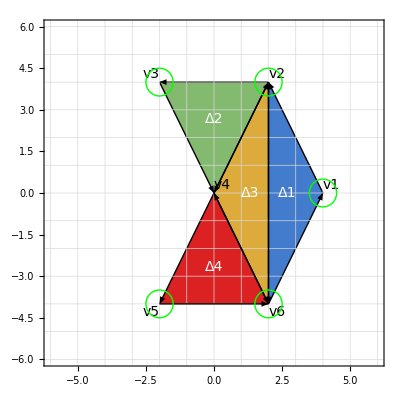

```mathematica
triangulatePolygonAndPlot[ poly_, opts:OptionsPattern[{earTips->True, triangleLabels -> False, arrows->True}] ] := plotTriangulation[poly, earTriangulatePoly[poly], opts]

triangulatePolygonAndPlot[ concaveHexagon , triangleLabels->True]
```

The program below triangulates random simple polygons with up to 15 vertexes.

```mathematica
Manipulate[ 
triangulatePolygonAndPlot[ randomSimpleStarShapedPoly[numberOfSides]], {{numberOfSides, 8,"number of sides"}, 3,15, 1, SetterBar}
]
```

-Graphics-

Here is how we can list all the triangles in a table:

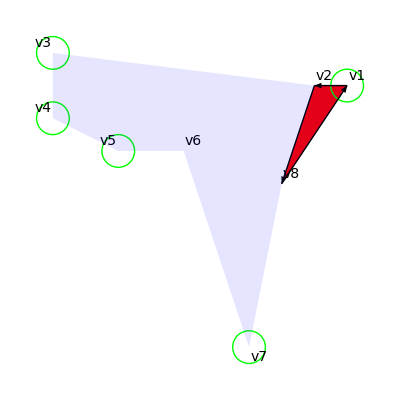
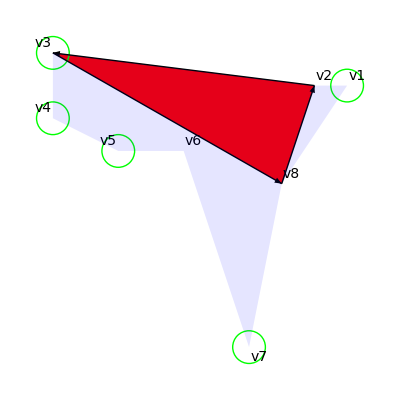
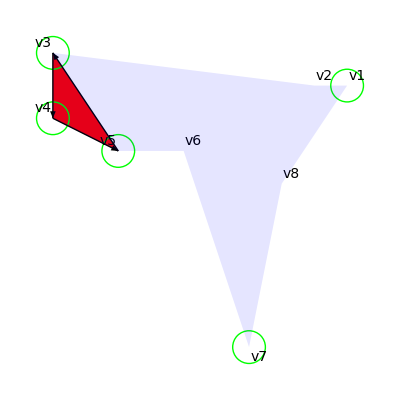
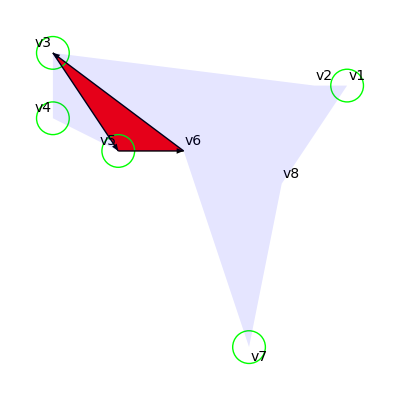
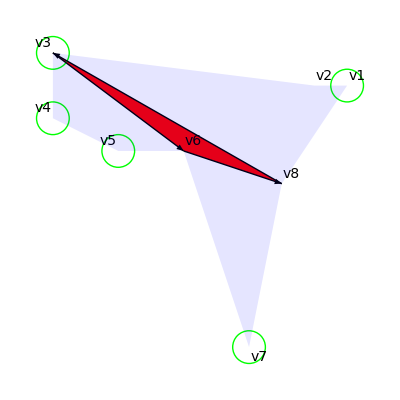
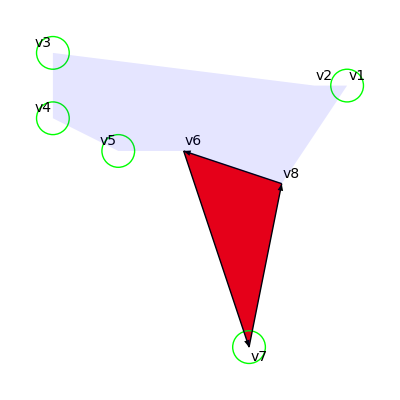

```mathematica
triangulationTable[ poly_ ] :=Graphics[ 
{Red,
(* Draw the triangle *)
Polygon[#],
Green,
(* Draw the ear tip vertexes *) 
Circle[#, 0.5] &/@ earTipVertexes[poly],
Black,
(* Label the polygon vertexes *)
polyVertexLabels[poly, {0.3,0.3}],
(* Draw each triangle using arrows *)
Arrow[{#[[1]], #[[2]]}],
Arrow[{#[[2]], #[[3]]}],
Arrow[{#[[3]], #[[1]]}],
Blue,Opacity[0.1],
(* Draw the whole polygon *)
Polygon[poly]
}
]& /@ earTriangulatePoly[ poly ]

triangulationTable[ randomSimpleStarShapedPoly[8]]
```

## Summary

Polygon triangulation is quite complex except in the case of simple convex polygons.

The approach we took in this Chapter was to identify polygon diagonals, and remove ear tips to find the triangles. This is very much the reverse of the Graham scan, where we removed reverse ear tips to create a convex hull.

## Chapter 11: Point set triangulation and the dual graph

In the previous chapter, we considered polygon triangulation. In this chapter we consider the more general case of triangulating any point set. Every triangulation of a point set will be convex [ORourke1], so there is a strong relationship between triangulation algorithms and convex hull algorithms. In fact, as we will see, the same algorithm can often be adapted to do both or either. We will also see how to construct the dual graph of a triangulation and create the visibility graph of a polygon.

## Incremental point set triangulation algorithm

We can triangulate a point set using a fairly simple incremental algorithm that in [Devadoss1] is called the, “triangle-splitting triangulation algorithm”, for obvious reasons:

Take the convex hull, H of the point set. This is by definition a convex polygon.

Triangulate the convex hull by joining up vertexes to get triangulation T.

For each point p, strictly inside the hull (i.e. not on the hull boundary):

For each triangle that p is inside or on:

Remove the triangle from T

Triangulate the triangle on p and add the triangulation to T

Remove any degenerate triangles (three collinear points) from T

This will result in a complete triangulation of the point set. Let’s look at an implementation.

We already have most of the code in place to do this, but we still need a function for step 3.1 to find which triangle a point is inside. However, there is a slight complexity here: if there are three collinear points in the point set, this means that a point will be on an edge that might be shared by two triangles. So the function will need to return both triangles:

```mathematica
findTriangles[ trs_?triangleListQ, pt_?pointQ] := Select[ trs, insideOnConvexQ[ #, pt]&, 2]
```

We now have the tools to implement the rest of the algorithm. We have chosen to use the incremental convex hull algorithm because the Graham Scan returns the minimum set of points that defines the hull by removing any triples of collinear points. However, in this case, we need to preserve these because we need to subtract all points on the hull from the point set to leave only the points inside the hull. Note that collinear points can give zero area triangles, so we must remember to filter any of these out of the result:

```mathematica
triangulatePointSet[ pts_?pointListQ] :=Module[{hull, triangles, ptsInsideHull, tr, trs},
(* Be sure to use only the minimum set of points in the convex hull otherwise some boundary points will be omitted from ptsInsideHull and hence the triangulation *)
hull= convexHullIncremental[pts];
triangles = fanTriangulatePoly[ hull ];
ptsInsideHull = Complement[pts , hull];

For[ i = 1, i ≤ Length[ptsInsideHull], i++,
tr = findTriangles[ triangles, ptsInsideHull[[i]] ];
(trs= triangulateOnPoint[#,ptsInsideHull[[i]] ];
triangles = Join[ Complement[triangles, {#} ], trs])&/@tr;
];
(* Filter out any zero area triangles *)
Select[triangles, (triangleArea[#] ≠ 0)&]]
```

In the test program below, you can see the convex hull and the triangulation. Drag the Locators around and see how the triangulation and hull change. If you turn off the triangulation and hull, and move the slider, you can see how each point is added to the triangulation. Note that (as usual) overlapping points are not allowed, so if you make two points overlap, the algorithm will fail.

```mathematica
testTriangulatePointSet[ nPts_Integer:30]:= Manipulate[
Module[{ trs, hull},
trs = triangulatePointSet[ pts ];
hull= convexHullGraham[pts];
Graphics[{
If [ showTriangulation,{
Black, Arrow/@polyEdges/@ trs,
Opacity[0.4],drawColouredPolys[trs, "BrightBands"]
}],
If [ showHull,{
Red,Disk[#, 0.3]&/@hull
}]
},
standardPlotStyle]
],
"Triangluate a point set using the triangle-splitting triangulation algorithm",
{{showHull, False, "show hull points"}, {True, False}},
{{showTriangulation, True,"show triangulation"}, {True, False}},
{{pts,randomPointSet[nPts]},{-5, -5}, {5,5}, 1, Locator}
]

testTriangulatePointSet[10]
```

-Graphics-

## Simple incremental point set triangulation with convex hull

This very simple incremental algorithm illustrates that a point set triangulation algorithm can also be a convex hull algorithm. It calculates a triangulation of a point set and gives the convex hull as a by-product. The algorithm has the limitation that it only works for point sets in general position, i.e. no three points collinear. The algorithm works as follows:

Sort the point set S by the x coordinate of the points.

Create a convex polygon P (a triangle) from the first three points of the sorted point set.

The initial point set triangulation is T(S) = P

For i = 4 to number of points

Split P on the tangents to point p_i into a convex chain C_c and a reflex chain C_r

P = P ∪ p_i

Triangulate the reflex chain C_r on the point p_i and call this T_i(C_r)

T(S) = T(S)∪T_i(C_r)

Note: At all times keep P sorted counter-clockwise. At the end of this algorithm the triangulation is in T and the convex hull is in P.

Because the points are sorted by x, this guarantees that when we add the next point to the initial polygon formed by the first three points, that point is further along the X axis and therefore it is external to the polygon. We can then use our strategy of finding the polygon tangent points to external points and splitting the polygon: the convex chain is used to create the convex hull, and the reflex chain to create a triangulation. Here is an implementation:

```mathematica
triangulateAndConvexHull[ pts_?pointListQ ] :=Block[{spts, poly, cc, cr, trs},
spts = Sort[ pts,(#1[[x]] >= #2[[x]])&];
poly = sortByTheta[spts[[{1,2,3}]]];
trs = Reap[
Sow[{poly}];
For[ i =4, i ≤ Length[spts], i++,
{cc, cr} =splitPolyOnTangents[ poly, spts[[i]] ];
poly = sortByTheta[Join[ cc,{spts[[i]]}]];
Sow[triangulateChain[ cr,spts[[i]]]]
];
];
{Flatten[trs[[2]], 2], poly}
]
```

Here is a test program. Notice that if you drag points such that the point set is no longer in general position, you may get an error:

```mathematica
testTriangulateAndConvexHull[ nPts_Integer:30]:= Manipulate[
Module[{ trs, hull},
{trs, hull} = triangulateAndConvexHull[ pts ];
Graphics[{
If [ showTriangulation,{
Black, Arrow/@polyEdges/@ trs,
Opacity[0.4],drawColouredPolys[trs, "BrightBands"]
}],
If [ showHull,{
Red,Disk[#, 0.3]&/@hull
}]
},
standardPlotStyle]
],
"Triangluate a point set using the incremental triangulation with convex hull algorithm",
{{showHull, False, "show hull points"}, {True, False}},
{{showTriangulation, True,"show triangulation"}, {True, False}},
{{pts,randomPointSetGP[nPts]},{-5, -5}, {5,5}, 1, Locator}
]

testTriangulateAndConvexHull[10]
```

-Graphics-

## Finding the triangles for an edge in a triangulation

Given a triangulation of a point set, any edge will either be on the convex hull of the triangulation, in which case it only has one associated triangle, or it will be internal to the convex hull, in which case it has two associated triangles. Either way, it is often useful, given an edge, to be able to find the associated triangles. We can do this as follows:

```mathematica
findTriangleIndexesForEdge[ trs_?triangleListQ, edge_?lineSegmentQ] :=
Select[ indexes[trs], 
MemberQ[ polyEdges[ trs[[#]] ], edge ] ||
MemberQ[ polyEdges[ trs[[#]] ], Reverse[edge] ]&]
```

It is important to test for an edge going both ways between two vertexes. For example, for an edge between vertexes v_n and  v_(n+1) we test the pairs v_n  v_(n+1) and the reverse,   v_(n+1) v_n. With this new function in place, it is trivial to find the convex hull edges from the triangulation - they are those edges that have only one associated triangle:

```mathematica
hullEdgesFromTriangulation[ trs_ ] :=Block[{edges},
edges =Flatten[ polyEdges /@ trs, 1];
Select[ edges, Length[findTriangleIndexesForEdge[ trs, #]] == 1&]
]
```

Here is a simple test program:

```mathematica
testFindTriangleIndexesForEdge[ nPts_Integer:30 ]:= Manipulate[
Module[{ trs, edges, currentEdge, trIndexes, hullEdges },
trs = triangulatePointSet[ pts ];
edges = Flatten[polyEdges /@ trs, 1];
currentEdge = edges[[selectedEdge]];
numEdges =Length[ edges];
trIndexes = findTriangleIndexesForEdge[ trs, currentEdge];
hullEdges = hullEdgesFromTriangulation[ trs ];

Graphics[{

(* Draw the triangulation *)
{Opacity[0.4],
drawColouredPolys[trs, "BrightBands"]},

(* Draw the selected edge and highlight its adjacent triangles *)
Blue, Thick,Arrow /@ polyEdges[trs[[#]]]&/@ trIndexes,
Red, Arrow[ currentEdge],
Black,Text[Style[Row[{"△", #}], 14], Mean[trs[[#]]]]&/@trIndexes,
Black,Text[Style[Row[{"e", selectedEdge}], 14], Mean[currentEdge]],

(* Draw the hull *)
If[ showHull,
{Black, Thick, Line /@ hullEdges}
]

},
standardPlotStyle]
],
{{selectedEdge, 1, "selected edge"}, 1,Dynamic[numEdges], 1},
{{showHull, False, "show hull"}, {True, False}},
{{pts,randomPointSet[nPts]},{-5, -5}, {5,5}, 1, Locator}
]

testFindTriangleIndexesForEdge[10]
```

-Graphics-

## The dual graph of a triangulation

A graph is mathematical structure that may be defined as follows:

Graph: a system of vertexes (also called nodes) connected in pairs by edges.

Directed graph: a graph where all edges are directed (i.e. have a direction from a start vertex to an end vertex).

Undirected graph: a graph where none of the edges are directed.

Simple graph: An undirected graph in which both multiple edges and loops between vertexes are disallowed.

Mixed graph: a graph where some but not all of the edges are directed.

Planar graph: a graph that can be drawn in the plane in such a way that no edges cross each other.

The graph is an interesting object in terms of computational geometry because it captures the abstract relationships between vertexes and edges without any concern for actual vertex coordinates.

All graphs of triangulations are undirected planar graphs. They are undirected because there is no preferred start and end point for each edge. They are planar because each edge is between two adjacent triangles.

Adjacent triangles: two triangles that share a common edge.

We can plot the relationships between adjacent triangles by creating the dual graph of the triangulation:

Dual graph of a triangulation: a graph obtained by defining a vertex inside each triangle and then drawing an edge between vertexes of triangles that share an edge (are adjacent). [Taslakian1]

If you examine any triangulation of more than 3 points, you see that each triangle shares 1, 2 or 3 edges with another triangle. As we mentioned above, triangles that share a common edge are called adjacent triangles.

The problem of finding the dual graph of a triangulation reduces to the problem of identifying adjacent triangles. The dual graph elides the geometry of the triangulation by representing each triangle as a simple node in a graph. It emphasises adjacency relationships between triangles by representing these as edges between nodes. Consider the triangulation of the concave hexagon we produced earlier:

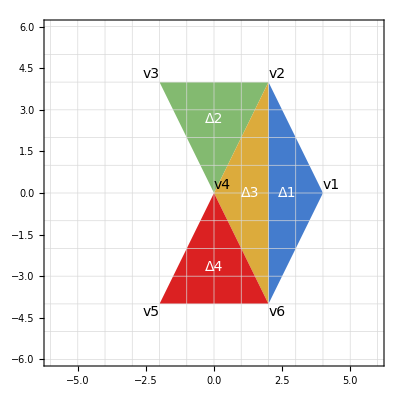

```mathematica
triangulatePolygonAndPlot[ concaveHexagon, earTips->False, arrows -> False,triangleLabels -> True]
```

Triangles labelled Δ1, Δ2 and Δ4 have only one adjacent triangle, which is Δ3. However, Δ3 has 3 adjacent triangles, Δ1, Δ2 and Δ4. By inspection, the dual graph of this triangulation is therefore:

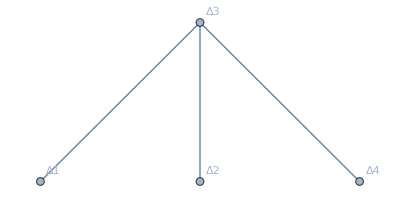

```mathematica
Graph[{"Δ1"<->"Δ3", "Δ2"<->"Δ3", "Δ4"<->"Δ3"}, VertexLabels->"Name", ImagePadding->10]
```

The Wolfram Language has excellent support for graphs and networks, and we have used the Graph[...] function above to plot out the graph. We will take a closer look at this later.

For two triangles to share a common edge, they must have two common vertexes. Suppose we perform a triangulation using function earTipriangulationIndexes[...] that returns each triangle as a set of three indexes into the original List of polygon vertexes. We will refer to these triangles as index triangles because they comprise indexes not vertexes. We can define an index triangle by the following pattern and test functions:

```mathematica
indexTrianglePattern = { _?IntegerQ, _?IntegerQ, _?IntegerQ };

indexTriangleQ[ ti_ ] := MatchQ[ ti, indexTrianglePattern ]

indexTriangleListQ[ itl_ ] := MatchQ[ itl, {indexTrianglePattern..}]
```

If we take two index triangles, T_1 and T_2, then if they have an edge in common, the set that is the intersection of T_1 and T_2 must have precisely two members i.e.

|T_1∩ T_2| =2

You can see this quite easily in the symbolic example below, where index triangles T_1 and T_2 have three indexes in common, T_1 and T_3 have two indexes in common (this is what we want!), T_1 and T_4 have one index in common and T_1 and T_5 have no indexes in common:

```mathematica
Subscript[T, 1]= {Subscript[i, 1], Subscript[i, 2], Subscript[i, 3]};
Subscript[T, 2]= {Subscript[i, 2], Subscript[i, 1], Subscript[i, 3]}; 
Subscript[T, 3]= {Subscript[i, 1], Subscript[i, 2], Subscript[i, 4]}; 
Subscript[T, 4]= {Subscript[i, 1], Subscript[i, 4], Subscript[i, 5]};
Subscript[T, 5]= {Subscript[i, 4], Subscript[i, 5], Subscript[i, 6]};

gridFormValue[{
Length[ Subscript[T, 1]∩ Subscript[T, 2]],
Length[ Subscript[T, 1]∩ Subscript[T, 3]],
Length[ Subscript[T, 1]∩ Subscript[T, 4]],
Length[ Subscript[T, 1]∩ Subscript[T, 5]]
}]
```

Length[T_1∩T_2] | 3
Length[T_1∩T_3] | 2
Length[T_1∩T_4] | 1
Length[T_1∩T_5] | 0

The function adjacentQ returns True if the two input sets have exactly two vertexes (one edge) in common. We have kept the arguments to this function very general so that it will work with both index triangles and normal triangles:

```mathematica
adjacentQ[ it1_List, it2_List ] := Length[it1 ∩ it2] == 2
```

This suggests a simple brute force algorithm where we take each index triangle in turn and compare it against the others. We stop when we have found three adjacent triangles. So for any index triangle with index i in the List of index triangles itl, we can find the indexes of all adjacent index triangles, and construct the edges of the dual graph as follows:

```mathematica
adjacentTriangleIndexes[ i_Integer, itl_List ] := 
{i, #}&/@Select[indexes[itl],adjacentQ[itl[[i]],itl[[#]]]&, 3]
```

Because any triangle can have no more than three adjacent triangles, we have constrained Select to stop searching when it has found three items. The function adjacentTriangleIndexes outputs a List of graph edges for the triangulation dual graph of the form:

{{i,j}} if index triangle i shares an edge with index triangle j

{{i,j}, {i,k}} if index triangle i shares an edge with index triangles j and k

{{i,j}, {i,k}, {i,m}}  if index triangle i shares an edge with index triangles j and k and m

Let’s look at an example of this for the concave hexagon:

```mathematica
gridFormValue[{
adjacentTriangleIndexes[ 1,triangulatePolyIndexes[ concaveHexagon ]],
adjacentTriangleIndexes[ 2,triangulatePolyIndexes[ concaveHexagon ]],
adjacentTriangleIndexes[ 3,triangulatePolyIndexes[ concaveHexagon ]]
}]
```

adjacentTriangleIndexes[1,triangulatePolyIndexes[concaveHexagon]] | {{1,3}}
adjacentTriangleIndexes[2,triangulatePolyIndexes[concaveHexagon]] | {{2,3}}
adjacentTriangleIndexes[3,triangulatePolyIndexes[concaveHexagon]] | {{3,1},{3,2},{3,4}}

We can find the complete graph by applying this function across all the triangles. However, we need to note that edges {i,k} and {k,i} are the same edge of the dual graph, and we need to delete any such duplicates. The dual graph as a set of edges is therefore given by:

```mathematica
adjacentTriangleIndexes[ itl_List ] := DeleteDuplicates[Flatten[adjacentTriangleIndexes[#, itl]&/@Range[Length[itl]], 1], (#1 == Reverse[#2]) &]
```

For example:

```mathematica
adjacentTriangleIndexes[triangulatePolyIndexes[ concaveHexagon ]]
```

{{1,3},{2,3},{3,4}}

We can use the Wolfram Language Graph[...] function to plot the dual graph for the triangulation of the concave hexagon. Note that the positions of the nodes don’t matter at all - we can put them where we like. All that the graph is concerned about is the connections between the nodes:

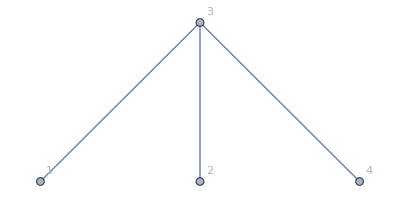

```mathematica
Graph[#[[1]]<-> #[[2]]&/@adjacentTriangleIndexes[ triangulatePolyIndexes[concaveHexagon] ], VertexLabels->"Name", ImagePadding->10]
```

Happily, this is the same as the result as we got from inspection.

The dual graph is usually shown as an overlay on the triangulation. First we write a function to plot the dual graph in the appropriate coordinates:

```mathematica
plotDualGraph[ poly_  ] :=Module[ 
{triangles = earTriangulatePoly[poly], centers, dualGraph},
centers = Mean /@ triangles;
dualGraph = adjacentTriangleIndexes[triangulatePolyIndexes[poly]];
Graphics[ 
{
Disk[#, 0.1]&/@ centers,
Line[{centers[[ #[[1]] ]], centers[[ #[[2]] ]]}]&/@dualGraph
},
standardPlotStyle
]
]
```

Next, we overlay the triangulation and dual graph plots:

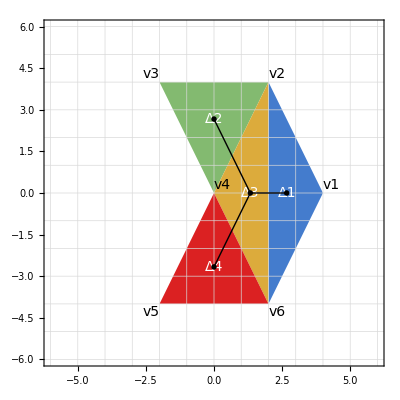

```mathematica
Show[triangulatePolygonAndPlot[ 
concaveHexagon, earTips->False, arrows -> False,triangleLabels -> True], plotDualGraph[ concaveHexagon ]
]
```

Here is a program that lets you move vertexes around. Note that the algorithms only work for simple polygons (no self-intersections, no duplicate points), so the demo shows an error condition (goes red) when this condition is not met.

```mathematica
Manipulate[
If[simplePolyQ[poly],
Show[{
triangulatePolygonAndPlot[ poly, earTips->False, arrows -> False,triangleLabels -> True],
plotDualGraph[ poly ]
}],
Graphics[{Opacity[0.5], Red, Polygon[poly]}, standardPlotStyle]
],
{{poly,5 regularPoly[12]},{-5, -5}, {5,5},1, Locator}
]
```

-Graphics-

The dual graph gives us a way to compare triangulations based on the relationships between their triangles, rather than on their geometry. If two triangulations have the same dual graph, then they can be distorted so they overlap one another and are identical.

## Analysing a triangulation using graph theory

We can tell quite a lot about a triangulation from its dual graph. First, we need another definition:

The degree (or valency) of a node: the number of edges incident to the node, with loops counted twice.

In the dual graph of a triangulation there are no loops and we have nodes with one of the following degrees :

Degree 1: this is known as a leaf or end node. It corresponds to a triangle that has exactly one adjacent triangle. Using the terminology we developed earlier, such a triangle is known as an ear triangle.

Degree 2: corresponds to a triangle with exactly two adjacent triangles. We will call this an edge triangle, because one of its faces must run along an edge of the triangulation. This is known as an edge triangle.

Degree 3: corresponds to a triangle with exactly three adjacent triangles, which is the maximum possible. We will call this an inner triangle because it is surrounded by triangles along all three edges. This is known an an inner triangle.

You can see that knowing the valency of a node in the dual graph allows us to say what type of triangle the node corresponds to. Here is a simple look-up function:

```mathematica
vertexDegreeToType[deg_Integer] := Which[
deg ==1, "Ear",
deg ==2, "Edge",
deg ==3, "Inner"
]
```

The Wolfram Language incorporates a very extensive library of graph functions. These functions operate on a very simple graph data structure that is just a list of associations between nodes, where each association corresponds to an edge of the graph. Consider our dual graph example from earlier:

```mathematica
Show[
triangulatePolygonAndPlot[ concaveHexagon, earTips->False, arrows -> False,triangleLabels -> True], 
plotDualGraph[ concaveHexagon ]
]
```

-Graphics-

This example uses our own data structures, but it is very easy to create a dual graph structure compatible with the built-in graph libraries. Here is a function that takes a triangulation (vertex indexes) and returns a suitable list of associations between vertex indexes:

```mathematica
toWLDualGraph[ triangulationIndexes_ ] := #[[1]]<-> #[[2]] &/@adjacentTriangleIndexes[ triangulationIndexes ]
```

Now we can use the Wolfram Language graph capabilities:

```mathematica
concaveHexagonWLDualGraph := toWLDualGraph[ triangulatePolyIndexes[concaveHexagon]]

Graph[concaveHexagonWLDualGraph, VertexLabels->"Name"]
```

-Graphics-

Suppose we want the distance between two triangles:

```mathematica
Grid[{
{"Start triangle", "End triangle", "Distance"},
{1,1,GraphDistance[concaveHexagonWLDualGraph, 1,1]},
{1,3,GraphDistance[concaveHexagonWLDualGraph, 1,3]},
{1,4,GraphDistance[concaveHexagonWLDualGraph, 1,4]},
{1,2,GraphDistance[concaveHexagonWLDualGraph, 1,2]}
}, Frame->All]
```

Start triangle | End triangle | Distance
1 | 1 | 0
1 | 3 | 1
1 | 4 | 2
1 | 2 | 2

We can easily get the vertex degree of any triangle:

```mathematica
Block[{
tr1 := VertexDegree[concaveHexagonWLDualGraph, 1], 
tr2 := VertexDegree[concaveHexagonWLDualGraph, 2], 
tr3 := VertexDegree[concaveHexagonWLDualGraph, 3], 
tr4 := VertexDegree[concaveHexagonWLDualGraph, 4]},
Grid[{
{"Triangle", "Degree"},
{1,tr1, vertexDegreeToType[tr1]},
{2,tr2,vertexDegreeToType[tr2]},
{3,tr3, vertexDegreeToType[tr3]},
{4,tr4, vertexDegreeToType[tr4]}
}, Frame->All]
]
```

Triangle | Degree | 
1 | 1 | Ear
2 | 1 | Ear
3 | 3 | Inner
4 | 1 | Ear

We can also see if two dual graphs are isomorphic. Consider the convex hexagon:

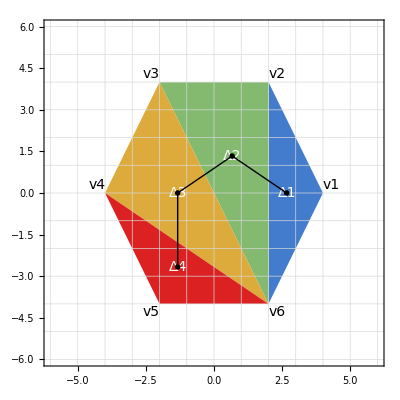

```mathematica
Show[triangulatePolygonAndPlot[ 
convexHexagon, earTips->False, arrows -> False,triangleLabels -> True], plotDualGraph[ convexHexagon ]
]
```

By inspection the triangulation of the concave hexagon has a dual graph that is clearly not isomorphic with that of the concave hexagon we saw earlier. We can use a built-in function to ascertain this result programmatically:

```mathematica
convexHexagonWLDualGraph := toWLDualGraph[ triangulatePolyIndexes[convexHexagon]];

IsomorphicGraphQ[concaveHexagonWLDualGraph, convexHexagonWLDualGraph]
```

False

## Visibility graph of a polygon

Another use of graph theory is to plot the visibility graph of a polygon:

Visibility graph of a polygon: A graph that has a node for each vertex in polygon P and an edge for each pair of vertexes that have line of sight of each other where lines of sight are inside the polygon.

If you imagine the polygon is a room, and the vertexes are corners, then if you stand in one vertex, you will have line of sight to the two vertexes on either side of you, and possibly others.

The visibility graph for a polygon is very easy to calculate because we know the following:

Each vertex v_i of polygon P has visibility to vertexes v_(i+1) and v_(i-1) because it is connected to each of them by an edge.

For vertex v_mto be visible to v_i, where m ≠ i , m ≠ i +1  and m ≠ i -1 the two must be connected by a polygon diagonal.

In other words, for one vertex to have line of sight of the other, they must be connected by an edge or a diagonal. Using this information, we can write code to generate the visibility graph for a polygon as follows just by aggregating the diagonal and edge indexes, and converting them into an association:

```mathematica
visibilityGraph[poly_?pointListQ] := 
#[[1]]<-> #[[2]]&/@Join[diagonalIndexes[poly], polyEdgeIndexes[Length[poly]]]
```

We can then apply the Wolfram Language built-in graph functions to this association. For example:

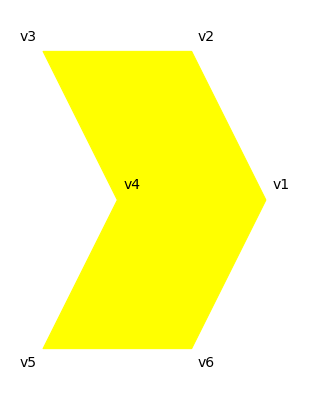
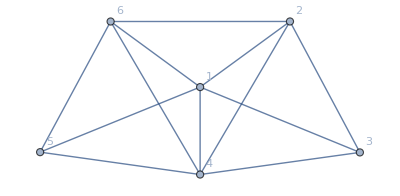
-Graphics- | -Graphics-
Graph association | {1<->3,1<->4,1<->5,2<->4,2<->6,4<->6,1<->2,2<->3,3<->4,4<->5,5<->6,6<->1}
Graph vertex count | 6
Graph edge count | 12
Set of vertexes with maximum degree | {1,4}

```mathematica
Block[{vgh},
vgh := visibilityGraph[concaveHexagon];
Grid[{
{plotPoly[concaveHexagon], Graph[vgh, VertexLabels->"Name"]},
{"Graph association",vgh },
{"Graph vertex count",VertexCount[vgh] },
{"Graph edge count",EdgeCount[vgh] },
{"Set of vertexes with maximum degree",GraphHub[vgh] }
}, Frame->All]
]
```

The GraphHub[...] is a particularly interesting function, because it lists the vertex or vertexes that have the maximum degree. Here are some example visibility graphs for our convexHexagon and concaveHexagon. We also introduce a new object the concaveHeptagon for comparison:

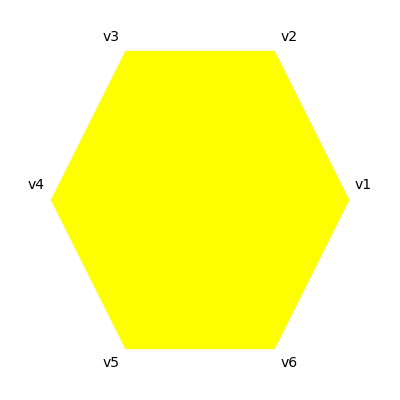
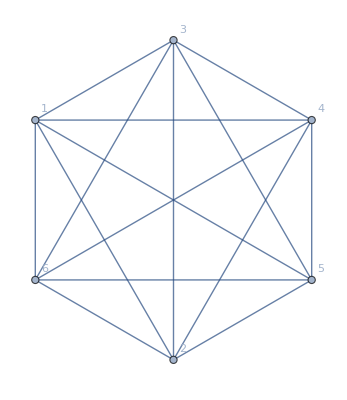
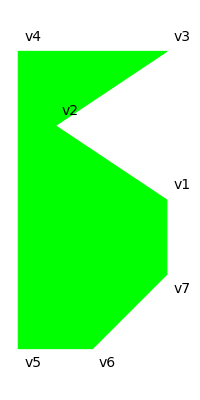
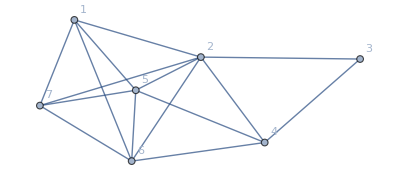
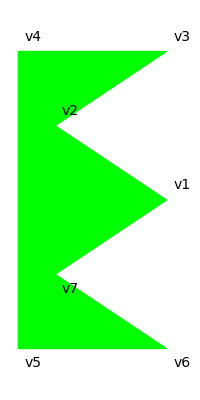
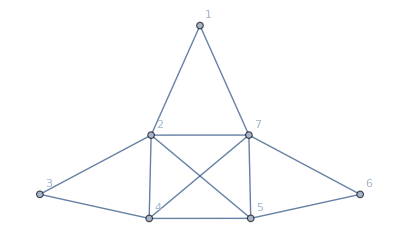
Polygon | Plot | Visibility graph | Max degree vertexes | Max degree
convexHexagon | -Graphics- | -Graphics- | {1,3,4,5,2,6} | 5
concaveHexagon | -Graphics- | -Graphics- | {1,4} | 5
concaveHeptagon1 | -Graphics- | -Graphics- | {2} | 6
concaveHeptagon2 | -Graphics- | -Graphics- | {2,7} | 5

```mathematica
concaveHeptagon1 := {{4,0},{1,2},{4,4}, {0,4}, {0,-4},{2,-4},{4,-2}};
concaveHeptagon2 := {{4,0},{1,2},{4,4}, {0,4}, {0,-4},{4,-4},{1,-2}};

Block[{vgConvexHexagon,vgConcaveHexagon, vgConcaveHeptagon1, vgConcaveHeptagon2},
vgConvexHexagon:= visibilityGraph[convexHexagon];
vgConcaveHexagon:= visibilityGraph[concaveHexagon];
vgConcaveHeptagon1:= visibilityGraph[concaveHeptagon1];
vgConcaveHeptagon2:= visibilityGraph[concaveHeptagon2];
Grid[{
{"Polygon", "Plot", "Visibility graph", "Max degree vertexes", "Max degree"},
{"convexHexagon", plotPoly[convexHexagon],Graph[vgConvexHexagon, VertexLabels->"Name"],GraphHub[vgConvexHexagon],Max[VertexDegree[vgConvexHexagon]]},
{"concaveHexagon", plotPoly[concaveHexagon], Graph[vgConcaveHexagon, VertexLabels->"Name"],GraphHub[vgConcaveHexagon], Max[VertexDegree[vgConcaveHexagon]]},
{"concaveHeptagon1", plotPoly[concaveHeptagon1, Green], Graph[vgConcaveHeptagon1, VertexLabels->"Name"],GraphHub[vgConcaveHeptagon1], Max[VertexDegree[vgConcaveHeptagon1]]},
{"concaveHeptagon2", plotPoly[concaveHeptagon2, Green], Graph[vgConcaveHeptagon2, VertexLabels->"Name"],GraphHub[vgConcaveHeptagon2], Max[VertexDegree[vgConcaveHeptagon2]]}
}, Frame->All]
]
```

You can see from this example, that for a polygon with n vertexes, any vertex that has a degree n-1 in the visibility graph  has line of sight to all the other vertexes.  Therefore, provided you start the triangulation on such a vertex, it can be triangulated by fanTriangulatePoly[...] whether it is convex or not. In fact, all regular or irregular  polygons up to and including the hexagon have at least one vertex that that has line of sight of all of the others, and so can be triangulated using this function. It turns out that we need 7 vertexes or more to be able to construct a polygon with a vertex that does not have line of sight of all of the others. The example convexHeptagon1 shows an irregular heptagon that can be triangulated with fanTriangulatePoly[...] and convexHeptagon2 shows one that can’t. A polygon that has at least one vertex that doesn’t have line of sight of all the others needs at least one example of the saw-tooth construction shown in  convexHeptagon2. This is a mouth-ear-mouth structure in the terminology we introduced earlier.

The demo below shows a dodecagon that has been triangulated. The dual graph of the triangulation is shown superimposed on the dodecagon (as already shown above), and to the right of the graphic is the visibility graph. Note that when the graphic turns red, the polygon is no longer simple, and the visibility graph (although one is still calculated) is not valid. As long as the maximum vertex degree is 12-1 = 11, then there is at least one vertex that has visibility of all the others. Notice that you have to create two “mouths” in order to make the maximum degree less than 11.

```mathematica
DynamicModule[{vg, isSimple, dodecagon = 5 regularPoly[12]},
Manipulate[

(*  Check that e have a simple polygon *)
If[simplePolyQ[poly],
(* If it is a simple polygon draw the polygon, triangulation and dual graph *)
Show[{
triangulatePolygonAndPlot[ poly, earTips->False, arrows -> False,triangleLabels -> True],
plotDualGraph[ poly ]
}],
(* If it is not a simple polygon draw the polygon in red *)
Graphics[{Opacity[0.5], Red, Polygon[poly]}, standardPlotStyle]
],

(* Draw the visibility graph of the polygon *)
Dynamic[Graph[vg = visibilityGraph[poly], VertexLabels->"Name", ImageSize->Medium]],

(* Print out the maximum vertex degree *)
Row[{
"Maximum vertex degree = ",
Dynamic[Max[VertexDegree[vg]]]
}],

(* The locators etc. *)
{{poly,dodecagon},{-5, -5}, {5,5},1, Locator},
ControlPlacement->Bottom
]
]
```

-Graphics-

## Summary

In this chapter we have graduated from the specific case of triangulating polygons to the general case of triangulating point sets. We presented a simple incremental point set triangulation algorithm that began by triangulating the convex hull of the point set, then located non-hull points within the resulting triangles and used them to triangulate further. In order to show the close relationship between convex hull and triangulation algorithms, we showed a combined incremental algorithm that calculated both a triangulation and the convex hull.

We looked at how to create the dual graph of a triangulation by detecting adjacent triangles. The dual graph provides a useful summary of the relationships between vertexes, edges and triangles. Finally, we considered the visibility graph of a polygon.

## Chapter 12: Delaunay triangulation

A set of n points with n > 3 will have several possible triangulations. In this chapter we look at some criteria against which these triangulations may be compared. This will lead us to the notion of the Delaunay triangulation, which in some senses, may be considered the optimal triangulation.

## Assessing triangulations

Not all triangulations are created equal. Some triangulations tend to give triangles that are short and fat, or long and thin, depending on how you look at them. You can see this very clearly in the example below that shows the fan triangulations of a skewed hexagon:

```mathematica
skewHexagon = {{4,0},{2,8},{-2,4},{-4,0},{-2,-4},{2,-4}};

plotConvexPolyFanTriangulation[  skewHexagon ]
```

-Graphics-

The fan triangulations are only a subset of the set of all possible triangulations, but are sufficient to illustrate the point. Consider each of the fan triangulations in turn:

Triangulation on vertex 1: the triangles are all quite similar and none are particularly long and thin.

Triangulation on vertex 2: all the triangles are very long and thin.

Triangulation on vertex 3: similar to 1, but the triangles are a bit fatter.

Triangulation on vertex 4: triangle v2 v3 v4 is very long and thin.

Triangulation on vertex 5: triangle v2 v3 v5 is a bit long and thin.

Triangulation on vertex 6: triangle v1 v2 v6 is a long and thin.

Obviously, none of these triangulations is more correct than the other, but for most applications, we tend to prefer triangulations that give triangles that are similar to each other and that are not long and thin. This is especially the case in computer graphics and geographic information systems where choosing an extreme triangulation might give unwanted results. We’ll see an example of this applied to a terrain map shortly.

It’s all very well talking about triangulations being too thin, but we really need to introduce some objective criteria to assess  them. We will consider one of these in the next section and work up to an implementation of Delaunay triangulation.

## The angle vector of a triangulation

One way of assessing a triangulation is to consider the angles of all of the triangles the comprise it. We can do this by using the notion of the angle vector:

Angle vector of a triangulation: the sorted list of the internal angles of all the triangles in the triangulation.

Essentially, all we need to do is take the List of internal angles for all triangles in the triangulation, and sort it. We can calculate the angle vector as follows:

```mathematica
angleVector[ trs_?triangleListQ]:= Sort[Flatten[ N [internalAngles /@ trs]]]
```

If two triangulations of a polygon or point set are T_1 and T_2 and their angle vectors are A(T_1) and A(T_2), we say that A(T_1)> A(T_2) if A(T_1) is lexicographically greater than A(T_2). Lexicographical ordering simply means {a,d,e} > {a,b,c} if d > b.

The angle vector gives us an objective way of comparing triangulations, and leads naturally to the notion of an angle optimal triangulation:

Angle optimal triangulation: if there are n possible triangulations, then triangulation T_i is angle optimal if A(T_i)≥ A(T_k) for i = 1...n and i ≠ k

In other words, we select the triangulation that has the largest internal angles for its triangles to be the optimal triangulation.

We can calculate the angle vectors for the fan triangulations from vertexes v_1 to v_6 for the skewHexagon as follows:

```mathematica
skewHexagonFanTriangulationAngleVecs =Table[angleVector[fanTriangulatePoly[ skewHexagon, i]], {i, 1, Length[skewHexagon]}];

Grid[{
{"Angle verctors for vertex triangulations of skewHexagon", SpanFromLeft },
{"V_1", "V_2", "V_3", "V_4", "V_5", "V_6"},
skewHexagonFanTriangulationAngleVecs
}, Frame->All]
```

Angle verctors for vertex triangulations of skewHexagon |  |  |  |  | 
V_1 | V_2 | V_3 | V_4 | V_5 | V_6
{0.519146,0.588003,0.588003,0.588003,0.737815,1.03038,1.10715,1.10715,1.3734,1.44644,1.44644,2.03444} | {0.141897,0.179853,0.244979,0.321751,0.321751,0.463648,0.785398,1.24905,1.5708,2.03444,2.43297,2.81984} | {0.463648,0.463648,0.463648,0.519146,0.737815,0.927295,1.03038,1.10715,1.3734,1.5708,1.69515,2.2143} | {0.141897,0.179853,0.519146,0.588003,0.588003,0.88848,0.927295,1.10715,1.32582,1.44644,2.03444,2.81984} | {0.321751,0.463648,0.463648,0.463648,0.519146,0.566729,0.588003,0.661043,1.91382,2.03444,2.2143,2.35619} | {0.244979,0.463648,0.463648,0.519146,0.519146,0.588003,0.785398,0.927295,1.69515,1.89255,2.03444,2.43297}

We can then sort these angle vectors so that they are in lexicographical order and from this get the order of the triangulations:

```mathematica
Grid[{
Subscript["V",ToString[#]]&/@Reverse[Sort[indexes[ skewHexagonFanTriangulationAngleVecs],OrderedQ[{skewHexagonFanTriangulationAngleVecs[[#1]], skewHexagonFanTriangulationAngleVecs[[#2]]}]&]]},
Frame->All]
```

V_1 | V_3 | V_5 | V_6 | V_4 | V_2

This tells us that, of the set of fan triangulations under consideration, the triangulation starting on vertex 1 has the most regular triangles and the triangulation starting on vertex 2 has the thinnest. You can check this in the example above. However, because we have only considered a subset of the triangulations, we don’t know if the triangulation on vertex 1 is angle optimal, or if there is a better choice. Rather than examine the complete set of possible triangulations, we can shortcut the process and instead generate an angle optimal triangulation. This is called a Delaunay triangulation, and we will look at this next.

## The Delaunay triangulation

We can define a Delaunay triangulation as follows:

Delaunay triangulation: a triangulation D(P) of P points in the plane such that no point is strictly inside the circumcircle of any triangle in D(P).

Based on the definition given above, we can write a test function to see if two adjacent triangles are in a Delaunay configuration or not:

```mathematica
delaunayQ[tr1_?triangleQ,tr2_?triangleQ]:=!((inCircumcircleQ[tr2, Complement[tr1, tr2][[1]] ]) ||
(inCircumcircleQ[tr1, Complement[tr2, tr1][[1]] ]))

delaunayQ[{tr1_?triangleQ,tr2_?triangleQ}] := delaunayQ[tr1, tr2]
```

If the point set is in general position (i.e. no three points collinear) then the Delaunay triangulation is angle optimal and unique.  If not, there may be more than one Delaunay triangulation, but all of them maximize the minimum angles of the triangles, and  have the same minimum angle. As such, for most applications, it generally doesn't matter which of them is chosen.

Whether a triangulation is Delaunay or not can have profound consequences. Consider the example below: if you loft a and d up the Z axis by increasing az and dz, then the edge c d is a trough (triangulation 1) or a ridge (triangulation 2). This is a common situation in geographic information systems where we have a 3D map comprising a set of points in the plane each of which has an associated altitude. In the example below, we don’t know which triangulation is correct - there are simply too few points to clearly identify c d as either a peak or a trough. However triangulation 1, the Delaunay triangulation, is generally considered to be the most reasonable (least extreme) answer. This is generally true for any triangulation that is used as a kind of interpolation. The example below also shows that the quadrilateral a b c d has two possible triangulations:

Triangulation 1 (Delaunay): triangles a b c and b d c

Triangulation 2 (non-Delaunay): triangles a b d and a d c

You can see that by  flipping the diagonal a d or c b  we can change the triangulation to Delaunay or not. In fact, we can take any non-Delaunay triangulation and, by flipping the appropriate diagonals, make it Delaunay. This is a very important observation that we will look at in more detail in the next section.

```mathematica
Manipulate[
Module[{ a3, b3, c3, d3},
a3 = Join[ {-4,-4}, {az}];
b3 = Join[ {4,0}, {bz}];
c3 = Join[ {0,4}, {cz}];
d3 = Join[ {4,5}, {dz}];
Graphics3D[{
 Text[Style["a", 18], a3],
 Text[Style["b", 18], b3],
 Text[Style["c", 18], c3],
 Text[Style["d", 18], d3],
Opacity[opacity],
If[ show ==1,
{Red, Polygon[{a3, b3, c3}],
Blue, Polygon[{b3, c3, d3}]}],
If[ show == 2,{Red, Polygon[{a3, b3, d3}],Blue, Polygon[{a3, c3, d3}]}]
},
AspectRatio -> 1, Axes -> True, 
AxesOrigin -> {0,0}, 
PlotRange->{{-5,5},{-5,5}, {-5,5}}
]
],
"Triangulation 1 is Delaunay",
{{show,1, "triangulation"}, {1, 2 }},
{{opacity, 0.5, "opacity"}, 0.0, 1},
{{az, 0,"az"}, -5, 5},
{{bz, -5, "bz"}, -5, 5},
{{cz, -5, "cz"}, -5, 5},
{{dz, 0, "dz"},-5, 5}
]
```

-Graphics-

The example above also illustrates the two possible triangulations the quadrilateral a b c d:

Triangulation 1 (Delaunay): triangles a b c and b d c

Triangulation 2 (non-Delaunay): triangles a b d and a d c

## Flipping diagonals

If we take any two adjacent triangles, they always form a quadrilateral. This quadrilateral is (of course) triangulated by a diagonal that is the common edge of the two adjacent triangles. However, if the quadrilateral is convex, it has another possible diagonal, and therefore another possible triangulation. In the convex case where there are two possible triangulations, one of them will be Delaunay [ORourke2]. So if the original convex quadrilateral triangulation is not Delaunay, we can make it so simply by flipping the diagonal. In fact, we can make any triangulation Delaunay simply by repeating this flipping process.

Let’s look at adjacent triangles in more depth. If two triangles t_1 and t_2 are adjacent we can find or construct the following objects:

The common edge comprising the two common vertexes: t_1∩ t_2

The two non-common vertexes (we will call these “apexes” for convenience): (t_1∪ t_2) \ (t_1∩ t_2)

A quadrilateral formed from the union of the two triangles: t_1∪ t_2

Here are the functions to do this:

```mathematica
commonEdge[ tr1_, tr2_ ] := tr1∩tr2

apexes[ tr1_, tr2_ ] := Complement[ tr1∪tr2,tr1∩tr2 ]

toQuad[ tr1_, tr2_ ] :=Riffle[ apexes[tr1, tr2], commonEdge[tr1, tr2]]
```

As we saw above, if the quadrilateral formed from the two triangles is convex, it has two legal diagonals and it has two possible triangulations each comprising two triangles. We say the two triangles in each triangulation are “flippable”. We can test for flippable triangles as follows:

```mathematica
flippableQ[ tr1_ ,tr2_] :=Block[{q},
(* Note: tr1 and tr2 must be adjacent *)
q = toQuad[ tr1, tr2 ];
(* Check that the quadrilateral has 2 valid diagonals *)
(diagonalQ[ q, 1,3 ] && diagonalQ[ q, 2,4]) ||
(diagonalQ[ Reverse[q], 1,3 ] && diagonalQ[ Reverse[q], 2,4])
]
```

Note that we could also test for flippable triangles simply by testing if the quadrilateral was convex or not. However, this would be slower as it would involve sorting the quadrilateral vertexes by theta to put them in anti clockwise order. The algorithm we use above avoids an expensive sort.

The two possible triangulations of a flippable triangle pair are given by:

```mathematica
flipTriangles[ tr1_, tr2_ ] := Block[{q},
(* Provided we only call this on flippable triangle pairs, 
we are safe in sorting the quadilateral vertexes to put them in anti-clockwise order. Otherwise, we will change the shape of the quadilateral. *)
q = sortByTheta[toQuad[ tr1, tr2 ]];
{{q[[1]], q[[2]], q[[3]]}, {q[[3]], q[[4]], q[[1]]},
{q[[2]], q[[3]], q[[4]]}, {q[[4]], q[[1]], q[[2]]}}
]

flipTriangles[{tr1_, tr2_}]:=flipTriangles[ tr1, tr2 ]
```

The Delaunay triangulation is given by:

```mathematica
delaunayTriangles[ tr1_, tr2_] := Block[{nt1, nt2, nt3, nt4},
{nt1, nt2, nt3, nt4} = flipTriangles[ tr1, tr2];
If[ delaunayQ[ nt1, nt2],
{nt1, nt2},
{nt3, nt4}
]
]

delaunayTriangles[ {tr1_, tr2_} ] := delaunayTriangles[ tr1, tr2]
```

Here is a test program. Select each triangulation in turn and compare the Delaunay and non-Delaunay triangulations. You can also move the vertexes around to form a non-flippable quadrilateral:

```mathematica
testFlippableQ[]:= Manipulate[
Module[{ tr1, tr2, q, apes, ce, sameSide, nt1, nt2, nt3, nt4, flippable, ct1, ct2, c1, c2},
tr1 = pts[[{1,2,3}]];
tr2 = pts[[{3,4, 1}]];
q = toQuad[ tr1, tr2];
apes = apexes[tr1, tr2];
ce = commonEdge[tr1, tr2];
sameSide =sameSideQ[ce[[1]], ce[[2]], apes ];
{nt1, nt2, nt3, nt4} = flipTriangles[tr1, tr2];
flippable = flippableQ[tr1, tr2];

If[triangulation == "triangulation1",
ct1 = nt1; ct2 = nt2; c1 = N[circumcircle[nt1]]; c2 = N[circumcircle[nt2]], 
ct1 = nt3; ct2 = nt4; c1 = N[circumcircle[nt3]]; c2 = N[circumcircle[nt4]]
];

Graphics[{
(* Draw the diagonals *)
{Dashed, Line[apes], Line[ce]},

(* Draw flippableQ *)
{If[flippable && !sameSide,Green,Red],Text[Style["flippableQ", 18], {0,5.5}]},

(* If both apexes are on the same side of the common edge, the quadrilateral id concave *)
If[sameSide, Text[Style["Quadrilateral is not convex!", 18, White,Background->Red], {0,5.5}]],

(* Valid triangles that are flippable *)
If[!flippable || sameSide,
{Opacity[0.5], Magenta, Polygon[tr1],Cyan,Polygon[tr2]},
{Opacity[0.5], 
Red,Polygon[ct1],Circle[c1[[1]], c1[[2]]],
Blue,Polygon[ct2],Circle[c2[[1]], c2[[2]]]
}],

(* Is the triangulation Delaunay? *)
If[(!sameSide) && flippable && delaunayQ[ct1, ct2], Green,Red],
Text[Style["delaunayQ", 18], {0,5}]
},
standardPlotStyle]
],
"The diagonals are shown as dashed lines.",
{triangulation, {"triangulation1", "triangulation2"}},
{{pts,{{5,-1}, {3,3}, {-2,3}, {-4,-5}}},{-5, -5}, {5,5}, 1, Locator}
]

testFlippableQ[]
```

-Graphics-

## Converting a triangulation to a Delaunay triangulation

Given any triangulation, we are now in a position to convert it to a Delaunay triangulation by flipping the appropriate edges of adjacent triangles. A simple brute force algorithm is as follows:

Take any triangulation T

While there is a triangle pair in T that is flippable and non-Delaunay:

Flip the diagonal of the pair.

The following function finds the indexes of two triangles that are flippable and non-Delaunay:

```mathematica
findFlippableNonDelaunay[ trs_ ] := 
Flatten[Select[ adjacentTriangleIndexes[ trs ], 
(flippableQ[ trs[[#[[1]]]], trs[[#[[2]] ]]] &&
!delaunayQ[trs[[#[[1]]]], trs[[#[[2]] ]]])&,1], 1]
```

The next function performs a flip on a triangulation. It returns a new copy of the triangulation with the diagonal flipped:

```mathematica
flip[ trs_ ] := Block[{trsLocal = trs,fi, dets},
fi =findFlippableNonDelaunay[ trsLocal];
If[ fi ≠ {},
dets = delaunayTriangles[ trsLocal[[ fi[[1]] ]], trsLocal[[ fi[[2]] ]] ];
trsLocal[[ fi[[1]] ]] = dets[[1]];
trsLocal[[ fi[[2]] ]] = dets[[2]];
];
trsLocal
]
```

We can now convert a triangulation to a Delaunay triangulation by applying flip to it until the result doesn’t change. We can use the built-in function FixedPoint for this:

```mathematica
toDelaunay[ trs_ ] := FixedPoint[ flip, trs]
```

For example:

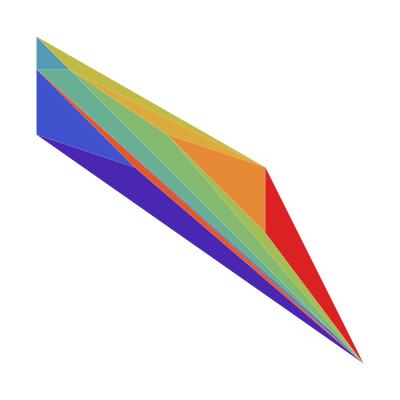
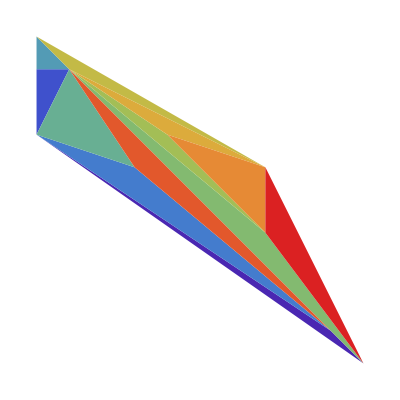
Non-Delaunay | Delaunay
-Graphics- | -Graphics-

```mathematica
Block[{trs},
trs =triangulatePointSet[randomPointSet[10]];
Grid[{
{"Non-Delaunay","Delaunay"},
{Graphics[drawColouredPolys[ trs]],
Graphics[drawColouredPolys [toDelaunay[trs]]]}
}, Frame->All]
]
```

If you run the above example a few times, you should get a good idea of the difference between Delaunay and non-Delaunay triangulations.

If we want to see the intermediate triangulations, we can use the built-in function FixedPointList[...] which returns a List containing the result of each individual application of the function. Note that the last two elements in this List will be the same, because FixedPointList[...] continues until its result no longer changes. We can discard this duplicate by using the function Most[...] that returns everything in a List except the last element. In fact, using Most[...] with FixedPointList[...] is a very common Wolfram Language idiom:

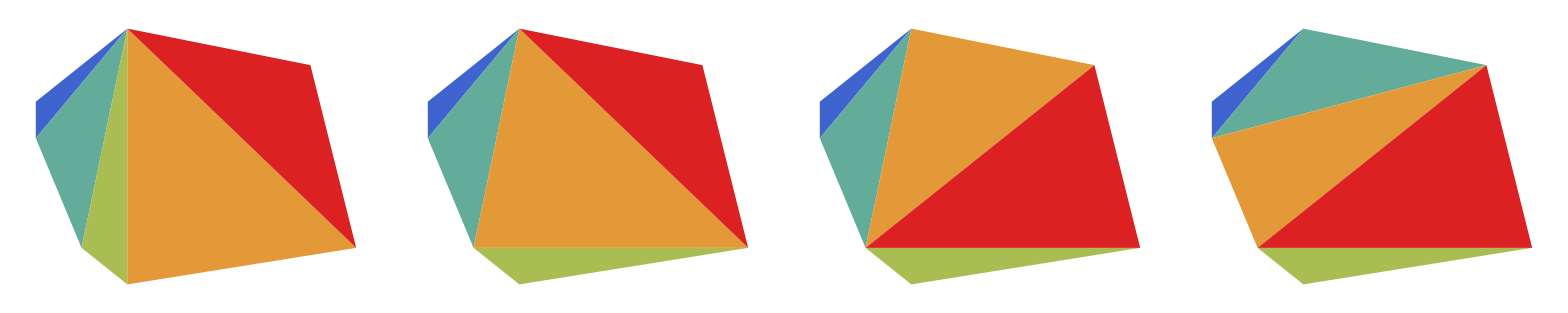

```mathematica
Block[{trs},
trs =triangulatePointSet[randomPointSet[7]];
Grid[{
Graphics[drawColouredPolys[#]]&/@Most[ FixedPointList[ flip, trs ]]
}, Frame->All]
]
```

## Delaunay triangulation example

Firstly, here is a utility program that plots a set of triangulations consecutively:

```mathematica
triangulatePolygonAndPlots[triangulations_]:= Manipulate[
Module[{centers, selectedTriangulation, circs},
selectedTriangulation = triangulations[[triangulation]];
centers = Mean /@ selectedTriangulation;
circs = circumcircle /@ selectedTriangulation;
Graphics[{
drawColouredPolys[selectedTriangulation],
Arrow /@ polyEdges /@ selectedTriangulation,

If[ drawCircumcircles,
MapIndexed[{ColorData["Rainbow"][#2[[1]]/ Length[circs]],Circle[#1[[1]], #1[[2]] ]}&, circs]
],

Text[#, centers[[#]]]& /@ indexes[selectedTriangulation]
},
standardPlotStyle]
],
{{drawCircumcircles, True, "draw circumcircles"}, {True, False}},
{{triangulation, 1, "triangulation"}, 1,Length[ triangulations],1}
]
```

Here is a test program that plots the stages in the Delaunay triangulation of a random set of ten points using our brute force algorithm. If you run this as an animation, you can see the Delaunay triangulation algorithm in action:

```mathematica
Block[{initial},
initial = triangulatePointSet[randomPointSet[10]];
triangulatePolygonAndPlots[Join[ {initial},Most[FixedPointList[flip,initial]]]]
]
```

-Graphics-

## Delaunay triangulations and terrain

We have already touched on this topic, but now we are in a position to investigate it in depth. If we take a random point set and associate a random altitude with each point, then we have a random terrain.  An easy way to associate an altitude with a point is to use an associative array with the point as the key and the altitude as the value. Consider the program below:

```mathematica
Block[{pts, altitudes},
pts = randomPointSet[3];
(altitudes[#]= Random[ Integer, {-2,2}])&/@ pts;
Print[ Row[{"point = ", #," altitude = ",altitudes[ # ]} ]] &/@ pts;
]
```

point = {-4,-1} altitude = -1

point = {4,2} altitude = -2

point = {3,-1} altitude = -1

The variable altitudes is just an associative array where each key is a point from the point set, and each value an altitude up the Z axis. We can now write a function to turn a set of 2D triangles into a terrain (a set of 3D triangles) by associating an altitude with each 2D triangle vertex:

```mathematica
addAltitude[ trs_?triangleListQ, altitudes_ ] := {
{#[[1,1]], #[[1,2]], altitudes[ #[[1]] ]}, 
{#[[2,1]], #[[2,2]], altitudes[ #[[2]] ]},
{#[[3,1]], #[[3,2]], altitudes[ #[[3]] ]}
}&/@ trs
```

The program below takes a random point set and then creates a Delaunay triangulation and all intermediate results, just as we did before. The difference is that each point in the triangulations is now associated with an altitude. We can now see the effect of Delaunay triangulation on a terrain: as we approach the Delaunay triangulation, we tend to loose any long narrow valleys. Of course, we don’t know if the final terrain is correct (we would need more data points for that), but it is probably a good guess.

```mathematica
randomTerrain[ pts_?pointListQ ] := DynamicModule[ {altitudes, trs, triangs, triangs3D},
(altitudes[#]= Random[ Integer, {-5,5}])&/@ pts;
trs = triangulatePointSet[ pts ];
triangs = FixedPointList[ flip, trs ];
triangs3D = addAltitude[ #, altitudes ]&/@triangs;
Manipulate[
Graphics3D[{
Opacity[opacity],
Scale[Polygon[ triangs3D[[selectedTriangulation]]], {1,1,height}]
}, 
AspectRatio -> 1, Axes -> True, 
AxesOrigin -> {0,0}, 
PlotRange->{{-5,5},{-5,5}, {-5,5}}
],
{{selectedTriangulation, 1, "triangulation"}, 1,Length[triangs3D],1},
{{opacity, 0.5, "opacity"}, 0.0, 1},
{{height, 0.3, "height"}, 0.0, 1}
]
]

randomTerrain[ randomPointSet[20]]
```

-Graphics-

## Summary

In this chapter we considered several criteria for the “quality” of a triangulation. We then presented an algorithm to convert a triangulation into a Delaunay triangulation by diagonal flipping.  Delaunay triangulations maximise the minimum angles of each triangle.

## Chapter 13: Voronoi diagrams

A Voronoi diagram shows a plane that contains a set of points divided up into regions called Voronoi regions. Here are some definitions:

Voronoi region: given a set of points in the plane called sites, a Voronoi region is a partitioning of the plane made by assigning each point that is not a site to its nearest site.

In other words, the plane is divided according to how near a a particular point is to a site. This creates a pattern of polygonal cells called Voronoi regions.

Voronoi edge: an edge of a Voronoi region.

Voronoi vertex: the a vertex of one of the Voronoi regions.

Voronoi diagram: the set of points that have more than one nearest neighbor site.

The Voronoi diagram comprises the set of edges of all the polygonal cells that make up Voronoi regions.

To be more precise, let P = {p_1, p_2, ... , p_n} be a set of sites. The Voronoi region V(p_i) of site p_i is then [ORourke1]:

V(p_i) = { x : | p_i - x | ≤ | p_j - x |  ∀ j != i }

So in other words, the Voronoi region of a site contains all points at least as close to that site as to any other site. This always forms a convex set (see [ORourke1] for a proof).

The set of points that are equidistant from multiple sites forms the Voronoi diagram, 𝒱(P), for the set of sites.

The Wolfram Language has good support for computational geometry, so let’s see what these objects look like for a given set of sites. We can use the Wolfram Language functions VoronoiMesh[...] (Voronoi diagram) and DelaunayMesh[...] (Delaunay triangulation) to visualize them as follows:

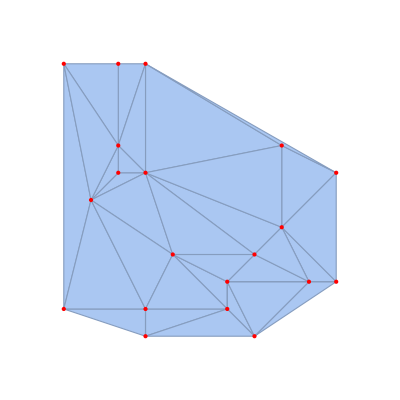
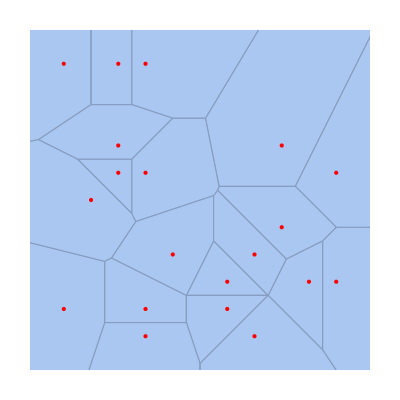
The sites | Delaunay trianguation | Voronoi diagram
-Graphics- | -Graphics- | -Graphics-

```mathematica
Block[{pts, r = {{-6,6},{-6,6}}},
pts = randomPointSet[20];
Grid[{
{"The sites","Delaunay trianguation", "Voronoi diagram"},
{
Graphics[{Red,Point[pts]}, PlotRange->r],
Show[DelaunayMesh[ pts],Graphics[{Red,Point[pts]}], PlotRange->r],
Show[VoronoiMesh[ pts],Graphics[{Red,Point[pts]}], PlotRange->r]
}
}, Frame->All]
]
```

Notice that the Delaunay triangulation joins the points (sites) together into a triangular mesh, whilst the Voronoi edges trace out edges between two sites where all points on the edge are equidistant from both sites thereby creating polygons. The Voronoi regions are the polygons enclosed by the Voronoi edges.

In the above demo, the built-in functions DelaunayMesh[...] and VoronoiMesh[...] return the Delaunay or Voronoi diagrams as a data structure called a MeshRegion. The Wolfram Language has many functions for creating, and performing operations on, regions but that is beyond the scope of this book. However, to give you some idea, we will look at a few of the simpler region functions. The function MeshCoordinates[...] returns a List of the vertexes of the MeshRegion. The MeshCells[...] function is very general because it accepts a dimension as a second parameter. If the dimension is 0, it returns any points, if 1,  it returns lines , if 2  it returns polygons. These objects are Lists of indexes into the List of MeshRegion coordinates, not actual coordinates:

```mathematica
Block[ {pts, d},
pts = randomPointSet[ 5 ]; 
d = DelaunayMesh[ pts ];
Grid[{
{"Mesh coordinates", "Mesh points (indexes)", "Mesh lines (indexes)", "Mesh polygons (indexes)"},
{MeshCoordinates[ d ],MeshCells[d,0],MeshCells[ d, 1 ],MeshCells[ d, 2 ]}
}, Frame->All]
]
```

Mesh coordinates | Mesh points (indexes) | Mesh lines (indexes) | Mesh polygons (indexes)
{{4.,-5.},{2.,-2.},{-4.,-3.},{4.,1.},{-4.,2.}} | {Point[1],Point[2],Point[3],Point[4],Point[5]} | {Line[{5,3}],Line[{3,2}],Line[{2,5}],Line[{2,1}],Line[{1,4}],Line[{4,2}],Line[{3,1}],Line[{4,5}]} | {Polygon[{5,3,2}],Polygon[{2,1,4}],Polygon[{1,2,3}],Polygon[{2,4,5}]}

## A Voronoi diagram algorithm

The Voronoi diagram for a point set is intimately related to its Delaunay triangulation. In fact, the relationship is quite striking: the Voronoi diagram is actually the dual graph of the Delaunay triangulation and vice-versa. So given either of these, it is not difficult to calculate the other. We already have an algorithm for the Delaunay triangulation, and we can derive from this triangulation the corresponding Voronoi diagram. As far as such a conversion algorithm is concerned, the Delaunay/Voronoi duality has several important features:

The Voronoi vertexes are the centers of the circumcircles of the triangles in the Delaunay triangulation [ORourke1]. This gives us a simple way to calculate the sites.

The dual graph of the Delaunay triangulation tells us how the Voronoi vertexes are connected together by Voronoi edges.

When a site is bounded by other sites (i.e. is strictly inside the convex hull of the triangulation), it generates a polygon in the Voronoi diagram.

When a site is unbounded (i.e. on the convex hull of the triangulation) it generates a polygonal chain and two rays in the Voronoi diagram.

This suggests a very simple conversion algorithm:

Calculate the convex hull, the Delaunay triangulation, the circumcircles and the dual graph of the set of sites (points).

For the bounded sites:

Connect the site circumcircle centers according to the dual graph to create a set of Voronoi edges.

For each unbounded site u:

Find the triangle t_uassociated with u.

Find the edge (p_i  p_k) of t_u that is on the convex hull. Calculate the point p_r = (p_i +  p_k)/2 that is half way along this edge.

If u is inside the convex hull create a ray from u through p_r to infinity. We call this an inner ray.

If u is outside the convex hull create a ray from p_r through u to infinity. We call this an outer ray.

If u is on the convex hull create a ray from u to infinity that is external to the convex hull and at right angles to edge (p_i  p_k). This is also an outer ray.

This algorithm generates the Voronoi diagram as a set of edges and rays. This distinction is necessary because when we come to plot the diagram, we obviously have to handle plotting rays very differently to plotting edges. As a bonus side-effect, the algorithm calculates just about everything else we need to investigate the Voronoi, Delaunay relationship! Here is an implementation:

```mathematica
voronoiDiagram[ pts_ ] := 
Block[
{hull, del, vSites, dg, vEdges, rayStart, rayEnd, rays, iRays, oRays, innerVoronoiRay, outerVoronoiRay},

(* Calculate the convex hull edges *)
hull =convexHullGraham[pts];

(* Calculate the Delaunay triangulation *)
del = toDelaunay[ triangulatePointSet[ pts ] ];

(* Calculate the circumcircles *)
vSites = circumcircle[ # ][[1]]&/@del;

(* Calculate the dual graph *)
dg = adjacentTriangleIndexes[del];

(* Process the bounded sites - *)(* join the circumcircle centers according to the dual graph to create edges *)
vEdges = vSites[[#]]&/@ dg;

(* Process the unbounded sites to create rays *)
rays = Reap[
(
(* For a hull edge there is only 1 triangle *)
rayStart = vSites[[ First[findTriangleIndexesForEdge[del,#]] ]];
rayEnd = Mean[#];
If[rayStart == rayEnd, 
rayEnd = rotate90[ rayEnd - #[[1]]] + rayEnd;
];
Sow[ {rayStart, rayEnd},If[ insideConvexQ[ hull, rayStart],innerVoronoiRay, outerVoronoiRay]];
)&/@  polyEdges[hull] ;,
{innerVoronoiRay, outerVoronoiRay}
];
iRays = Flatten[rays[[2, 1]], 1];
oRays = Flatten[rays[[2, 2]], 1];
{
hull,      (* convex hull *)
del,        (* Delaunay triangulation *)
dg,          (* dual graph *)
vSites, (* Voronoi sites *)
vEdges, (* Voronoi edges *)
iRays,   (* inner Voronoi rays *)
oRays       (* outer Voronoi rays *)
}
]
```

Now we can write a program to plot the Delaunay triangulation and its associated Voronoi diagram. Notice how we handle the rays - we just draw them as very long lines.

```mathematica
plotDelaunayVoronoi[ pts_ ] :=DynamicModule[
{hull,del, dg, vSites,vEdges, iRays, oRays},
{hull, del, dg,vSites, vEdges,iRays, oRays} = voronoiDiagram[ pts ];
Manipulate[
Graphics[{
If[ triangles,drawColouredPolys[ del ]],
If[ sites,Disk[ #, 2 ] &/@ pts],
If[ voronoiCells,
{
(* draw the edges *)
Line /@ vEdges,
(* draw the inner rays *)
Line[extendLine[#, 10000, 1, True]]&/@ iRays,
(* draw the outer rays *)
Line[extendLine[#, 10000, -1]]&/@ oRays
}]
},
PlotRange->{zoom{-110 , 110 },zoom{-110, 110}}],
{{zoom, 1, "zoom"},  1, 10},
{{voronoiCells, True, "Voronoi cells"}, {True, False}},
{{sites, True, "sites"}, {True, False}},
{{triangles, True, "triangles"}, {True, False}}
]
]

plotDelaunayVoronoi[randomPointSetGP[20, Range[-100, 100]]]
```

-Graphics-

## Summary

In this short chapter we introduced the Voronoi diagram, and explored its relationship to the Delaunay triangulation.

## Chapter 14: Summary

This ends Interactive Computational Geometry (Wolfram Language edition). We hope you have enjoyed this book and have found it useful. If you have any ideas for improvements, or any corrections or contributions, we be would be delighted to hear from you. You can contact us at www.clearviewtraining.com. If you are also a Python programmer, be sure to check out our “Interactive Computational Geometry in Python”!

Dr. Jim Arlow

www.clearviewtraining.com

Isle of Wight, UK, 2020

## Resources

You can download a fully interactive version of this book as a Mathematica Notebook. This is available online from the Wolfram Foundation Notebook Archive. You can search on the author name, “Arlow”, to find the file. Because of the size and complexity of this book, it won’t run directly in the Notebook Archive, nor in the Wolfram Cloud, and we are currently working with Wolfram Research to fix this. You will need either a copy of  Mathematica or the cheaper Wolfram Player Pro in order to run the Notebook.  You will definitely get the most out of the book by running it in Mathematica, because you will be able to modify the code. The book runs in desktop version 12.0 or later.

## Bibliography

[Bourke1]  “http://paulbourke.net/papers/triangulate/”
“Triangulate - Efficient Triangulation Algorithm Suitable for Terrain Modelling”.

[Fukuda1] “http://www.cs.mcgill.ca/~fukuda/soft/polyfaq/polyfaq.html”
Frequently Asked Questions in Polyhedral Computation.

[Klobučar1] “http://hrcak.srce.hr/1799?lang=en”
“On nonexistence of an integer regular polygon”. Klobučar, D. (1998), Mathematical Communications, 3(1), 143-146.

[ORourke1] “http://cs.smith.edu/~orourke/books/compgeom.html”
“Computational Geometry in C (Second Edition)”, Joseph O’Rourke.
This book was our initial inspiration for creating Interactive Computational Geometry. A good selection of algorithms (more than we have here) are presented in a clear and concise way.

[ORourke2] “http://www.exaflop.org/docs/cgafaq/cga1.html#Subject”
Comp.Graphics.Algorithms Frequently Asked Questions, Section 1. 2D Computations: Points, Segments, Circles, Etc., (C) 1998 Joseph O’Rourke.
An excellent selection of algorithms for 2D graphics.

[ORourke3] “http://cs.smith.edu/~orourke/DCG/#Voronoi”
Plotting Voronoi diagrams and Delaunay triangulations using the Wolfram Language built-in functions

[Taslakian1] “http://cgm.cs.mcgill.ca/~perouz/cs507/vertexdual/introduction.htm”
“Hamiltonian Cycles in the Vertex-Adjacency Dual”

[Coxeter1] “http://www.amazon.co.uk/Regular-Polytopes-Dover-Books-Mathematics-ebook/dp/B00A73AXLG/ref=la_B001ITYBRA_1_3?s=books&ie=UTF8&qid=1404378949&sr=1-3”
“Regular polytopes”, Harold Scott Macdonald Coxeter (1973) Courier Dover Publications. ISBN 978-0-486-61480-9

[Devadoss1] “http://www.amazon.co.uk/Discrete-Computational-Geometry-Satyan-Devadoss-ebook/dp/B004UGKK3M/ref=sr_1_1?s=books&ie=UTF8&qid=1404380056&sr=1-1&keywords=discrete+and+computational+geometry”
“Discrete and Computational Geometry”, Princeton University Press (11 April 2011), Satyan L. Devadoss, Joseph O’Rourke, Princeton University Press (11 April 2011), ISBN: 0691145539
Lots of very useful exercises! A useful companion to [O’Rourke1].

[deBerg1] “http://www.amazon.co.uk/Computational-Geometry-Applications-Mark-Berg/dp/3540779736/ref=sr_1_1?s=books&ie=UTF8&qid=1404380357&sr=1-1&keywords=computational+geometry”
“Computational Geometry: Algorithms and Applications, Second Edition”, Mark de Berg, M. van Krefeld, M. Overmars, O. Schwarzkopf, Springer, ISBN-13: 978-3540779735